## Solar surface probability

```mathematica
$Assumptions=mol>0&&cm>0&&m>0&&eV>0&&MeV>0;
```

```mathematica
SSModel = Import[NotebookDirectory[]<>"Functions/Data/bs2005agsopflux.csv","Table"];
data=SSModel[[28;;,;;]];
```

```mathematica
MatrixForm[SSModel[[1;;27]]]
```

({Distribution,of,neutrino,fluxes,in,the,BS05(AGS,OP),standard,solar,model,model.}
{}
{astro-ph/0412440}
{}
{The,cumulative,neutrino,fluxes,from,Table,1,of,BS05(AGS,OP),are,given,in,the,row,below.}
{}
{6.058,0.01453,8.254×10^-7,0.4338,0.0004508,0.02007,0.01445,0.0003254}
{}
{}
{Columns,in,the,Table,below,represent:}
{}
{1),Radius,of,the,zone,in,units,of,one,solar,radius}
{2),Temperature,in,units,of,10^6,deg,(K)}
{3),Logarithm,(to,the,base,10),of,the,electron,density,in,units,of}
{cm^{-3}/N_A,,where,N_A,is,the,Avogadro,number}
{4),Mass,of,the,zone,with,the,given,radius,in,units,of,one,solar,mass}
{5),X(^7Be):,beryllium-7,mass,fraction}
{[For,special,purposes,,it,is,useful,to,know,the,7^Be,mass,fraction.]}
{6),Fraction,of,pp,neutrinos,produced,in,the,zone}
{7),Fraction,of,boron,8,neutrinos,produced,in,the,zone}
{8),Fraction,of,nitrogen,13,neutrinos,produced,in,the,zone}
{9),Fraction,of,oxygen,15,neutrinos,produced,in,the,zone}
{10),Fraction,of,florine,17,neutrinos,produced,in,the,zone}
{11),Fraction,of,beryllium,7,neutrinos,produced,in,the,zone}
{12),Fraction,of,pep,neutrinos,produced,in,the,zone}
{13),Fraction,of,hep,neutrinos,produced,in,the,zone}
{})

```mathematica
B8data = Import[NotebookDirectory[]<>"Functions/Data/B8.csv"];
B8 = Interpolation[B8data,InterpolationOrder->1];
HEPdata = Import[NotebookDirectory[]<>"Functions/Data/HEP.csv"];
HEP = Interpolation[HEPdata,InterpolationOrder->1];

density[r_] = Interpolation[Table[{data[[i,1]],10^data[[i,3]]},{i,Length[data]}],InterpolationOrder->1][r]*(mol/cm^3);

B8radial = Interpolation[data[[All,{1,7}]],InterpolationOrder->1];
B8int = NIntegrate[B8radial[r],{r,0,0.5}];
HEPradial = Interpolation[data[[All,{1,13}]],InterpolationOrder->1];
HEPint = NIntegrate[HEPradial[r],{r,0,0.5}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {0.036125}. NIntegrate obtained 0.000409837 and 9.97523×10^-10 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {0.141594}. NIntegrate obtained 0.000409834 and 9.25407×10^-10 for the integral and error estimates.

InterpolatingFunction::dmval: Input value {0.0000204286} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

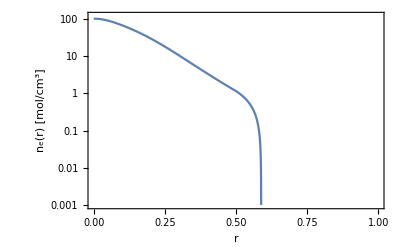

```mathematica
LogPlot[density[r]/(mol/cm^3),{r,0,1},PlotRange->{{0,1},{10^-3,120}}, Frame->True,FrameLabel->{ "r", "n_e(r) [mol/cm^3]"}]
```

```mathematica
V[Ne_] := (3.868 10^-7/m)*(Ne/(mol/cm^3)); (* 4.17 in 1802.05781 *)
k[Δm2_,e_]:= (2.533/m)*(Δm2/eV^2)*(MeV/e); (* 4.18 in 1802.05781 *)
```

```mathematica
th12M[th12_,th13_, Δms21_,Δms31_,e_,Ne_] := Mod[ArcTan[Tan[2 th12]/(1 - (Cos[th13]^2/Cos[2 th12])* (V[Ne]/k[Δms21,e]) )]/2,Pi/2];
th13M[th12_,th13_, Δms21_,Δms31_,e_,Ne_] := Mod[ArcSin[Sin[th13]*(1+ (V[Ne]/k[Δms31,e])*Cos[th13]^2)],Pi/2];
```

```mathematica
Pveve[th12_,th13_, Δms21_,Δms31_,e_,Ne_]:=Cos[th13]^2 Cos[th13M[th12,th13, Δms21,Δms31,e,Ne]]^2*(Cos[th12]^2 Cos[th12M[th12,th13, Δms21,Δms31,e,Ne]]^2 + Sin[th12]^2 Sin[th12M[th12,th13, Δms21,Δms31,e,Ne]]^2) + Sin[th13]^2 Sin[th13M[th12,th13,Δms21,Δms31,e,Ne]]^2;
```

```mathematica
PB8=Table[{e,NIntegrate[Pveve[ArcTan[√0.469],ArcSin[√0.01],7.9 10^-5 eV^2,2.46 10^-3 eV^2,e*MeV,density[r]]*B8radial[r]/B8int,{r,0,0.5}]},{e,B8data[[All,1]]}];
Phep=Table[{e,NIntegrate[Pveve[ArcTan[√0.469],ArcSin[√0.01],7.9 10^-5 eV^2,2.46 10^-3 eV^2,e*MeV,density[r]]*HEPradial[r]/HEPint,{r,0,0.5}]},{e,HEPdata[[All,1]]}];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {0.0449141}. NIntegrate obtained 0.524036 and 1.03833×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {0.0449141}. NIntegrate obtained 0.519144 and 1.09452×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {0.0449141}. NIntegrate obtained 0.514518 and 1.07358×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {0.116203}. NIntegrate obtained 0.53592 and 1.1541×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {0.116203}. NIntegrate obtained 0.531832 and 1.25797×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {0.116203}. NIntegrate obtained 0.528817 and 1.30858×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

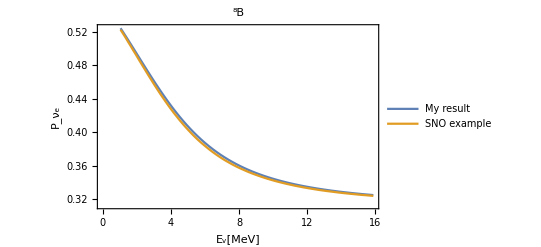

```mathematica
ListPlot[{PB8,B8data},Joined->True, Frame->True,FrameLabel->{"E_v[MeV]","P_ν_e"}, PlotLabel->"^8B",PlotLegends->Placed[{"My result","SNO example"},{Right,Top}]]
```

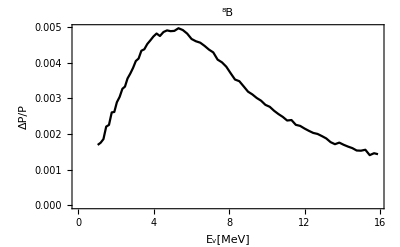

```mathematica
ListPlot[Table[{PB8[[i,1]],Abs[((PB8-B8data)/(PB8+B8data))[[All,2]][[i]]]},{i,Length[PB8]}],Joined->True, Frame->True,FrameLabel->{"E_v[MeV]","ΔP/P"}, PlotLabel->"^8B",PlotStyle->Black]
```

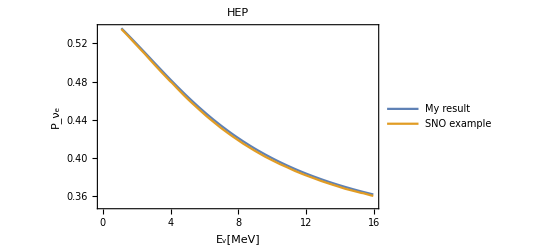

```mathematica
ListPlot[{Phep,HEPdata},Joined->True,Frame->True,FrameLabel->{"E_v[MeV]","P_ν_e"}, PlotLabel->"HEP",PlotLegends->Placed[{"My result","SNO example"},{Right,Top}]]
```

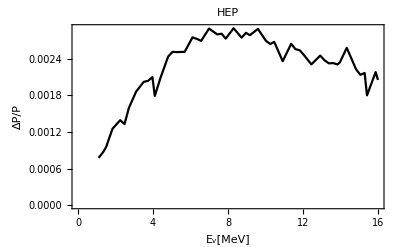

```mathematica
ListPlot[Table[{Phep[[i,1]],Abs[((Phep-HEPdata)/(Phep+HEPdata))[[All,2]][[i]]]},{i,Length[Phep]}],Joined->True, Frame->True,FrameLabel->{"E_v[MeV]","ΔP/P"}, PlotLabel->"HEP",PlotStyle->Black]
```

## Earth regeneration

#### Earth and detector radii

```mathematica
rE = 6.371*10^6 ; (* m *)
rDet =rE- 2 10^3 ; (* m *)
```

#### Earth' s density parametrization: 9702343

```mathematica
α={6.099, 5.803, 3.156, -5.376, 11.540};
β = {-4.119, -3.653, -1.459, 19.210, -20.280};
γ = {0, -1.086, 0.280, -12.520, 10.410};
rj = {0, 0.192, 0.546, 0.895, 0.937, 1};
```

Electron density

```mathematica
Ne[r_]=Piecewise[Table[{α[[i]] + β[[i]] r^2 + γ[[i]] r^4,rj[[i]]≤r<rj[[i+1]]},{i,Length[rj]-1}]];
```

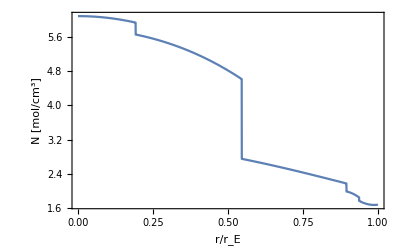

```mathematica
Plot[Ne[r],{r,0,1},Exclusions->None, Frame->True, FrameLabel->{"r/r_E", "N [mol/cm^3]"}]
```

Select the shells that are crossed as a function of the nadir angle η, and the density profile on the related path: 9702343

```mathematica
idx[η_] := Flatten[Position[rj,_?(#>Sin[η]&)]];

αp[η_]:=α[[idx[η]-1]] + β[[idx[η]-1]] Sin[η]^2 + γ[[idx[η]-1]] Sin[η]^4;
βp[η_] := β[[idx[η]-1]] + 2 γ[[idx[η]-1]] Sin[η]^2;
γp[η_] := γ[[idx[η]-1]];
```

Compute the boundaries xj of the crossed shells as a function of the nadir angle η

```mathematica
xj[η_] :=Which[0≤η<Pi/2,Prepend[√(rj[[idx[η]]]^2 - Sin[η]^2),0],Pi/2≤η≤Pi,{0}];
```

Compute the contribution in length Δx of the shell outside the detector radius

```mathematica
Δx[η_] := Piecewise[{{- rDet Cos[η] + √(rE^2-rDet^2 Sin[η]^2),0≤η<Pi/2},{ rDet Cos[η] + √(rE^2-rDet^2 Sin[η]^2),Pi/2≤η≤Pi}}]
```

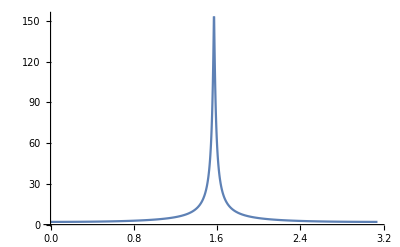

```mathematica
Plot[Δx[η]/10^3,{η,0,Pi},PlotRange->Full]
```

Compute the density along the chord with nadir angle η:

```mathematica
Nchord[η_, x_] := Which[0≤η<Pi/2,Piecewise[Table[{αp[η][[i]] + βp[η][[i]] x^2 + γp[η][[i]] x^4,xj[η][[i]]≤x<xj[η][[i+1]]},{i,Length[xj[η]]-1}]],
Pi/2≤η≤Pi,Ne[rDet/rE]]
```

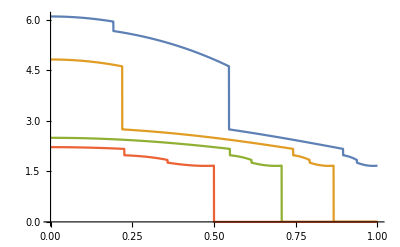

```mathematica
Plot[{Nchord[0,x],Nchord[Pi/6,x],Nchord[Pi/4,x],Nchord[Pi/3,x]},{x,0,1},Exclusions->None]
```

Compute the average density on each shell

```mathematica
Nav[η_] := Module[{x=xj[η]},Which[0≤η<Pi/2,Append[Table[(αp[η][[i]]  + (βp[η][[i]] (x[[i+1]]^3-x[[i]]^3))/(3 (x[[i+1]]-x[[i]])) + (γp[η][[i]] (x[[i+1]]^5-x[[i]]^5))/(5 (x[[i+1]]-x[[i]]))),{i,Length[xj[η]]-1}], Ne[1]],Pi/2≤η≤Pi,Ne[rDet/rE]]]
```

```mathematica
Nconst[η_, x_] := Which[0≤η<Pi/2,Piecewise[Table[{Nav[η][[i]],xj[η][[i]]≤x<xj[η][[i+1]]},{i,Length[xj[η]]-1}]],
Pi/2≤η≤Pi,Ne[rDet/rE]]
```

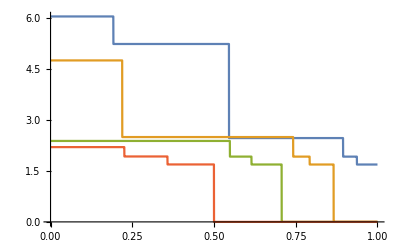

```mathematica
Plot[{Nconst[0,x],Nconst[Pi/6,x],Nconst[Pi/4,x],Nconst[Pi/3,x]},{x,0,1},Exclusions->None]
```

```mathematica
(* 3 flavour formalism, only NO for now *)
```

Define PMNS mixing matrix

```mathematica
R23[th23_] := {{1,0,0},{0, Cos[th23],Sin[th23]},{0,-Sin[th23],Cos[th23]}};
R13[th13_] := {{Cos[th13],0,Sin[th13]},{0, 1,0},{-Sin[th13],0,Cos[th13]}};
R12[th12_] := {{Cos[th12],Sin[th12],0},{-Sin[th12],Cos[th12],0},{0,0,1}};
Δ[δ_]:= DiagonalMatrix[{1,1,Exp[I δ]}];
```

```mathematica
U =R13[th13].R12[th12];
```

```mathematica
PMNS[th12_,th13_,th23_,δ_]:=R23[th23].Δ[δ].R13[th13].Δ[δ]*.R12[th12];
```

Density along a crossed path

```mathematica
Ncross[eta_,x_]:=Piecewise[{{Nchord[eta,x],x≥0},{Nchord[eta,-x],x<0}}]
```

```mathematica
NcrossConst[eta_,x_]:=Piecewise[{{Nconst[eta,x],x≥0},{Nconst[eta,-x],x<0}}]
```

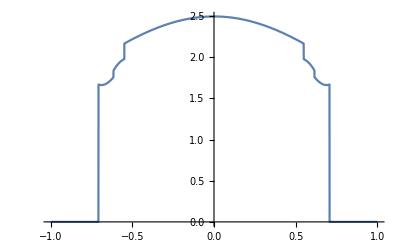

```mathematica
Plot[Ncross[45 Degree,x],{x,-1,1},Exclusions->None]
```

```mathematica
HM[k1_,k2_,k3_,V_]:= FullSimplify[Simplify[U.DiagonalMatrix[{k1,k2,k3}].Uᵀ + DiagonalMatrix[{V,0,0}]]];
T[k1_,k2_,k3_,V_] :=Module[{hm=HM[k1,k2,k3,V]},
FullSimplify[ Simplify[hm - Tr[hm]*IdentityMatrix[3]/3]]];
```

```mathematica
c1[k1_,k2_,k3_,V_,th12_,th13_]:=1/12 (-4 (k1^2-k1 k2+k2^2-(k1+k2) k3+k3^2)+(k1+k2-2 k3) V-4 V^2+6 (-k1+k2) V Cos[2 th12] Cos[th13]^2-3 (k1+k2-2 k3) V Cos[2 th13]);
c0[k1_,k2_,k3_,V_,th12_,th13_]:=1/108 (-4 (k1+k2-2 k3) (2 k1-k2-k3) (k1-2 k2+k3)+3 (k1^2-4 k1 k2+k2^2+2 (k1+k2) k3-2 k3^2) V+3 (k1+k2-2 k3) V^2-8 V^3-18 (k1-k2) V (k1+k2-2 k3+V) Cos[2 th12] Cos[th13]^2-9 V (k1^2+k2^2-2 k3 (k3+V)+k2 (2 k3+V)+k1 (-4 k2+2 k3+V)) Cos[2 th13]);
```

```mathematica
l[c0_,c1_]:={ -(√(-1/3 c1)*Cos[1/3 ArcTan[1/c0 √(-c0^2 - 4/27 c1^3)]] + √-c1 Sin[1/3 ArcTan[1/c0 √(-c0^2 - 4/27 c1^3)]]),
 -( √(-1/3 c1)*Cos[1/3 ArcTan[1/c0 √(-c0^2 - 4/27 c1^3)]] - √-c1 Sin[1/3 ArcTan[1/c0 √(-c0^2 - 4/27 c1^3)]]),
 (2 √(-1/3 c1)Cos[1/3 ArcTan[1/c0 √(-c0^2 - 4/27 c1^3)]] )};
```

```mathematica
U0[k1_,k2_,k3_,V_,th12_,th13_,x2_,x1_] := Module[{nc0=c0[k1,k2,k3,V,th12,th13],nc1=c1[k1,k2,k3,V,th12,th13],L = x2-x1, t = T[k1,k2,k3,V]},
lambda = l[nc0,nc1];
ⅇ^(-1/3 ⅈ L (k1+k2+k3+V)) * Sum[Exp[- I L lambda[[i]]]* 1/(3 lambda[[i]]^2 + nc1)*((lambda[[i]]^2 + nc1)*IdentityMatrix[3] + lambda[[i]]*t + t.t),{i,3}]];
M[k1_,k2_,k3_,V_,th12_,th13_] := Module[{nc0=c0[k1,k2,k3,V,th12,th13],nc1=c1[k1,k2,k3,V,th12,th13],t = T[k1,k2,k3,V]},

lambda = l[nc0,nc1];Table[1/(3 lambda[[i]]^2 + nc1)*((lambda[[i]]^2 + nc1)*IdentityMatrix[3] + lambda[[i]]*t + t.t),{i,3}]]
```

```mathematica
Iab[la_,lb_,aprime_, b_, c_, xi_,xf_]:=Module[{dl=la-lb},
Which[la==lb,0,
Abs[dl/(la+lb)]<10^-2,
((* aprime (xf-xi)+1/3 b (xf^3-xi^3)+1/5 c (xf^5-xi^5)+ *)dl (-1/2 ⅈ aprime (xf-xi)^2-1/12 ⅈ b (xf^4-4 xf xi^3+3 xi^4)-1/30 ⅈ c (xf^6-6 xf xi^5+5 xi^6))+dl^2 (-1/6 aprime (xf-xi)^3-1/60 b (xf^5-10 xf^2 xi^3+15 xf xi^4-6 xi^5)-1/210 c (xf^7-21 xf^2 xi^5+35 xf xi^6-15 xi^7)))*ⅇ^(ⅈ lb (-xf+xi)),
True,(aprime*(-ⅈ+ⅈ ⅇ^(-ⅈ dl (xf-xi)))/dl + b*(2 ⅈ+2 dl xf-ⅈ dl^2 xf^2+ⅈ ⅇ^(-ⅈ dl (xf-xi)) (-2+2 ⅈ dl xi+dl^2 xi^2))/dl^3 + c*(-ⅈ (24+dl xf (-24 ⅈ+dl xf (-12+dl xf (4 ⅈ+dl xf)))-ⅇ^(-ⅈ dl (xf-xi)) (24+dl xi (-24 ⅈ+dl xi (-12+dl xi (4 ⅈ+dl xi))))))/dl^5)*ⅇ^(ⅈ lb (-xf+xi))]];
```

```mathematica
U1[k1_,k2_,k3_,V_,th12_,th13_,x2_,x1_,αp_, β_, γ_] := Module[{nc0=c0[k1,k2,k3,V,th12,th13],nc1=c1[k1,k2,k3,V,th12,th13],t = T[k1,k2,k3,V], m=M[k1,k2,k3,V,th12,th13]},
lambda = l[nc0,nc1];- I *Sum[m[[a]].DiagonalMatrix[{Iab[ lambda[[a]]+1/3* (k1+k2+k3+V) , lambda[[b]]+1/3* (k1+k2+k3+V),αp, β, γ, x1,x2],0,0}].m[[b]],{a,3},{b,3}]]
```

```mathematica
UNon[th13_,th12_,Δms21_,Δms3l_,E_,η_] := Module[{x=xj[η],dens=Nav[η], ap = αp[η]-Nav[η][[1;;Length[αp[η]]]],bp=βp[η],cp=γp[η]},
Which[0≤η<Pi/2,Table[U0[0,rE k[Δms21,E],rE k[Δms3l,E],rE V[dens[[i]] * mol/cm^3],th12,th13,x[[i+1]],x[[i]]],{i,Length[x]-1}],
Pi/2≤η≤Pi,MatrixExp[-I rE((Δx[η]/rE)*h0 +DiagonalMatrix[{ V[Nint[η]*mol/cm^3],0,0}])]]]
```

```mathematica
Upert[th13_,th12_,Δms21_,Δms3l_,E_,η_] := Module[{x=xj[η],dens=Nav[η], ap = αp[η]-Nav[η][[1;;Length[αp[η]]]],bp=βp[η],cp=γp[η]},
Which[0≤η<Pi/2,Table[U0[0,rE k[Δms21,E],rE k[Δms3l,E],rE V[dens[[i]] * mol/cm^3],th12,th13,x[[i+1]],x[[i]]]+U1[0,rE k[Δms21,E],rE k[Δms3l,E],rE V[dens[[i]] * mol/cm^3],th12,th13,x[[i+1]],x[[i]], ap[[i]], bp[[i]], cp[[i]]],{i,Length[x]-1}],
Pi/2≤η≤Pi,MatrixExp[-I rE((Δx[η]/rE)*h0 +DiagonalMatrix[{ V[Nint[η]*mol/cm^3],0,0}])]]]
```

```mathematica
(* {th12,th13}=RandomReal[{0,2Pi},2];
{k1,k2,k3,L,v}=RandomReal[{0,1},5] *)
```

Test agreement of Magnus expansion with numerical evolution

```mathematica
r23 := R23[th23];
Delta := Δ[d];
```

```mathematica
Htilde[th13_,th12_,Δms21_,Δms3l_,E_, n_] := Module[{r13=R13[th13],r12=R12[th12]},Chop[m*(r13.r12.DiagonalMatrix[{0, k[Δms21,E],k[Δms3l,E]}].r12ᵀ.r13ᵀ+DiagonalMatrix[{V[n],0,0}])]]
```

```mathematica
U
```

{{Cos[th12] Cos[th13],Cos[th13] Sin[th12],Sin[th13]},{-Sin[th12],Cos[th12],0},{-Cos[th12] Sin[th13],-Sin[th12] Sin[th13],Cos[th13]}}

```mathematica
(* Set m=1 to solve numerical equation *)
m=1;
```

```mathematica
th12=33.44 Degree;
th23=49 Degree;
th13=8.57 Degree;
d = 195 Degree;
dm12= 7.42 10^-5 eV^2;
dm3l=2.514 10^-3 eV^2;
```

```mathematica
v0 = Normalize[RandomComplex[{-1-I,1+I},3]];
v0=PMNS[th12,th13,th23,d][[;;,2]]*;
eta=RandomReal[{0,90}] Degree;
energy = RandomReal[{1,20}] MeV;
eta=0;
energy=10 MeV; 
{eta/Degree, energy}
{t1,t2} = {-Last[xj[eta]],Last[xj[eta]]};
 {t1,t2}={rj[[2]],rj[[3]]}; 
s = Timing[NDSolve[{D[{nue[x],numu[x],nutau[x]},x] == - I(rE*m*r23.Delta*.Htilde[th13,th12,dm12, dm3l ,energy,Ncross[eta,x]mol/cm^3 ].Delta.r23ᵀ).{nue[x],numu[x],nutau[x]},{nue[t1],numu[t1],nutau[t1]}==v0},{nue,numu,nutau},{x,t1,t2}]]
s=s[[2]];
s0 = Timing[NDSolve[{D[{nue[x],numu[x],nutau[x]},x] == - I(rE*m*r23.Delta*.Htilde[th13,th12,dm12, dm3l ,energy,NcrossConst[eta,x]mol/cm^3 ].Delta.r23ᵀ).{nue[x],numu[x],nutau[x]},{nue[t1],numu[t1],nutau[t1]}==v0},{nue,numu,nutau},{x,t1,t2}]];
s0=s0[[2]];
```

{0,10 MeV}

{0.218053,{{nue→InterpolatingFunction[…],numu→InterpolatingFunction[…],nutau→InterpolatingFunction[…]}}}

```mathematica
OneAn = Timing[temp={Upert[th13,th12,dm12, dm3l,energy,eta][[2]]};
evolutorhalf = If[SquareMatrixQ[temp],temp[[1]],Apply[Dot,temp]];
r23.Delta*.evolutorhalfᵀ.Delta.r23ᵀ.v0]
Abs[%[[2]]]^2
```

{0.052853,{0.618963+0.0829216 ⅈ,0.574911+0.0584029 ⅈ,-0.518353-0.08594 ⅈ}}

{0.389991,0.333934,0.276076}

```mathematica
OneNum = Evaluate[{nue[t2],numu[t2],nutau[t2]}/.s]
Abs[%]^2
```

{{0.61809+0.083228 ⅈ,0.57527+0.0580478 ⅈ,-0.519072-0.0854195 ⅈ}}

{{0.388962,0.334305,0.276732}}

```mathematica
ZeroAn = Timing[temp={(UNon[th13,th12,dm12, dm3l,energy,eta])[[2]]};
evolutorhalf = If[SquareMatrixQ[temp],temp[[1]],Apply[Dot,temp]];
r23.Delta*.evolutorhalfᵀ.Delta.r23ᵀ.v0]
Abs[%[[2]]]^2
```

{0.018807,{0.619522+0.0831787 ⅈ,0.574674+0.0582882 ⅈ,-0.517943-0.085797 ⅈ}}

{0.390726,0.333648,0.275626}

```mathematica
evolutorhalf//MatrixForm
```

(-0.307481-0.0270806 ⅈ | 0.935353+0.125945 ⅈ | -0.0798093+0.0872077 ⅈ
0.935353+0.125945 ⅈ | 0.295543+0.0393068 ⅈ | -0.141419-0.0190377 ⅈ
-0.0798093+0.0872077 ⅈ | -0.141419-0.0190377 ⅈ | -0.823262+0.536565 ⅈ)

```mathematica
ZeroNum = Evaluate[{nue[t2],numu[t2],nutau[t2]}/.s0]
Abs[%]^2
```

{{0.61953+0.0831789 ⅈ,0.574632+0.0582984 ⅈ,-0.51798-0.0857881 ⅈ}}

{{0.390737,0.333601,0.275663}}

```mathematica
{Norm[ZeroAn[[2]]-ZeroNum[[1]]],Norm[ZeroAn[[2]]-OneNum[[1]]],Norm[OneAn[[2]]-OneNum[[1]]]}
```

{0.000058055,0.00197021,0.00137734}

```mathematica
(* Probably some inconsistency with dimensionful quantities; try to implement directly in Python *)
```

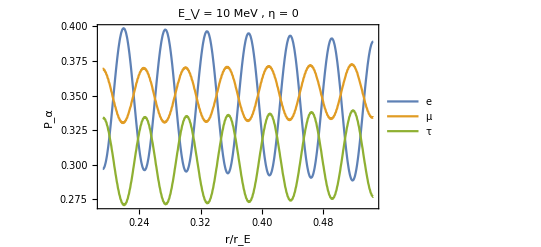

```mathematica
Plot[Evaluate[Abs[{nue[x],numu[x],nutau[x]}/.s]^2],{x,t1,t2},PlotLegends->{"e","μ","τ"}, Frame->True, FrameLabel->{"r/r_E","P_α"},PlotLabel->"E_⋁ = "<>ToString[energy]<>" ,  η = "<>ToString[eta]]
```

```mathematica
MatrixExp[- I rE Htilde[th13,th12,dm12, dm3l ,energy,Nav[0][[1]]mol/cm^3 ]]//MatrixForm
```

(-0.435348+0.538799 ⅈ | 0.662092+0.26967 ⅈ | 0.0649185+0.0697568 ⅈ
0.662092+0.26967 ⅈ | -0.0506+0.688955 ⅈ | -0.100148-0.0407882 ⅈ
0.0649185+0.0697568 ⅈ | -0.100148-0.0407882 ⅈ | -0.0159512+0.98943 ⅈ)

```mathematica
Htilde[th13,th12,dm12, dm3l ,energy,mol/cm^3]//MatrixForm
```

(0.0000201084 | 8.54617×10^-6 | 0.0000929933
8.54617×10^-6 | 0.0000130874 | -1.28791×10^-6
0.0000929933 | -1.28791×10^-6 | 0.000622782)

```mathematica
U.HM[0, k[dm12,energy],k[dm3l,energy],V[mol/cm^3]].Uᵀ//MatrixForm
```

(0.000061752 | -7.67082×10^-6 | 0.000161437
-7.67082×10^-6 | 7.35969×10^-6 | -0.0000517547
0.000161437 | -0.0000517547 | 0.000586866)

```mathematica
U.U0[0,rE k[dm12,energy],rE k[dm3l,energy],rE V[Nav[0][[1]]mol/cm^3] ,th12,th13,1,0].Uᵀ//MatrixForm
```

(0.283302+0.846426 ⅈ | 0.414236+0.162183 ⅈ | -0.0461135+0.0572833 ⅈ
0.414236+0.162183 ⅈ | -0.776352+0.395346 ⅈ | -0.183117-0.097736 ⅈ
-0.0461135+0.0572833 ⅈ | -0.183117-0.097736 ⅈ | -0.00884874+0.975413 ⅈ)

```mathematica
MatrixForm[evolutorhalf]
```

(-0.307481-0.0270806 ⅈ | 0.935353+0.125945 ⅈ | -0.0798093+0.0872077 ⅈ
0.935353+0.125945 ⅈ | 0.295543+0.0393068 ⅈ | -0.141419-0.0190377 ⅈ
-0.0798093+0.0872077 ⅈ | -0.141419-0.0190377 ⅈ | -0.823262+0.536565 ⅈ)

Here I change the oscillation parameters to reproduce a SNO example

```mathematica
th12 = √ArcTan[0.469];
th13 = √ArcSin[0.01];
dm12 = 7.9 10^-5 eV^2;
dm3l = 2.46 10^-3 eV^2;
```

```mathematica
B8dataHorizon = Import[NotebookDirectory[]<>"Functions/Data/B8horizon.csv"];
PB8new=Table[{e,NIntegrate[Pveve[ArcTan[√0.469],ArcSin[√0.01],7.9 10^-5 eV^2,2.46 10^-3 eV^2,e*MeV,density[r]]*B8radial[r]/B8int,{r,0,0.5}]},{e,B8dataHorizon[[All,1]]}];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {0.0449141}. NIntegrate obtained 0.525076 and 1.09284×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {0.0449141}. NIntegrate obtained 0.519992 and 1.15751×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {0.0449141}. NIntegrate obtained 0.515635 and 1.06582×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

```mathematica
PeesolarHorizon[energy_] := Module[{temp=MatrixExp[-I rE((Δx[Pi/2]/rE)*Htilde0[th13,th12,dm12,dm3l,energy MeV] +DiagonalMatrix[{ V[1.35*Δx[Pi/2]/rE*mol/cm^3],0,0}])]},
Abs[(r23.Delta.temp.Delta*.r23ᵀ.(PMNS[th12,th13,th23,d][[;;,2]]))[[1]]]^2];
```

```mathematica
avgcos2th12[e_]:=NIntegrate[Cos[2 th12M[th12,th13, dm12,dm3l,e*MeV,density[r]]]*B8radial[r],{r,0,0.5}]/B8int;
```

```mathematica
Night[e_] :=-Cos[th13]^2 * avgcos2th12[e]*(PeesolarHorizon[e] - Abs[PMNS[th12,th13,th23,d][[1,2]]]^2);
```

```mathematica
PB8horizon= Table[{PB8new[[i,1]],PB8new[[i,2]] + Night[PB8new[[i,1]]]},{i, Length[PB8new]} ];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {0.0371016}. NIntegrate obtained 0.000029626 and 1.08359×10^-9 for the integral and error estimates.

MatrixExp::eivn: Incorrect number 0 of eigenvectors for eigenvalue (0.-239437. ⅈ) (1.7406×10^-7+1. Htilde0[0.100001,0.662225,0.000079 eV^2,0.00246 eV^2,1.0105 MeV])-0.5 √((-0.00694768+1.30104×10^-18 ⅈ)+26610.3 Htilde0[«20»,«3»,«19» MeV]-(2.2932×10^11-0.0000280836 ⅈ) Htilde0[0.100001,«3»,«1»]^2) with multiplicity 1.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {0.0371016}. NIntegrate obtained 0.0000178116 and 1.19959×10^-9 for the integral and error estimates.

MatrixExp::eivn: Incorrect number 0 of eigenvectors for eigenvalue (0.-239437. ⅈ) (1.7406×10^-7+1. Htilde0[0.100001,0.662225,0.000079 eV^2,0.00246 eV^2,1.17415 MeV])-0.5 √((-0.00694768+1.30104×10^-18 ⅈ)+26610.3 Htilde0[«20»,«3»,«19» MeV]-(2.2932×10^11-0.0000280836 ⅈ) Htilde0[0.100001,«3»,«1»]^2) with multiplicity 1.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {0.0371016}. NIntegrate obtained 7.79343×10^-6 and 1.25032×10^-9 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

MatrixExp::eivn: Incorrect number 0 of eigenvectors for eigenvalue (0.-239437. ⅈ) (1.7406×10^-7+1. Htilde0[0.100001,0.662225,0.000079 eV^2,0.00246 eV^2,1.31247 MeV])-0.5 √((-0.00694768+1.30104×10^-18 ⅈ)+26610.3 Htilde0[«20»,«3»,«19» MeV]-(2.2932×10^11-0.0000280836 ⅈ) Htilde0[0.100001,«3»,«1»]^2) with multiplicity 1.

General::stop: Further output of MatrixExp::eivn will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

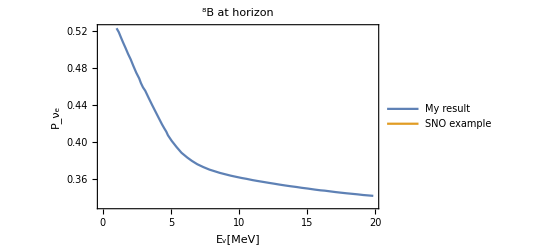

```mathematica
ListPlot[{B8dataHorizon,PB8horizon},Joined->True, Frame->True,FrameLabel->{"E_v[MeV]","P_ν_e"}, PlotLabel->"^8B at horizon",PlotLegends->Placed[{"My result","SNO example"},{Right,Top}]]
```

```mathematica
ListPlot[Table[{PB8horizon[[i,1]],Abs[((PB8horizon-B8dataHorizon)/(PB8horizon+B8dataHorizon))[[All,2]][[i]]]},{i,Length[PB8horizon]}],Joined->True, Frame->True,FrameLabel->{"E_v[MeV]","ΔP/P"}, PlotLabel->"^8B",PlotStyle->Black]
```

-Graphics-

## SNO energy spectra

```mathematica
ND = Around[6.0082,0.0062] 10^31 / (10^6 g);
Rfiducial = 550 cm;
SNOdensity = Around[1.10563,0.00010] g / cm^3;
```

```mathematica
NDfiducial = ND*(4/3 Pi Rfiducial^3) * SNOdensity
```

4.6290.00510^34

```mathematica
livetimeAll = Import[NotebookDirectory[]<>"Data/SNO phase 1/SnoCosZenith.dat"];
livetime = livetimeAll[[10;;, ;;]];
```

Import::nffil: File /Users/michele/Coding/solar-nu-flux/Code/Data/SNO phase 1/SnoCosZenith.dat not found during Import.

Part::take: Cannot take positions 10 through -1 in $Failed.

```mathematica
MatrixForm[livetimeAll[[1;;6]]]
```

Part::take: Cannot take positions 1 through 6 in $Failed.

$Failed⟦1;;6⟧

```mathematica
zenithList = Subdivide[-1,1,Length[livetime]-1];
livetimeFull = Table[{zenithList[[i]],Pi - ArcCos[zenithList[[i]]],livetime[[i]][[1]]},{i,Length[livetime]}];
```

Part::partd: Part specification $Failed⟦1⟧ is longer than depth of object.

```mathematica
(* η = π − Subscript[θ, z] *)
```

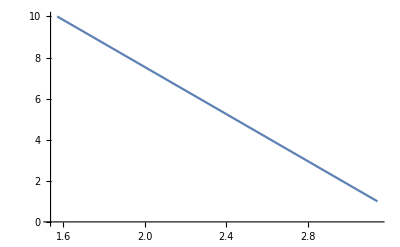

```mathematica
ListPlot[livetimeFull[[;;,2;;3]],Joined->True]
```

```mathematica
B8shapeData = Import[NotebookDirectory[]<>"Data/SNO phase 1/0003006.csv"];
Do[B8shapeData[[i,2]]=Max[0,B8shapeData[[i,2]]],{i,Length[B8shapeData]}];
B8shape = Interpolation[B8shapeData,InterpolationOrder->1];
```

Import::nffil: File /Users/michele/Coding/solar-nu-flux/Code/Data/SNO phase 1/0003006.csv not found during Import.

Interpolation::innd: First argument in $Failed does not contain a list of data and coordinates.

```mathematica
LogLogPlot[B8shape[e],{e,First[B8shapeData][[1]],Last[B8shapeData][[1]]}]
```

First::normal: Nonatomic expression expected at position 1 in First[$Failed].

General::stop: Further output of First::normal will be suppressed during this calculation.

Last::normal: Nonatomic expression expected at position 1 in Last[$Failed].

Plot::plln: Limiting value $Failed in {e,$Failed,$Failed} is not a machine-sized real number.

Last::normal: Nonatomic expression expected at position 1 in Last[$Failed].

Plot::plln: Limiting value $Failed in {e,$Failed,$Failed} is not a machine-sized real number.

LogLogPlot[B8shape[e],{e,First[B8shapeData]⟦1⟧,Last[B8shapeData]⟦1⟧}]

```mathematica
NIntegrate[B8shape[e],{e,First[B8shapeData][[1]],Last[B8shapeData][[1]]}]
```

First::normal: Nonatomic expression expected at position 1 in First[$Failed].

Last::normal: Nonatomic expression expected at position 1 in Last[$Failed].

First::normal: Nonatomic expression expected at position 1 in First[$Failed].

Last::normal: Nonatomic expression expected at position 1 in Last[$Failed].

0.

```mathematica
CCCrossSectionData = Import[NotebookDirectory[]<>"Data/SNO phase 1/0008032TableII.csv"];
```

Import::nffil: File /Users/michele/Coding/solar-nu-flux/Code/Data/SNO phase 1/0008032TableII.csv not found during Import.

```mathematica
L1A = 5.6; (* fm^3 *)
CCCrossSection = Interpolation[Table[{CCCrossSectionData[[i,1]],CCCrossSectionData[[i,2]] + L1A * CCCrossSectionData[[i,3]]},{i,Length[CCCrossSectionData]}],InterpolationOrder->1] (* 10^-42 cm^2 *)
```

Interpolation::innd: First argument in {} does not contain a list of data and coordinates.

Interpolation[{},InterpolationOrder→1]

```mathematica
Plot[CCCrossSection[e],{e,First[CCCrossSectionData][[1]],Last[CCCrossSectionData][[1]]}]
```

First::normal: Nonatomic expression expected at position 1 in First[$Failed].

General::stop: Further output of First::normal will be suppressed during this calculation.

Last::normal: Nonatomic expression expected at position 1 in Last[$Failed].

Plot::plln: Limiting value $Failed in {e,$Failed,$Failed} is not a machine-sized real number.

Plot[CCCrossSection[e],{e,First[CCCrossSectionData]⟦1⟧,Last[CCCrossSectionData]⟦1⟧}]

```mathematica
σT[Te_] := -0.0684 + 0.331 √Te + 0.0425 Te;
ΔT = 0;
CCDetectorResponse[Teff_, Te_] :=1/(√(2Pi) σT[Te]) Exp[-(Teff - Te - ΔT)^2/(2 σT[Te]^2)];
```

```mathematica
CCCrossSectionDetector[Teff_] := NIntegrate[CCCrossSection[Te] CCDetectorResponse[Teff, Te],{Te,0,Infinity}]
```

```mathematica
Plot[{CCCrossSection[e],test[e]},{e,0,20}]
```

Interpolation::innd: First argument in {} does not contain a list of data and coordinates.

General::stop: Further output of Interpolation::innd will be suppressed during this calculation.

-Graphics-

```mathematica
NIntegrate[CCCrossSection[Te] CCDetectorResponse[Teff, Te],{Te,0,Infinity}]
```

NIntegrate::inumr: The integrand (ⅇ^(-(-Te+Teff)^2/(2 («1»)^2)) Interpolation[{},InterpolationOrder→1][Te])/(√(2 π) (-0.0684+0.331 √Te+0.0425 Te)) has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞,0.}}.

NIntegrate[CCCrossSection[Te] CCDetectorResponse[Teff,Te],{Te,0,∞}]

Electron neutrino survival probability as a function of mixing parameters, energy and η

```mathematica
Pee[th12_,th13_,th23_,dm12_, dm3l_,d_,energy_,eta_]:=Module[{temp=Utilde[th13,th12,dm12, dm3l,energy,eta]},
evolutorhalf = If[SquareMatrixQ[temp],temp,Apply[Dot,temp]];
Abs[(r23.Delta.evolutorhalfᵀ.evolutorhalf.Delta*.r23ᵀ.(PMNS[th12,th13,th23,d][[;;,2]]))[[1]]]^2]
```

```mathematica
ListPlot[Table[{energy,Pee[th12,th13,th23,dm12, dm3l,d,energy MeV ,0]},{energy, 0.1,20,0.1}],Joined->True]
```

-Graphics-

```mathematica
Pee[th12,th13,th23,dm12, dm3l,d,energy ,eta]
```

{{1,0,0},{0,Sin[41 °]^2,Cos[41 °]^2},{0,Cos[41 °]^2,Sin[41 °]^2}}

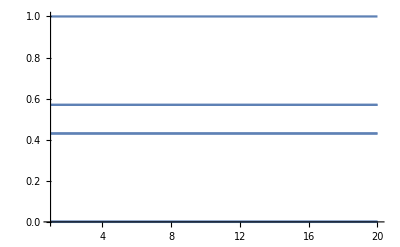

```mathematica
Plot[Pee[th12,th13,th23,dm12, dm3l,d,energy MeV,0],{energy,1 ,20}]
```

```mathematica
Pee[th12,th13,th23,dm12, dm3l,d,10 MeV,Pi]
```

{{1,0,0},{0,Sin[41 °]^2,Cos[41 °]^2},{0,Cos[41 °]^2,Sin[41 °]^2}}

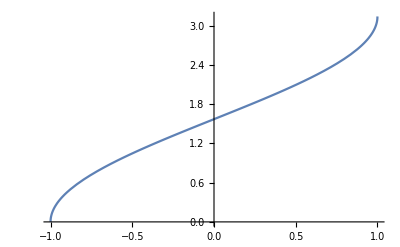

```mathematica
Plot[Pi-ArcCos[cz],{cz,-1 ,1}]
```

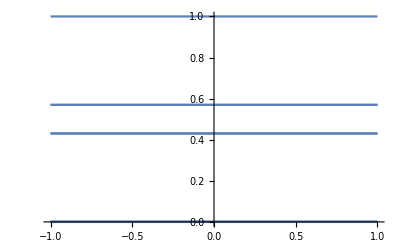

```mathematica
Plot[Pee[th12,th13,th23,dm12, dm3l,d,10 MeV,Pi - ArcCos[cz]],{cz,-1 ,1}]
```

```mathematica
eta
```

0

```mathematica
temp=Utilde[th13,th12,dm12, dm3l,energy,eta];
evolutorhalf = If[SquareMatrixQ[temp],temp,Apply[Dot,temp]];
r23.Delta.evolutorhalfᵀ.evolutorhalf.Delta*.r23ᵀ.(PMNS[th12,th13,th23,d][[;;,2]])
```

{{1,0,0},{0,Sin[41 °],ⅇ^(195 ⅈ °) Cos[41 °]},{0,-Cos[41 °],ⅇ^(195 ⅈ °) Sin[41 °]}}.Transpose[0.100001.0.662225.(0.000079 eV^2).(0.00246 eV^2).(10 MeV).0].0.100001.0.662225.(0.000079 eV^2).(0.00246 eV^2).(10 MeV).0.{0.611801+0. ⅈ,0.788626+0. ⅈ,-0.0613854+2.77556×10^-17 ⅈ}

```mathematica
energy
```

10 MeV

```mathematica
Table[{zenithList[[i]],livetime[[i]][[1]]},{i,Length[livetime]}]
```

Part::partd: Part specification $Failed⟦1⟧ is longer than depth of object.

{{-1,$Failed⟦1⟧},{0,10},{1,1}}

```mathematica
Plot[PeesolarHorizon[e],{e,1,20}]
```

MatrixExp::eivn: Incorrect number 0 of eigenvectors for eigenvalue (0.-239437. ⅈ) (1.7406×10^-7+1. Htilde0[0.100001,0.662225,0.000079 eV^2,0.00246 eV^2,1.00039 MeV])-0.5 √((-0.00694768+1.30104×10^-18 ⅈ)+26610.3 Htilde0[«20»,«3»,«19» MeV]-(2.2932×10^11-0.0000280836 ⅈ) Htilde0[0.100001,«3»,«1»]^2) with multiplicity 1.

-Graphics-

```mathematica
PB8Horizon=Table[{e,NIntegrate[Pveve[ArcTan[√0.469],ArcSin[√0.01],7.9 10^-5 eV^2,2.46 10^-3 eV^2,e*MeV,density[r]]*B8radial[r]/B8int,{r,0,0.5}]},{e,B8data[[All,1]]}];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {0.0449141}. NIntegrate obtained 0.524036 and 1.03833×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {0.0449141}. NIntegrate obtained 0.519144 and 1.09452×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {0.0449141}. NIntegrate obtained 0.514518 and 1.07358×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

```mathematica
temp=Utilde[th13,th12,dm12, dm3l,20 MeV,Pi/2];
evolutorhalf = If[SquareMatrixQ[temp],temp,Apply[Dot,temp]];
r23.Delta.evolutorhalfᵀ.evolutorhalf.Delta*.r23ᵀ.(PMNS[th12,th13,th23,d][[;;,2]])
Abs[%[[2]]]^2
```

{{1,0,0},{0,Sin[41 °],ⅇ^(195 ⅈ °) Cos[41 °]},{0,-Cos[41 °],ⅇ^(195 ⅈ °) Sin[41 °]}}.Transpose[0.100001.0.662225.(0.000079 eV^2).(0.00246 eV^2).(20 MeV).π/2].0.100001.0.662225.(0.000079 eV^2).(0.00246 eV^2).(20 MeV).π/2.{0.611801+0. ⅈ,0.788626+0. ⅈ,-0.0613854+2.77556×10^-17 ⅈ}

Abs[Transpose[0.100001.0.662225.(0.000079 eV^2).(0.00246 eV^2).(20 MeV).π/2]]^2

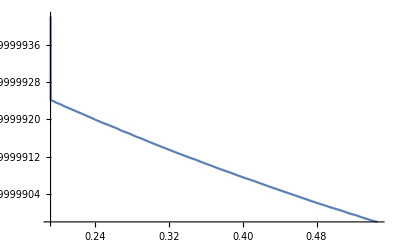

```mathematica
Plot[Evaluate[Abs[nue[x]]^2+Abs[numu[x]]^2+Abs[nutau[x]]^2/.s],{x,t1,t2}]
```

```mathematica
rE^2/60 V[0.192^4(5 β[[1]]+2γ[[1]](2 0.192^2))*mol/cm^3]*Htilde2[th13,th12,10^-5 eV^2, 10^-3 eV^2,10 MeV]
```

-7323.47 Htilde2[0.100001,0.662225,eV^2/100000,eV^2/1000,10 MeV]

```mathematica
(0.192 rE*Htilde[th13,th12,10^-5 eV^2, 10^-3 eV^2,10 MeV,n0int[0.192]*mol/cm^3])
```

{{1.22323×10^6 (3.47271×10^-6+3.868×10^-7 n0int[0.192]),1.49495,30.6622},{1.49495,1.92702,-0.149996},{30.6622,-0.149996,306.768}}

```mathematica
Timing[(MatrixExp[- I(0.192 rE*Htilde[th13,th12,10^-5 eV^2, 10^-3 eV^2,10 MeV,n0int[0.192]*mol/cm^3])-rE^2/60 V[0.192^4(5 β[[1]]+2γ[[1]](2 0.192^2))*mol/cm^3]*Htilde2[th13,th12,10^-5 eV^2, 10^-3 eV^2,10 MeV]].(PMNS[th12,th13,th23,d]†[[2,;;]]))]
```

{0.148608,{(-2.57821×10^-14-1.2087×10^-12 ⅈ) RootSum[(4.8928×10^11+0. ⅈ) Htilde2[0.100001,0.662225,eV^2/100000,eV^2/1000,10 MeV]+(0.+1. ⅈ) Htilde2[0.100001,0.662225,eV^2/100000,eV^2/1000,10 MeV]^2-(0.+2.3462×10^9 ⅈ) n0int[0.192]+(8.98161×10^12+0. ⅈ) Htilde2[0.100001,0.662225,eV^2/100000,eV^2/1000,10 MeV] n0int[0.192]-(8.05338×10^9+0. ⅈ) #1-(0.+3.45179×10^13 ⅈ) Htilde2[0.100001,0.662225,eV^2/100000,eV^2/1000,10 MeV] #1-(1.22522×10^9+0. ⅈ) n0int[0.192] #1-(0.+5.81343×10^10 ⅈ) Htilde2[0.100001,0.662225,eV^2/100000,eV^2/1000,10 MeV] n0int[0.192] #1+(0.+2.62516×10^9 ⅈ) #1^2-(1.84301×10^11+0. ⅈ) Htilde2[0.100001,0.662225,eV^2/100000,eV^2/1000,10 MeV] #1^2+(0.+3.96904×10^6 ⅈ) n0int[0.192] #1^2+(8.38861×10^6+0. ⅈ) #1^3&,((-3.10849×10^10+0. ⅈ) ⅇ^#1-(0.+1.36506×10^14 ⅈ) ⅇ^#1 Htilde2[0.100001,0.662225,eV^2/100000,eV^2/1000,10 MeV]+1. ⅇ^#1 Htilde2[0.100001,0.662225,eV^2/100000,eV^2/1000,10 MeV]^2+(0.+1.00324×10^8 ⅈ) ⅇ^#1 #1-4.9147×10^11 ⅇ^#1 Htilde2[0.100001,0.662225,eV^2/100000,eV^2/1000,10 MeV] #1)/((0.-0.138531 ⅈ)+(593.761+0. ⅈ) Htilde2[0.100001,0.662225,eV^2/100000,eV^2/1000,10 MeV]-(0.+0.0210757 ⅈ) n0int[0.192]+(1.+0. ⅈ) Htilde2[0.100001,0.662225,eV^2/100000,eV^2/1000,10 MeV] n0int[0.192]-(0.0903136+0. ⅈ) #1-(0.+6.34054 ⅈ) Htilde2[0.100001,0.662225,eV^2/100000,eV^2/1000,10 MeV] #1-(0.000136547+0. ⅈ) n0int[0.192] #1+(0.+0.000432891 ⅈ) #1^2)&]-(2.24121×10^-14-1.19612×10^-12 ⅈ) RootSum[(4.8928×10^11+0. ⅈ) Htilde2[0.100001,0.662225,eV^2/100000,eV^2/1000,10 MeV]+(0.+1. ⅈ) Htilde2[0.100001,0.662225,eV^2/100000,eV^2/1000,10 MeV]^2-(0.+2.3462×10^9 ⅈ) n0int[0.192]+(8.98161×10^12+0. ⅈ) Htilde2[0.100001,0.662225,eV^2/100000,eV^2/1000,10 MeV] n0int[0.192]-(8.05338×10^9+0. ⅈ) #1-(0.+3.45179×10^13 ⅈ) Htilde2[0.100001,0.662225,eV^2/100000,eV^2/1000,10 MeV] #1-(1.22522×10^9+0. ⅈ) n0int[0.192] #1-(0.+5.81343×10^10 ⅈ) Htilde2[0.100001,0.662225,eV^2/100000,eV^2/1000,10 MeV] n0int[0.192] #1+(0.+2.62516×10^9 ⅈ) #1^2-(1.84301×10^11+0. ⅈ) Htilde2[0.100001,0.662225,eV^2/100000,eV^2/1000,10 MeV] #1^2+(0.+3.96904×10^6 ⅈ) n0int[0.192] #1^2+(8.38861×10^6+0. ⅈ) #1^3&,((-3.98029×10^9+0. ⅈ) ⅇ^#1-(0.+1.53556×10^13 ⅈ) ⅇ^#1 Htilde2[0.100001,0.662225,eV^2/100000,eV^2/1000,10 MeV]+1. ⅇ^#1 Htilde2[0.100001,0.662225,eV^2/100000,eV^2/1000,10 MeV]^2+(0.+2.05771×10^9 ⅈ) ⅇ^#1 #1-4.9147×10^11 ⅇ^#1 Htilde2[0.100001,0.662225,eV^2/100000,eV^2/1000,10 MeV] #1)/((0.-0.138531 ⅈ)+(593.761+0. ⅈ) Htilde2[0.100001,0.662225,eV^2/100000,eV^2/1000,10 MeV]-(0.+0.0210757 ⅈ) n0int[0.192]+(1.+0. ⅈ) Htilde2[0.100001,0.662225,eV^2/100000,eV^2/1000,10 MeV] n0int[0.192]-(0.0903136+0. ⅈ) #1-(0.+6.34054 ⅈ) Htilde2[0.100001,0.662225,eV^2/100000,eV^2/1000,10 MeV] #1-(0.000136547+0. ⅈ) n0int[0.192] #1+(0.+0.000432891 ⅈ) #1^2)&]+(0.203934+0. ⅈ) RootSum[(4.8928×10^11+0. ⅈ) Htilde2[0.100001,0.662225,eV^2/100000,eV^2/1000,10 MeV]+(0.+1. ⅈ) Htilde2[0.100001,0.662225,eV^2/100000,eV^2/1000,10 MeV]^2-(0.+2.3462×10^9 ⅈ) n0int[0.192]+(8.98161×10^12+0. ⅈ) Htilde2[0.100001,0.662225,eV^2/100000,eV^2/1000,10 MeV] n0int[0.192]-(8.05338×10^9+0. ⅈ) #1-(0.+3.45179×10^13 ⅈ) Htilde2[0.100001,0.662225,eV^2/100000,eV^2/1000,10 MeV] #1-(1.22522×10^9+0. ⅈ) n0int[0.192] #1-(0.+5.81343×10^10 ⅈ) Htilde2[0.100001,0.662225,eV^2/100000,eV^2/1000,10 MeV] n0int[0.192] #1+(0.+2.62516×10^9 ⅈ) #1^2-(1.84301×10^11+0. ⅈ) Htilde2[0.100001,0.662225,eV^2/100000,eV^2/1000,10 MeV] #1^2+(0.+3.96904×10^6 ⅈ) n0int[0.192] #1^2+(8.38861×10^6+0. ⅈ) #1^3&,((-591.126+0. ⅈ) ⅇ^#1-(0.+2.26292×10^6 ⅈ) ⅇ^#1 Htilde2[0.100001,0.662225,eV^2/100000,eV^2/1000,10 MeV]-2.23517×10^-8 ⅇ^#1 Htilde2[0.100001,0.662225,eV^2/100000,eV^2/1000,10 MeV]^2+(0.+1.81899×10^-12 ⅈ) ⅇ^#1 Htilde2[0.100001,0.662225,eV^2/100000,eV^2/1000,10 MeV] n0int[0.192]-(2.77556×10^-17+0. ⅈ) ⅇ^#1 n0int[0.192]^2+(0.+308.695 ⅈ) ⅇ^#1 #1-14646.9 ⅇ^#1 Htilde2[0.100001,0.662225,eV^2/100000,eV^2/1000,10 MeV] #1+ⅇ^#1 #1^2)/(-320.012-(0.+1.37162×10^6 ⅈ) Htilde2[0.100001,0.662225,eV^2/100000,eV^2/1000,10 MeV]-48.686 n0int[0.192]-(0.+2310.05 ⅈ) Htilde2[0.100001,0.662225,eV^2/100000,eV^2/1000,10 MeV] n0int[0.192]+(0.+208.629 ⅈ) #1-14646.9 Htilde2[0.100001,0.662225,eV^2/100000,eV^2/1000,10 MeV] #1+(0.+0.315431 ⅈ) n0int[0.192] #1+1. #1^2)&],(-1.88646×10^-13-3.53473×10^-15 ⅈ) RootSum[(4.8928×10^11+0. ⅈ) Htilde2[0.100001,0.662225,eV^2/100000,eV^2/1000,10 MeV]+(0.+1. ⅈ) Htilde2[0.100001,0.662225,eV^2/100000,eV^2/1000,10 MeV]^2-(0.+2.3462×10^9 ⅈ) n0int[0.192]+(8.98161×10^12+0. ⅈ) Htilde2[0.100001,0.662225,eV^2/100000,eV^2/1000,10 MeV] n0int[0.192]-(8.05338×10^9+0. ⅈ) #1-(0.+3.45179×10^13 ⅈ) Htilde2[0.100001,0.662225,eV^2/100000,eV^2/1000,10 MeV] #1-(1.22522×10^9+0. ⅈ) n0int[0.192] #1-(0.+5.81343×10^10 ⅈ) Htilde2[0.100001,0.662225,eV^2/100000,eV^2/1000,10 MeV] n0int[0.192] #1+(0.+2.62516×10^9 ⅈ) #1^2-(1.84301×10^11+0. ⅈ) Htilde2[0.100001,0.662225,eV^2/100000,eV^2/1000,10 MeV] #1^2+(0.+3.96904×10^6 ⅈ) n0int[0.192] #1^2+(8.38861×10^6+0. ⅈ) #1^3&,((3.11892×10^9+0. ⅈ) ⅇ^#1+(0.+1.37903×10^13 ⅈ) ⅇ^#1 Htilde2[0.100001,0.662225,eV^2/100000,eV^2/1000,10 MeV]+1. ⅇ^#1 Htilde2[0.100001,0.662225,eV^2/100000,eV^2/1000,10 MeV]^2+(4.76272×10^6+0. ⅈ) ⅇ^#1 n0int[0.192]-(0.+2.32537×10^11 ⅈ) ⅇ^#1 Htilde2[0.100001,0.662225,eV^2/100000,eV^2/1000,10 MeV] n0int[0.192]-(0.+1.00661×10^7 ⅈ) ⅇ^#1 #1-4.9147×10^11 ⅇ^#1 Htilde2[0.100001,0.662225,eV^2/100000,eV^2/1000,10 MeV] #1)/(0.0218484+(0.+93.6453 ⅈ) Htilde2[0.100001,0.662225,eV^2/100000,eV^2/1000,10 MeV]+0.00332397 n0int[0.192]+(0.+0.157715 ⅈ) Htilde2[0.100001,0.662225,eV^2/100000,eV^2/1000,10 MeV] n0int[0.192]-(0.+0.0142438 ⅈ) #1+1. Htilde2[0.100001,0.662225,eV^2/100000,eV^2/1000,10 MeV] #1-(0.+0.0000215356 ⅈ) n0int[0.192] #1-0.0000682736 #1^2)&]-(0.+1.31549×10^-12 ⅈ) RootSum[(4.8928×10^11+0. ⅈ) Htilde2[0.100001,0.662225,eV^2/100000,eV^2/1000,10 MeV]+(0.+1. ⅈ) Htilde2[0.100001,0.662225,eV^2/100000,eV^2/1000,10 MeV]^2-(0.+2.3462×10^9 ⅈ) n0int[0.192]+(8.98161×10^12+0. ⅈ) Htilde2[0.100001,0.662225,eV^2/100000,eV^2/1000,10 MeV] n0int[0.192]-(8.05338×10^9+0. ⅈ) #1-(0.+3.45179×10^13 ⅈ) Htilde2[0.100001,0.662225,eV^2/100000,eV^2/1000,10 MeV] #1-(1.22522×10^9+0. ⅈ) n0int[0.192] #1-(0.+5.81343×10^10 ⅈ) Htilde2[0.100001,0.662225,eV^2/100000,eV^2/1000,10 MeV] n0int[0.192] #1+(0.+2.62516×10^9 ⅈ) #1^2-(1.84301×10^11+0. ⅈ) Htilde2[0.100001,0.662225,eV^2/100000,eV^2/1000,10 MeV] #1^2+(0.+3.96904×10^6 ⅈ) n0int[0.192] #1^2+(8.38861×10^6+0. ⅈ) #1^3&,((-3.10849×10^10+0. ⅈ) ⅇ^#1-(0.+1.36506×10^14 ⅈ) ⅇ^#1 Htilde2[0.100001,0.662225,eV^2/100000,eV^2/1000,10 MeV]+1. ⅇ^#1 Htilde2[0.100001,0.662225,eV^2/100000,eV^2/1000,10 MeV]^2+(0.+1.00324×10^8 ⅈ) ⅇ^#1 #1-4.9147×10^11 ⅇ^#1 Htilde2[0.100001,0.662225,eV^2/100000,eV^2/1000,10 MeV] #1)/((0.-0.138531 ⅈ)+(593.761+0. ⅈ) Htilde2[0.100001,0.662225,eV^2/100000,eV^2/1000,10 MeV]-(0.+0.0210757 ⅈ) n0int[0.192]+(1.+0. ⅈ) Htilde2[0.100001,0.662225,eV^2/100000,eV^2/1000,10 MeV] n0int[0.192]-(0.0903136+0. ⅈ) #1-(0.+6.34054 ⅈ) Htilde2[0.100001,0.662225,eV^2/100000,eV^2/1000,10 MeV] #1-(0.000136547+0. ⅈ) n0int[0.192] #1+(0.+0.000432891 ⅈ) #1^2)&]+(0.187378-0.00399687 ⅈ) RootSum[(4.8928×10^11+0. ⅈ) Htilde2[0.100001,0.662225,eV^2/100000,eV^2/1000,10 MeV]+(0.+1. ⅈ) Htilde2[0.100001,0.662225,eV^2/100000,eV^2/1000,10 MeV]^2-(0.+2.3462×10^9 ⅈ) n0int[0.192]+(8.98161×10^12+0. ⅈ) Htilde2[0.100001,0.662225,eV^2/100000,eV^2/1000,10 MeV] n0int[0.192]-(8.05338×10^9+0. ⅈ) #1-(0.+3.45179×10^13 ⅈ) Htilde2[0.100001,0.662225,eV^2/100000,eV^2/1000,10 MeV] #1-(1.22522×10^9+0. ⅈ) n0int[0.192] #1-(0.+5.81343×10^10 ⅈ) Htilde2[0.100001,0.662225,eV^2/100000,eV^2/1000,10 MeV] n0int[0.192] #1+(0.+2.62516×10^9 ⅈ) #1^2-(1.84301×10^11+0. ⅈ) Htilde2[0.100001,0.662225,eV^2/100000,eV^2/1000,10 MeV] #1^2+(0.+3.96904×10^6 ⅈ) n0int[0.192] #1^2+(8.38861×10^6+0. ⅈ) #1^3&,((-362.96+0. ⅈ) ⅇ^#1-(0.+1.82861×10^6 ⅈ) ⅇ^#1 Htilde2[0.100001,0.662225,eV^2/100000,eV^2/1000,10 MeV]-2.23517×10^-8 ⅇ^#1 Htilde2[0.100001,0.662225,eV^2/100000,eV^2/1000,10 MeV]^2-(145.146+0. ⅈ) ⅇ^#1 n0int[0.192]-(0.+3465.07 ⅈ) ⅇ^#1 Htilde2[0.100001,0.662225,eV^2/100000,eV^2/1000,10 MeV] n0int[0.192]+(0.+311.016 ⅈ) ⅇ^#1 #1-14646.9 ⅇ^#1 Htilde2[0.100001,0.662225,eV^2/100000,eV^2/1000,10 MeV] #1+(0.+0.473146 ⅈ) ⅇ^#1 n0int[0.192] #1+ⅇ^#1 #1^2)/(-320.012-(0.+1.37162×10^6 ⅈ) Htilde2[0.100001,0.662225,eV^2/100000,eV^2/1000,10 MeV]-48.686 n0int[0.192]-(0.+2310.05 ⅈ) Htilde2[0.100001,0.662225,eV^2/100000,eV^2/1000,10 MeV] n0int[0.192]+(0.+208.629 ⅈ) #1-14646.9 Htilde2[0.100001,0.662225,eV^2/100000,eV^2/1000,10 MeV] #1+(0.+0.315431 ⅈ) n0int[0.192] #1+1. #1^2)&],(1.9063×10^-13-4.06624×10^-15 ⅈ) RootSum[(4.8928×10^11+0. ⅈ) Htilde2[0.100001,0.662225,eV^2/100000,eV^2/1000,10 MeV]+(0.+1. ⅈ) Htilde2[0.100001,0.662225,eV^2/100000,eV^2/1000,10 MeV]^2-(0.+2.3462×10^9 ⅈ) n0int[0.192]+(8.98161×10^12+0. ⅈ) Htilde2[0.100001,0.662225,eV^2/100000,eV^2/1000,10 MeV] n0int[0.192]-(8.05338×10^9+0. ⅈ) #1-(0.+3.45179×10^13 ⅈ) Htilde2[0.100001,0.662225,eV^2/100000,eV^2/1000,10 MeV] #1-(1.22522×10^9+0. ⅈ) n0int[0.192] #1-(0.+5.81343×10^10 ⅈ) Htilde2[0.100001,0.662225,eV^2/100000,eV^2/1000,10 MeV] n0int[0.192] #1+(0.+2.62516×10^9 ⅈ) #1^2-(1.84301×10^11+0. ⅈ) Htilde2[0.100001,0.662225,eV^2/100000,eV^2/1000,10 MeV] #1^2+(0.+3.96904×10^6 ⅈ) n0int[0.192] #1^2+(8.38861×10^6+0. ⅈ) #1^3&,((3.11892×10^9+0. ⅈ) ⅇ^#1+(0.+1.37903×10^13 ⅈ) ⅇ^#1 Htilde2[0.100001,0.662225,eV^2/100000,eV^2/1000,10 MeV]+1. ⅇ^#1 Htilde2[0.100001,0.662225,eV^2/100000,eV^2/1000,10 MeV]^2+(4.76272×10^6+0. ⅈ) ⅇ^#1 n0int[0.192]-(0.+2.32537×10^11 ⅈ) ⅇ^#1 Htilde2[0.100001,0.662225,eV^2/100000,eV^2/1000,10 MeV] n0int[0.192]-(0.+1.00661×10^7 ⅈ) ⅇ^#1 #1-4.9147×10^11 ⅇ^#1 Htilde2[0.100001,0.662225,eV^2/100000,eV^2/1000,10 MeV] #1)/(0.0218484+(0.+93.6453 ⅈ) Htilde2[0.100001,0.662225,eV^2/100000,eV^2/1000,10 MeV]+0.00332397 n0int[0.192]+(0.+0.157715 ⅈ) Htilde2[0.100001,0.662225,eV^2/100000,eV^2/1000,10 MeV] n0int[0.192]-(0.+0.0142438 ⅈ) #1+1. Htilde2[0.100001,0.662225,eV^2/100000,eV^2/1000,10 MeV] #1-(0.+0.0000215356 ⅈ) n0int[0.192] #1-0.0000682736 #1^2)&]-(0.+1.31549×10^-12 ⅈ) RootSum[(4.8928×10^11+0. ⅈ) Htilde2[0.100001,0.662225,eV^2/100000,eV^2/1000,10 MeV]+(0.+1. ⅈ) Htilde2[0.100001,0.662225,eV^2/100000,eV^2/1000,10 MeV]^2-(0.+2.3462×10^9 ⅈ) n0int[0.192]+(8.98161×10^12+0. ⅈ) Htilde2[0.100001,0.662225,eV^2/100000,eV^2/1000,10 MeV] n0int[0.192]-(8.05338×10^9+0. ⅈ) #1-(0.+3.45179×10^13 ⅈ) Htilde2[0.100001,0.662225,eV^2/100000,eV^2/1000,10 MeV] #1-(1.22522×10^9+0. ⅈ) n0int[0.192] #1-(0.+5.81343×10^10 ⅈ) Htilde2[0.100001,0.662225,eV^2/100000,eV^2/1000,10 MeV] n0int[0.192] #1+(0.+2.62516×10^9 ⅈ) #1^2-(1.84301×10^11+0. ⅈ) Htilde2[0.100001,0.662225,eV^2/100000,eV^2/1000,10 MeV] #1^2+(0.+3.96904×10^6 ⅈ) n0int[0.192] #1^2+(8.38861×10^6+0. ⅈ) #1^3&,((-3.98029×10^9+0. ⅈ) ⅇ^#1-(0.+1.53556×10^13 ⅈ) ⅇ^#1 Htilde2[0.100001,0.662225,eV^2/100000,eV^2/1000,10 MeV]+1. ⅇ^#1 Htilde2[0.100001,0.662225,eV^2/100000,eV^2/1000,10 MeV]^2+(0.+2.05771×10^9 ⅈ) ⅇ^#1 #1-4.9147×10^11 ⅇ^#1 Htilde2[0.100001,0.662225,eV^2/100000,eV^2/1000,10 MeV] #1)/((0.-0.138531 ⅈ)+(593.761+0. ⅈ) Htilde2[0.100001,0.662225,eV^2/100000,eV^2/1000,10 MeV]-(0.+0.0210757 ⅈ) n0int[0.192]+(1.+0. ⅈ) Htilde2[0.100001,0.662225,eV^2/100000,eV^2/1000,10 MeV] n0int[0.192]-(0.0903136+0. ⅈ) #1-(0.+6.34054 ⅈ) Htilde2[0.100001,0.662225,eV^2/100000,eV^2/1000,10 MeV] #1-(0.000136547+0. ⅈ) n0int[0.192] #1+(0.+0.000432891 ⅈ) #1^2)&]-(0.185428+0.00347442 ⅈ) RootSum[(4.8928×10^11+0. ⅈ) Htilde2[0.100001,0.662225,eV^2/100000,eV^2/1000,10 MeV]+(0.+1. ⅈ) Htilde2[0.100001,0.662225,eV^2/100000,eV^2/1000,10 MeV]^2-(0.+2.3462×10^9 ⅈ) n0int[0.192]+(8.98161×10^12+0. ⅈ) Htilde2[0.100001,0.662225,eV^2/100000,eV^2/1000,10 MeV] n0int[0.192]-(8.05338×10^9+0. ⅈ) #1-(0.+3.45179×10^13 ⅈ) Htilde2[0.100001,0.662225,eV^2/100000,eV^2/1000,10 MeV] #1-(1.22522×10^9+0. ⅈ) n0int[0.192] #1-(0.+5.81343×10^10 ⅈ) Htilde2[0.100001,0.662225,eV^2/100000,eV^2/1000,10 MeV] n0int[0.192] #1+(0.+2.62516×10^9 ⅈ) #1^2-(1.84301×10^11+0. ⅈ) Htilde2[0.100001,0.662225,eV^2/100000,eV^2/1000,10 MeV] #1^2+(0.+3.96904×10^6 ⅈ) n0int[0.192] #1^2+(8.38861×10^6+0. ⅈ) #1^3&,((-5.951+0. ⅈ) ⅇ^#1-(0.+23325.7 ⅈ) ⅇ^#1 Htilde2[0.100001,0.662225,eV^2/100000,eV^2/1000,10 MeV]-2.23517×10^-8 ⅇ^#1 Htilde2[0.100001,0.662225,eV^2/100000,eV^2/1000,10 MeV]^2-(0.911763+0. ⅈ) ⅇ^#1 n0int[0.192]-(0.+3465.07 ⅈ) ⅇ^#1 Htilde2[0.100001,0.662225,eV^2/100000,eV^2/1000,10 MeV] n0int[0.192]+(0.+6.17495 ⅈ) ⅇ^#1 #1-14646.9 ⅇ^#1 Htilde2[0.100001,0.662225,eV^2/100000,eV^2/1000,10 MeV] #1+(0.+0.473146 ⅈ) ⅇ^#1 n0int[0.192] #1+ⅇ^#1 #1^2)/(-320.012-(0.+1.37162×10^6 ⅈ) Htilde2[0.100001,0.662225,eV^2/100000,eV^2/1000,10 MeV]-48.686 n0int[0.192]-(0.+2310.05 ⅈ) Htilde2[0.100001,0.662225,eV^2/100000,eV^2/1000,10 MeV] n0int[0.192]+(0.+208.629 ⅈ) #1-14646.9 Htilde2[0.100001,0.662225,eV^2/100000,eV^2/1000,10 MeV] #1+(0.+0.315431 ⅈ) n0int[0.192] #1+1. #1^2)&]}}

```mathematica
Plot[Evaluate[Abs[(MatrixExp[- I(x rE*Htilde[th13,th12,10^-5 eV^2, 10^-3 eV^2,10 MeV,n0int[x]*mol/cm^3])-rE^2/60 V[x^4(5 β[[1]]+2γ[[1]](2x^2))*mol/cm^3]*Htilde2[th13,th12,10^-5 eV^2, 10^-3 eV^2,10 MeV]].(PMNS[th12,th13,th23,d]†[[2,;;]]))]^2],{x,0,0.192}]
```

-Graphics-

```mathematica
N0int[x_]:= NIntegrate[Ne[r],{r,0,x}]/x
```

```mathematica
n0tab = Table[{x,N0int[x]},{x,0.01,1,0.01}];
```

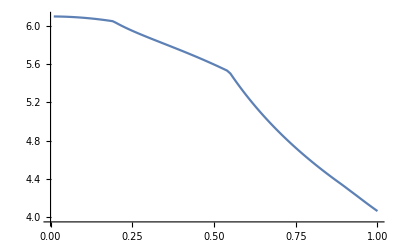

```mathematica
ListPlot[n0tab,Joined->True]
```

```mathematica
n0int=Interpolation[n0tab]
```

InterpolatingFunction[…]

```mathematica
n0int[0]
```

InterpolatingFunction::dmval: Input value {0} lies outside the range of data in the interpolating function. Extrapolation will be used.

6.099

InterpolatingFunction::dmval: Input value {0.0000204286} lies outside the range of data in the interpolating function. Extrapolation will be used.

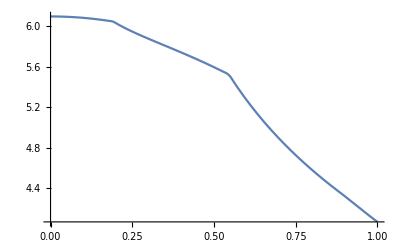

```mathematica
Plot[n0int[x],{x,0,1}]
```

```mathematica
(* comparisons *)
```

```mathematica
Hint[th_, δm2_, e_, η_] :=Module[{n=NchordInt[η],x=Last[xj[η]]+Δx[η]/rE},
rE/2*m{
{ V[n*(mol/cm^3)]-x k[δm2,e] Cos[2th],x k[δm2,e] Sin[2th]},
{x k[δm2,e] Sin[2th],x k[δm2,e] Cos[2th] - V[n*(mol/cm^3)]}
}/2];
```

```mathematica
U2[th_, δm2_, e_, η_]:=Module[{u=MatrixExp[-I Hint[th,δm2,e, η]]},u.uᵀ]
```

```mathematica
Pe[th_,δm2_,e_, η_]:= Module[{Uee = U2[th,δm2,e, η]}, Abs[Uee[[1,1]] Sin[th] + Uee[[1,2]] Cos[th]]^2]
```

```mathematica
PS[th_, δm2_,e_] := NIntegrate[Pveve[th,0,δm2,10^4 eV^2,e,density[r]]*B8radial[r]/B8int,{r,0,0.5}];
```

```mathematica
PSE[th_, δm2_,e_, η_] := Module[{ps = PS[th,δm2,e], pe = Pe[th,δm2,e,η]},
ps + (2ps-1)(Sin[th]^2-pe)/Cos[2th]]
```

```mathematica
P2eSolar[th_, δm2_,e_,η_]:=Module[{n=NchordInt[η]/(Last[xj[η]]+Δx[η]/rE),x=Last[xj[η]]+Δx[η]/rE},Sin[th]^2*(1+(4/((1+(V[n*(mol/cm^3)]/k[δm2,e]))^2-4*(V[n*(mol/cm^3)]/k[δm2,e])*Cos[th]^2)) *(V[n*(mol/cm^3)]/k[δm2,e])*Cos[th]^2*Sin[k[δm2,e]*((rE x m)/2)*√((1+(V[n*(mol/cm^3)]/k[δm2,e]))^2-4*(V[n*(mol/cm^3)]/k[δm2,e])*Cos[th]^2)]^2 )]
```

```mathematica
P2eSolar2[th_, δm2_,e_,n_,l_]:=Sin[th]^2*(1+(4/((1+(V[n*(mol/cm^3)]/k[δm2,e]))^2-4*(V[n*(mol/cm^3)]/k[δm2,e])*Cos[th]^2)) *(V[n*(mol/cm^3)]/k[δm2,e])*Cos[th]^2*Sin[k[δm2,e]*(l/2 m)*√((1+(V[n*(mol/cm^3)]/k[δm2,e]))^2-4*(V[n*(mol/cm^3)]/k[δm2,e])*Cos[th]^2)]^2 )
```

```mathematica
PSE2[th_, δm2_,e_, η_] := Module[{ps = PS[th,δm2,e], pe = P2eSolar[th,δm2,e,η]},
ps + (2ps-1)(Sin[th]^2-pe)/Cos[2th]]
```

```mathematica
PSE3[th12_,th13_, Δms21_,Δms31_,e_,n_,l_] := Module[{ps = PS[th12, Δms21,e],cos12Mbar = NIntegrate[Cos[2 th12M[th12,th13,Δms21,Δms31,e,density[r]]]*B8radial[r]/B8int,{r,0,0.5}]},ps - Cos[th13]^2 cos12Mbar*(P2eSolar2[th12,Δms21,e,n,l] - Sin[th12]^2)]
```

```mathematica
Plot[{Pe[ArcTan[√0.469], 7.9 10^-5 eV^2, e MeV, Pi/2],P2eSolar[ArcTan[√0.469], 7.9 10^-5 eV^2, e MeV,Pi/2]},{e,0,20}]
```

MatrixExp::eivn: Incorrect number 0 of eigenvectors for eigenvalue -1. √(-3.82004×10^8+8705.04 NchordInt[1.5708]-0.379549 NchordInt[1.5708]^2) with multiplicity 1.

Part::partw: Part 2 of MatrixExp[{{(0.-1.59275×10^6 ⅈ) (-0.00443567+3.868×10^-7 NchordInt[Times[«2»]]),0.-18223.4 ⅈ},{0.-18223.4 ⅈ,(0.-1.59275×10^6 ⅈ) (0.00443567-3.868×10^-7 NchordInt[Times[«2»]])}}] does not exist.

MatrixExp::eivn: Incorrect number 0 of eigenvectors for eigenvalue -1. √(-382.003+8.70503 NchordInt[1.5708]-0.379549 NchordInt[1.5708]^2) with multiplicity 1.

Part::partw: Part 2 of MatrixExp[{{(0.-1.59275×10^6 ⅈ) (-4.43566×10^-6+3.868×10^-7 NchordInt[Times[«2»]]),0.-18.2233 ⅈ},{0.-18.2233 ⅈ,(0.-1.59275×10^6 ⅈ) (4.43566×10^-6-3.868×10^-7 NchordInt[Times[«2»]])}}] does not exist.

MatrixExp::eivn: Incorrect number 0 of eigenvectors for eigenvalue -1. √(-95.5964+4.35469 NchordInt[1.5708]-0.379549 NchordInt[1.5708]^2) with multiplicity 1.

General::stop: Further output of MatrixExp::eivn will be suppressed during this calculation.

Part::partw: Part 2 of MatrixExp[{{(0.-1.59275×10^6 ⅈ) (-2.21894×10^-6+3.868×10^-7 NchordInt[Times[«2»]]),0.-9.11623 ⅈ},{0.-9.11623 ⅈ,(0.-1.59275×10^6 ⅈ) (2.21894×10^-6-3.868×10^-7 NchordInt[Times[«2»]])}}] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

-Graphics-

```mathematica
list=Table[{e,PSE2[ArcTan[√0.469],7.9 10^-5 eV^2, e MeV, Pi/2]},{e,0.1,20,0.05}];
list2=Table[{e,PSE2[ArcTan[√0.469],7.9 10^-5 eV^2, e MeV, Pi]},{e,0.1,20,0.05}];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {0.036125}. NIntegrate obtained 0.562579 and 1.37681×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {0.036125}. NIntegrate obtained 0.561184 and 1.37682×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {0.036125}. NIntegrate obtained 0.559777 and 1.37685×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {0.036125}. NIntegrate obtained 0.562579 and 1.37681×10^-6 for the integral and error estimates.

```mathematica
(* OK, now compare with numerical solution *)
```

```mathematica
ListPlot[{list,list2},Joined->True]
```

-Graphics-

```mathematica
H[r_,th_, δm2_, e_] := {
{V[Ne[r]*(mol/cm^3)] - k[δm2,e] Cos[2th], k[δm2,e] Sin[2th]},
{k[δm2,e] Sin[2th], k[δm2,e] Cos[2th] - V[Ne[r]*(mol/cm^3)]}
}/2;
```

```mathematica
N0int[0.5]
```

5.59659

```mathematica
U2[th_, δm2_, e_, n_,L_]:=Module[{u=MatrixExp[-I Hnu2[th,δm2,e, n]*L]},u]
```

```mathematica
Uconst[th13_,th12_,th23_,δ_,Δms21_,Δms3l_,E_, n_,L_]:=Module[{r13=R13[th13],r12=R12[th12],r23=R23[th23],d=Δ[δ],u=MatrixExp[-I Htilde[th13,th12,Δms21,Δms3l,E, n]*L]},
Chop[r23.d.u.d*.r23ᵀ]]
```

```mathematica
U[th13_,th12_,th23_,δ_,Δms21_,Δms3l_,E_, η_]:= Module[{r13=R13[th13],r12=R12[th12],r23=R23[th23],d=Δ[δ],n=NchordInt[η],x=Last[xj[η]]+Δx[η]/rE},
r23.d.MatrixExp[- I *rE*m(x*r13.r12.DiagonalMatrix[{0, k[Δms21,E],k[Δms3l,E]}].r12ᵀ.r13ᵀ + DiagonalMatrix[{V[n*mol/cm^3],0,0}])].d*.r23ᵀ
]
```

```mathematica
U2[th12,10^-5 eV^2,10 MeV,NchordInt[0] mol/cm^3, rE m]//MatrixForm
```

MatrixExp[(0.-6.371×10^6 ⅈ) Hnu2[0.662225,eV^2/100000,10 MeV,(mol NchordInt[0])/cm^3]]

```mathematica
Uconst[th13,th12,th23,d,10^-5 eV^2, 10^-3 eV^2,10 MeV, NchordInt[0] mol/cm^3, rE m]//MatrixForm
```

((0.202897+0. ⅈ) RootSum[(0.-16035.3 ⅈ) NchordInt[0]-(10568.+0. ⅈ) #1-(1607.79+0. ⅈ) NchordInt[0] #1+(0.+661.409 ⅈ) #1^2+(0.+1. ⅈ) NchordInt[0] #1^2+(0.405794+0. ⅈ) #1^3&,((0.+16035.3 ⅈ) ⅇ^#1+(1607.79+0. ⅈ) ⅇ^#1 #1-(0.+1. ⅈ) ⅇ^#1 #1^2)/((0.+5283.98 ⅈ)+(0.+803.894 ⅈ) NchordInt[0]+(661.409+0. ⅈ) #1+(1.+0. ⅈ) NchordInt[0] #1-(0.+0.608691 ⅈ) #1^2)&] | (10.3982+38.8065 ⅈ) RootSum[(0.-16035.3 ⅈ) NchordInt[0]-(10568.+0. ⅈ) #1-(1607.79+0. ⅈ) NchordInt[0] #1+(0.+661.409 ⅈ) #1^2+(0.+1. ⅈ) NchordInt[0] #1^2+(0.405794+0. ⅈ) #1^3&,((0.+10.0747 ⅈ) ⅇ^#1+1. ⅇ^#1 #1)/(-8680.89-1320.69 NchordInt[0]+(0.+1086.61 ⅈ) #1+(0.+1.64287 ⅈ) NchordInt[0] #1+1. #1^2)&]-(0.+1.70273 ⅈ) RootSum[(0.-16035.3 ⅈ) NchordInt[0]-(10568.+0. ⅈ) #1-(1607.79+0. ⅈ) NchordInt[0] #1+(0.+661.409 ⅈ) #1^2+(0.+1. ⅈ) NchordInt[0] #1^2+(0.405794+0. ⅈ) #1^3&,((0.+1613.77 ⅈ) ⅇ^#1+1. ⅇ^#1 #1)/(-8680.89-1320.69 NchordInt[0]+(0.+1086.61 ⅈ) #1+(0.+1.64287 ⅈ) NchordInt[0] #1+1. #1^2)&] | (9.03899+33.734 ⅈ) RootSum[(0.-16035.3 ⅈ) NchordInt[0]-(10568.+0. ⅈ) #1-(1607.79+0. ⅈ) NchordInt[0] #1+(0.+661.409 ⅈ) #1^2+(0.+1. ⅈ) NchordInt[0] #1^2+(0.405794+0. ⅈ) #1^3&,((0.+10.0747 ⅈ) ⅇ^#1+1. ⅇ^#1 #1)/(-8680.89-1320.69 NchordInt[0]+(0.+1086.61 ⅈ) #1+(0.+1.64287 ⅈ) NchordInt[0] #1+1. #1^2)&]+(0.+1.95877 ⅈ) RootSum[(0.-16035.3 ⅈ) NchordInt[0]-(10568.+0. ⅈ) #1-(1607.79+0. ⅈ) NchordInt[0] #1+(0.+661.409 ⅈ) #1^2+(0.+1. ⅈ) NchordInt[0] #1^2+(0.405794+0. ⅈ) #1^3&,((0.+1613.77 ⅈ) ⅇ^#1+1. ⅇ^#1 #1)/(-8680.89-1320.69 NchordInt[0]+(0.+1086.61 ⅈ) #1+(0.+1.64287 ⅈ) NchordInt[0] #1+1. #1^2)&]
(-10.3982+38.8065 ⅈ) RootSum[(0.-16035.3 ⅈ) NchordInt[0]-(10568.+0. ⅈ) #1-(1607.79+0. ⅈ) NchordInt[0] #1+(0.+661.409 ⅈ) #1^2+(0.+1. ⅈ) NchordInt[0] #1^2+(0.405794+0. ⅈ) #1^3&,((0.+10.0747 ⅈ) ⅇ^#1+1. ⅇ^#1 #1)/(-8680.89-1320.69 NchordInt[0]+(0.+1086.61 ⅈ) #1+(0.+1.64287 ⅈ) NchordInt[0] #1+1. #1^2)&]-(0.+1.70273 ⅈ) RootSum[(0.-16035.3 ⅈ) NchordInt[0]-(10568.+0. ⅈ) #1-(1607.79+0. ⅈ) NchordInt[0] #1+(0.+661.409 ⅈ) #1^2+(0.+1. ⅈ) NchordInt[0] #1^2+(0.405794+0. ⅈ) #1^3&,((0.+1613.77 ⅈ) ⅇ^#1+1. ⅇ^#1 #1)/(-8680.89-1320.69 NchordInt[0]+(0.+1086.61 ⅈ) #1+(0.+1.64287 ⅈ) NchordInt[0] #1+1. #1^2)&] | ⅇ^(-195 ⅈ °) Cos[41 °] ((0.+0.170844 ⅈ) RootSum[(0.-16035.3 ⅈ) NchordInt[0]-(10568.+0. ⅈ) #1-(1607.79+0. ⅈ) NchordInt[0] #1+(0.+661.409 ⅈ) #1^2+(0.+1. ⅈ) NchordInt[0] #1^2+(0.405794+0. ⅈ) #1^3&,((0.+1613.77 ⅈ) ⅇ^#1+(0.+2.4643 ⅈ) ⅇ^#1 NchordInt[0]+1. ⅇ^#1 #1)/(-8680.89-1320.69 NchordInt[0]+(0.+1086.61 ⅈ) #1+(0.+1.64287 ⅈ) NchordInt[0] #1+1. #1^2)&]-(0.364497+0.0976666 ⅈ) RootSum[(0.-16035.3 ⅈ) NchordInt[0]-(10568.+0. ⅈ) #1-(1607.79+0. ⅈ) NchordInt[0] #1+(0.+661.409 ⅈ) #1^2+(0.+1. ⅈ) NchordInt[0] #1^2+(0.405794+0. ⅈ) #1^3&,((0.+65.5078 ⅈ) ⅇ^#1+(0.+10.0366 ⅈ) ⅇ^#1 NchordInt[0]+(13.0508+0. ⅈ) ⅇ^#1 #1+(1.+0. ⅈ) ⅇ^#1 NchordInt[0] #1-(0.+0.405794 ⅈ) ⅇ^#1 #1^2)/((0.+5283.98 ⅈ)+(0.+803.894 ⅈ) NchordInt[0]+(661.409+0. ⅈ) #1+(1.+0. ⅈ) NchordInt[0] #1-(0.+0.608691 ⅈ) #1^2)&])+((0.0508667-0.189837 ⅈ) RootSum[(0.-16035.3 ⅈ) NchordInt[0]-(10568.+0. ⅈ) #1-(1607.79+0. ⅈ) NchordInt[0] #1+(0.+661.409 ⅈ) #1^2+(0.+1. ⅈ) NchordInt[0] #1^2+(0.405794+0. ⅈ) #1^3&,((0.+1613.77 ⅈ) ⅇ^#1+(0.+2.4643 ⅈ) ⅇ^#1 NchordInt[0]+1. ⅇ^#1 #1)/(-8680.89-1320.69 NchordInt[0]+(0.+1086.61 ⅈ) #1+(0.+1.64287 ⅈ) NchordInt[0] #1+1. #1^2)&]+(0.32803+0. ⅈ) RootSum[(0.-16035.3 ⅈ) NchordInt[0]-(10568.+0. ⅈ) #1-(1607.79+0. ⅈ) NchordInt[0] #1+(0.+661.409 ⅈ) #1^2+(0.+1. ⅈ) NchordInt[0] #1^2+(0.405794+0. ⅈ) #1^3&,((0.+3995.42 ⅈ) ⅇ^#1+(0.+1597.75 ⅈ) ⅇ^#1 NchordInt[0]+(657.336+0. ⅈ) ⅇ^#1 #1+(1.+0. ⅈ) ⅇ^#1 NchordInt[0] #1-(0.+0.405794 ⅈ) ⅇ^#1 #1^2)/((0.+5283.98 ⅈ)+(0.+803.894 ⅈ) NchordInt[0]+(661.409+0. ⅈ) #1+(1.+0. ⅈ) NchordInt[0] #1-(0.+0.608691 ⅈ) #1^2)&]) Sin[41 °] | -Cos[41 °] ((0.0508667-0.189837 ⅈ) RootSum[(0.-16035.3 ⅈ) NchordInt[0]-(10568.+0. ⅈ) #1-(1607.79+0. ⅈ) NchordInt[0] #1+(0.+661.409 ⅈ) #1^2+(0.+1. ⅈ) NchordInt[0] #1^2+(0.405794+0. ⅈ) #1^3&,((0.+1613.77 ⅈ) ⅇ^#1+(0.+2.4643 ⅈ) ⅇ^#1 NchordInt[0]+1. ⅇ^#1 #1)/(-8680.89-1320.69 NchordInt[0]+(0.+1086.61 ⅈ) #1+(0.+1.64287 ⅈ) NchordInt[0] #1+1. #1^2)&]+(0.32803+0. ⅈ) RootSum[(0.-16035.3 ⅈ) NchordInt[0]-(10568.+0. ⅈ) #1-(1607.79+0. ⅈ) NchordInt[0] #1+(0.+661.409 ⅈ) #1^2+(0.+1. ⅈ) NchordInt[0] #1^2+(0.405794+0. ⅈ) #1^3&,((0.+3995.42 ⅈ) ⅇ^#1+(0.+1597.75 ⅈ) ⅇ^#1 NchordInt[0]+(657.336+0. ⅈ) ⅇ^#1 #1+(1.+0. ⅈ) ⅇ^#1 NchordInt[0] #1-(0.+0.405794 ⅈ) ⅇ^#1 #1^2)/((0.+5283.98 ⅈ)+(0.+803.894 ⅈ) NchordInt[0]+(661.409+0. ⅈ) #1+(1.+0. ⅈ) NchordInt[0] #1-(0.+0.608691 ⅈ) #1^2)&])+ⅇ^(-195 ⅈ °) ((0.+0.170844 ⅈ) RootSum[(0.-16035.3 ⅈ) NchordInt[0]-(10568.+0. ⅈ) #1-(1607.79+0. ⅈ) NchordInt[0] #1+(0.+661.409 ⅈ) #1^2+(0.+1. ⅈ) NchordInt[0] #1^2+(0.405794+0. ⅈ) #1^3&,((0.+1613.77 ⅈ) ⅇ^#1+(0.+2.4643 ⅈ) ⅇ^#1 NchordInt[0]+1. ⅇ^#1 #1)/(-8680.89-1320.69 NchordInt[0]+(0.+1086.61 ⅈ) #1+(0.+1.64287 ⅈ) NchordInt[0] #1+1. #1^2)&]-(0.364497+0.0976666 ⅈ) RootSum[(0.-16035.3 ⅈ) NchordInt[0]-(10568.+0. ⅈ) #1-(1607.79+0. ⅈ) NchordInt[0] #1+(0.+661.409 ⅈ) #1^2+(0.+1. ⅈ) NchordInt[0] #1^2+(0.405794+0. ⅈ) #1^3&,((0.+65.5078 ⅈ) ⅇ^#1+(0.+10.0366 ⅈ) ⅇ^#1 NchordInt[0]+(13.0508+0. ⅈ) ⅇ^#1 #1+(1.+0. ⅈ) ⅇ^#1 NchordInt[0] #1-(0.+0.405794 ⅈ) ⅇ^#1 #1^2)/((0.+5283.98 ⅈ)+(0.+803.894 ⅈ) NchordInt[0]+(661.409+0. ⅈ) #1+(1.+0. ⅈ) NchordInt[0] #1-(0.+0.608691 ⅈ) #1^2)&]) Sin[41 °]
(-9.03899+33.734 ⅈ) RootSum[(0.-16035.3 ⅈ) NchordInt[0]-(10568.+0. ⅈ) #1-(1607.79+0. ⅈ) NchordInt[0] #1+(0.+661.409 ⅈ) #1^2+(0.+1. ⅈ) NchordInt[0] #1^2+(0.405794+0. ⅈ) #1^3&,((0.+10.0747 ⅈ) ⅇ^#1+1. ⅇ^#1 #1)/(-8680.89-1320.69 NchordInt[0]+(0.+1086.61 ⅈ) #1+(0.+1.64287 ⅈ) NchordInt[0] #1+1. #1^2)&]+(0.+1.95877 ⅈ) RootSum[(0.-16035.3 ⅈ) NchordInt[0]-(10568.+0. ⅈ) #1-(1607.79+0. ⅈ) NchordInt[0] #1+(0.+661.409 ⅈ) #1^2+(0.+1. ⅈ) NchordInt[0] #1^2+(0.405794+0. ⅈ) #1^3&,((0.+1613.77 ⅈ) ⅇ^#1+1. ⅇ^#1 #1)/(-8680.89-1320.69 NchordInt[0]+(0.+1086.61 ⅈ) #1+(0.+1.64287 ⅈ) NchordInt[0] #1+1. #1^2)&] | ⅇ^(-195 ⅈ °) Cos[41 °] ((0.-0.196534 ⅈ) RootSum[(0.-16035.3 ⅈ) NchordInt[0]-(10568.+0. ⅈ) #1-(1607.79+0. ⅈ) NchordInt[0] #1+(0.+661.409 ⅈ) #1^2+(0.+1. ⅈ) NchordInt[0] #1^2+(0.405794+0. ⅈ) #1^3&,((0.+1613.77 ⅈ) ⅇ^#1+(0.+2.4643 ⅈ) ⅇ^#1 NchordInt[0]+1. ⅇ^#1 #1)/(-8680.89-1320.69 NchordInt[0]+(0.+1086.61 ⅈ) #1+(0.+1.64287 ⅈ) NchordInt[0] #1+1. #1^2)&]-(0.316852+0.0849003 ⅈ) RootSum[(0.-16035.3 ⅈ) NchordInt[0]-(10568.+0. ⅈ) #1-(1607.79+0. ⅈ) NchordInt[0] #1+(0.+661.409 ⅈ) #1^2+(0.+1. ⅈ) NchordInt[0] #1^2+(0.405794+0. ⅈ) #1^3&,((0.+65.5078 ⅈ) ⅇ^#1+(0.+10.0366 ⅈ) ⅇ^#1 NchordInt[0]+(13.0508+0. ⅈ) ⅇ^#1 #1+(1.+0. ⅈ) ⅇ^#1 NchordInt[0] #1-(0.+0.405794 ⅈ) ⅇ^#1 #1^2)/((0.+5283.98 ⅈ)+(0.+803.894 ⅈ) NchordInt[0]+(661.409+0. ⅈ) #1+(1.+0. ⅈ) NchordInt[0] #1-(0.+0.608691 ⅈ) #1^2)&])+((0.0442178-0.165023 ⅈ) RootSum[(0.-16035.3 ⅈ) NchordInt[0]-(10568.+0. ⅈ) #1-(1607.79+0. ⅈ) NchordInt[0] #1+(0.+661.409 ⅈ) #1^2+(0.+1. ⅈ) NchordInt[0] #1^2+(0.405794+0. ⅈ) #1^3&,((0.+1613.77 ⅈ) ⅇ^#1+(0.+2.4643 ⅈ) ⅇ^#1 NchordInt[0]+1. ⅇ^#1 #1)/(-8680.89-1320.69 NchordInt[0]+(0.+1086.61 ⅈ) #1+(0.+1.64287 ⅈ) NchordInt[0] #1+1. #1^2)&]-(0.377355+0. ⅈ) RootSum[(0.-16035.3 ⅈ) NchordInt[0]-(10568.+0. ⅈ) #1-(1607.79+0. ⅈ) NchordInt[0] #1+(0.+661.409 ⅈ) #1^2+(0.+1. ⅈ) NchordInt[0] #1^2+(0.405794+0. ⅈ) #1^3&,((0.+3995.42 ⅈ) ⅇ^#1+(0.+1597.75 ⅈ) ⅇ^#1 NchordInt[0]+(657.336+0. ⅈ) ⅇ^#1 #1+(1.+0. ⅈ) ⅇ^#1 NchordInt[0] #1-(0.+0.405794 ⅈ) ⅇ^#1 #1^2)/((0.+5283.98 ⅈ)+(0.+803.894 ⅈ) NchordInt[0]+(661.409+0. ⅈ) #1+(1.+0. ⅈ) NchordInt[0] #1-(0.+0.608691 ⅈ) #1^2)&]) Sin[41 °] | -Cos[41 °] ((0.0442178-0.165023 ⅈ) RootSum[(0.-16035.3 ⅈ) NchordInt[0]-(10568.+0. ⅈ) #1-(1607.79+0. ⅈ) NchordInt[0] #1+(0.+661.409 ⅈ) #1^2+(0.+1. ⅈ) NchordInt[0] #1^2+(0.405794+0. ⅈ) #1^3&,((0.+1613.77 ⅈ) ⅇ^#1+(0.+2.4643 ⅈ) ⅇ^#1 NchordInt[0]+1. ⅇ^#1 #1)/(-8680.89-1320.69 NchordInt[0]+(0.+1086.61 ⅈ) #1+(0.+1.64287 ⅈ) NchordInt[0] #1+1. #1^2)&]-(0.377355+0. ⅈ) RootSum[(0.-16035.3 ⅈ) NchordInt[0]-(10568.+0. ⅈ) #1-(1607.79+0. ⅈ) NchordInt[0] #1+(0.+661.409 ⅈ) #1^2+(0.+1. ⅈ) NchordInt[0] #1^2+(0.405794+0. ⅈ) #1^3&,((0.+3995.42 ⅈ) ⅇ^#1+(0.+1597.75 ⅈ) ⅇ^#1 NchordInt[0]+(657.336+0. ⅈ) ⅇ^#1 #1+(1.+0. ⅈ) ⅇ^#1 NchordInt[0] #1-(0.+0.405794 ⅈ) ⅇ^#1 #1^2)/((0.+5283.98 ⅈ)+(0.+803.894 ⅈ) NchordInt[0]+(661.409+0. ⅈ) #1+(1.+0. ⅈ) NchordInt[0] #1-(0.+0.608691 ⅈ) #1^2)&])+ⅇ^(-195 ⅈ °) ((0.-0.196534 ⅈ) RootSum[(0.-16035.3 ⅈ) NchordInt[0]-(10568.+0. ⅈ) #1-(1607.79+0. ⅈ) NchordInt[0] #1+(0.+661.409 ⅈ) #1^2+(0.+1. ⅈ) NchordInt[0] #1^2+(0.405794+0. ⅈ) #1^3&,((0.+1613.77 ⅈ) ⅇ^#1+(0.+2.4643 ⅈ) ⅇ^#1 NchordInt[0]+1. ⅇ^#1 #1)/(-8680.89-1320.69 NchordInt[0]+(0.+1086.61 ⅈ) #1+(0.+1.64287 ⅈ) NchordInt[0] #1+1. #1^2)&]-(0.316852+0.0849003 ⅈ) RootSum[(0.-16035.3 ⅈ) NchordInt[0]-(10568.+0. ⅈ) #1-(1607.79+0. ⅈ) NchordInt[0] #1+(0.+661.409 ⅈ) #1^2+(0.+1. ⅈ) NchordInt[0] #1^2+(0.405794+0. ⅈ) #1^3&,((0.+65.5078 ⅈ) ⅇ^#1+(0.+10.0366 ⅈ) ⅇ^#1 NchordInt[0]+(13.0508+0. ⅈ) ⅇ^#1 #1+(1.+0. ⅈ) ⅇ^#1 NchordInt[0] #1-(0.+0.405794 ⅈ) ⅇ^#1 #1^2)/((0.+5283.98 ⅈ)+(0.+803.894 ⅈ) NchordInt[0]+(661.409+0. ⅈ) #1+(1.+0. ⅈ) NchordInt[0] #1-(0.+0.608691 ⅈ) #1^2)&]) Sin[41 °])

```mathematica
U[th13,th12,th23,d,10^-5 eV^2, 10^-3 eV^2,10 MeV,0]//MatrixForm
```

((0.+0. ⅈ)+0.333333 RootSum[(0.+1.18102×10^-11 ⅈ)-(0.+16045.4 ⅈ) NchordInt[0]-(10574.6+0. ⅈ) #1-(1608.29+0. ⅈ) NchordInt[0] #1+(0.+661.617 ⅈ) #1^2+(0.+1. ⅈ) NchordInt[0] #1^2+(0.405794+0. ⅈ) #1^3&,((-16045.4+0. ⅈ) ⅇ^#1+(0.+1608.29 ⅈ) ⅇ^#1 #1+ⅇ^#1 #1^2)/(-8686.34-1321.11 NchordInt[0]+(0.+1086.95 ⅈ) #1+(0.+1.64287 ⅈ) NchordInt[0] #1+1. #1^2)&] | ⅇ^(-195 ⅈ °) Cos[41 °] ((0.+0. ⅈ)-(0.+53.2497 ⅈ) RootSum[(0.+1.18102×10^-11 ⅈ)-(0.+16045.4 ⅈ) NchordInt[0]-(10574.6+0. ⅈ) #1-(1608.29+0. ⅈ) NchordInt[0] #1+(0.+661.617 ⅈ) #1^2+(0.+1. ⅈ) NchordInt[0] #1^2+(0.405794+0. ⅈ) #1^3&,((0.+10.0778 ⅈ) ⅇ^#1+(1.+0. ⅈ) ⅇ^#1 #1)/(-8686.34-1321.11 NchordInt[0]+(0.+1086.95 ⅈ) #1+(0.+1.64287 ⅈ) NchordInt[0] #1+1. #1^2)&])+((0.+0. ⅈ)-(0.+2.59621 ⅈ) RootSum[(0.+1.18102×10^-11 ⅈ)-(0.+16045.4 ⅈ) NchordInt[0]-(10574.6+0. ⅈ) #1-(1608.29+0. ⅈ) NchordInt[0] #1+(0.+661.617 ⅈ) #1^2+(0.+1. ⅈ) NchordInt[0] #1^2+(0.405794+0. ⅈ) #1^3&,((0.+1614.28 ⅈ) ⅇ^#1+(1.+0. ⅈ) ⅇ^#1 #1)/(-8686.34-1321.11 NchordInt[0]+(0.+1086.95 ⅈ) #1+(0.+1.64287 ⅈ) NchordInt[0] #1+1. #1^2)&]) Sin[41 °] | -Cos[41 °] ((0.+0. ⅈ)-(0.+2.59621 ⅈ) RootSum[(0.+1.18102×10^-11 ⅈ)-(0.+16045.4 ⅈ) NchordInt[0]-(10574.6+0. ⅈ) #1-(1608.29+0. ⅈ) NchordInt[0] #1+(0.+661.617 ⅈ) #1^2+(0.+1. ⅈ) NchordInt[0] #1^2+(0.405794+0. ⅈ) #1^3&,((0.+1614.28 ⅈ) ⅇ^#1+(1.+0. ⅈ) ⅇ^#1 #1)/(-8686.34-1321.11 NchordInt[0]+(0.+1086.95 ⅈ) #1+(0.+1.64287 ⅈ) NchordInt[0] #1+1. #1^2)&])+ⅇ^(-195 ⅈ °) ((0.+0. ⅈ)-(0.+53.2497 ⅈ) RootSum[(0.+1.18102×10^-11 ⅈ)-(0.+16045.4 ⅈ) NchordInt[0]-(10574.6+0. ⅈ) #1-(1608.29+0. ⅈ) NchordInt[0] #1+(0.+661.617 ⅈ) #1^2+(0.+1. ⅈ) NchordInt[0] #1^2+(0.405794+0. ⅈ) #1^3&,((0.+10.0778 ⅈ) ⅇ^#1+(1.+0. ⅈ) ⅇ^#1 #1)/(-8686.34-1321.11 NchordInt[0]+(0.+1086.95 ⅈ) #1+(0.+1.64287 ⅈ) NchordInt[0] #1+1. #1^2)&]) Sin[41 °]
0.-(10.4014-38.8187 ⅈ) RootSum[(0.+1.18102×10^-11 ⅈ)-(0.+16045.4 ⅈ) NchordInt[0]-(10574.6+0. ⅈ) #1-(1608.29+0. ⅈ) NchordInt[0] #1+(0.+661.617 ⅈ) #1^2+(0.+1. ⅈ) NchordInt[0] #1^2+(0.405794+0. ⅈ) #1^3&,((0.+10.0778 ⅈ) ⅇ^#1+(1.+0. ⅈ) ⅇ^#1 #1)/(-8686.34-1321.11 NchordInt[0]+(0.+1086.95 ⅈ) #1+(0.+1.64287 ⅈ) NchordInt[0] #1+1. #1^2)&]-(0.+1.70326 ⅈ) RootSum[(0.+1.18102×10^-11 ⅈ)-(0.+16045.4 ⅈ) NchordInt[0]-(10574.6+0. ⅈ) #1-(1608.29+0. ⅈ) NchordInt[0] #1+(0.+661.617 ⅈ) #1^2+(0.+1. ⅈ) NchordInt[0] #1^2+(0.405794+0. ⅈ) #1^3&,((0.+1614.28 ⅈ) ⅇ^#1+(1.+0. ⅈ) ⅇ^#1 #1)/(-8686.34-1321.11 NchordInt[0]+(0.+1086.95 ⅈ) #1+(0.+1.64287 ⅈ) NchordInt[0] #1+1. #1^2)&] | ⅇ^(-195 ⅈ °) Cos[41 °] ((0.+0. ⅈ)+(0.+0.170898 ⅈ) RootSum[(0.+1.18102×10^-11 ⅈ)-(0.+16045.4 ⅈ) NchordInt[0]-(10574.6+0. ⅈ) #1-(1608.29+0. ⅈ) NchordInt[0] #1+(0.+661.617 ⅈ) #1^2+(0.+1. ⅈ) NchordInt[0] #1^2+(0.405794+0. ⅈ) #1^3&,((0.+1614.28 ⅈ) ⅇ^#1+(0.+2.4643 ⅈ) ⅇ^#1 NchordInt[0]+(1.+0. ⅈ) ⅇ^#1 #1)/(-8686.34-1321.11 NchordInt[0]+(0.+1086.95 ⅈ) #1+(0.+1.64287 ⅈ) NchordInt[0] #1+1. #1^2)&]-(0.242998+0.0651111 ⅈ) RootSum[(0.+1.18102×10^-11 ⅈ)-(0.+16045.4 ⅈ) NchordInt[0]-(10574.6+0. ⅈ) #1-(1608.29+0. ⅈ) NchordInt[0] #1+(0.+661.617 ⅈ) #1^2+(0.+1. ⅈ) NchordInt[0] #1^2+(0.405794+0. ⅈ) #1^3&,((-161.532+0. ⅈ) ⅇ^#1-(24.7409+0. ⅈ) ⅇ^#1 NchordInt[0]+(0.+32.1713 ⅈ) ⅇ^#1 #1+(0.+2.4643 ⅈ) ⅇ^#1 NchordInt[0] #1+ⅇ^#1 #1^2)/(-8686.34-1321.11 NchordInt[0]+(0.+1086.95 ⅈ) #1+(0.+1.64287 ⅈ) NchordInt[0] #1+1. #1^2)&])+((0.+0. ⅈ)+(0.0508827-0.189897 ⅈ) RootSum[(0.+1.18102×10^-11 ⅈ)-(0.+16045.4 ⅈ) NchordInt[0]-(10574.6+0. ⅈ) #1-(1608.29+0. ⅈ) NchordInt[0] #1+(0.+661.617 ⅈ) #1^2+(0.+1. ⅈ) NchordInt[0] #1^2+(0.405794+0. ⅈ) #1^3&,((0.+1614.28 ⅈ) ⅇ^#1+(0.+2.4643 ⅈ) ⅇ^#1 NchordInt[0]+(1.+0. ⅈ) ⅇ^#1 #1)/(-8686.34-1321.11 NchordInt[0]+(0.+1086.95 ⅈ) #1+(0.+1.64287 ⅈ) NchordInt[0] #1+1. #1^2)&]+0.218686 RootSum[(0.+1.18102×10^-11 ⅈ)-(0.+16045.4 ⅈ) NchordInt[0]-(10574.6+0. ⅈ) #1-(1608.29+0. ⅈ) NchordInt[0] #1+(0.+661.617 ⅈ) #1^2+(0.+1. ⅈ) NchordInt[0] #1^2+(0.405794+0. ⅈ) #1^3&,((-9852.1+0. ⅈ) ⅇ^#1-(3938.58+0. ⅈ) ⅇ^#1 NchordInt[0]+(0.+1620.38 ⅈ) ⅇ^#1 #1+(0.+2.4643 ⅈ) ⅇ^#1 NchordInt[0] #1+ⅇ^#1 #1^2)/(-8686.34-1321.11 NchordInt[0]+(0.+1086.95 ⅈ) #1+(0.+1.64287 ⅈ) NchordInt[0] #1+1. #1^2)&]) Sin[41 °] | -Cos[41 °] ((0.+0. ⅈ)+(0.0508827-0.189897 ⅈ) RootSum[(0.+1.18102×10^-11 ⅈ)-(0.+16045.4 ⅈ) NchordInt[0]-(10574.6+0. ⅈ) #1-(1608.29+0. ⅈ) NchordInt[0] #1+(0.+661.617 ⅈ) #1^2+(0.+1. ⅈ) NchordInt[0] #1^2+(0.405794+0. ⅈ) #1^3&,((0.+1614.28 ⅈ) ⅇ^#1+(0.+2.4643 ⅈ) ⅇ^#1 NchordInt[0]+(1.+0. ⅈ) ⅇ^#1 #1)/(-8686.34-1321.11 NchordInt[0]+(0.+1086.95 ⅈ) #1+(0.+1.64287 ⅈ) NchordInt[0] #1+1. #1^2)&]+0.218686 RootSum[(0.+1.18102×10^-11 ⅈ)-(0.+16045.4 ⅈ) NchordInt[0]-(10574.6+0. ⅈ) #1-(1608.29+0. ⅈ) NchordInt[0] #1+(0.+661.617 ⅈ) #1^2+(0.+1. ⅈ) NchordInt[0] #1^2+(0.405794+0. ⅈ) #1^3&,((-9852.1+0. ⅈ) ⅇ^#1-(3938.58+0. ⅈ) ⅇ^#1 NchordInt[0]+(0.+1620.38 ⅈ) ⅇ^#1 #1+(0.+2.4643 ⅈ) ⅇ^#1 NchordInt[0] #1+ⅇ^#1 #1^2)/(-8686.34-1321.11 NchordInt[0]+(0.+1086.95 ⅈ) #1+(0.+1.64287 ⅈ) NchordInt[0] #1+1. #1^2)&])+ⅇ^(-195 ⅈ °) ((0.+0. ⅈ)+(0.+0.170898 ⅈ) RootSum[(0.+1.18102×10^-11 ⅈ)-(0.+16045.4 ⅈ) NchordInt[0]-(10574.6+0. ⅈ) #1-(1608.29+0. ⅈ) NchordInt[0] #1+(0.+661.617 ⅈ) #1^2+(0.+1. ⅈ) NchordInt[0] #1^2+(0.405794+0. ⅈ) #1^3&,((0.+1614.28 ⅈ) ⅇ^#1+(0.+2.4643 ⅈ) ⅇ^#1 NchordInt[0]+(1.+0. ⅈ) ⅇ^#1 #1)/(-8686.34-1321.11 NchordInt[0]+(0.+1086.95 ⅈ) #1+(0.+1.64287 ⅈ) NchordInt[0] #1+1. #1^2)&]-(0.242998+0.0651111 ⅈ) RootSum[(0.+1.18102×10^-11 ⅈ)-(0.+16045.4 ⅈ) NchordInt[0]-(10574.6+0. ⅈ) #1-(1608.29+0. ⅈ) NchordInt[0] #1+(0.+661.617 ⅈ) #1^2+(0.+1. ⅈ) NchordInt[0] #1^2+(0.405794+0. ⅈ) #1^3&,((-161.532+0. ⅈ) ⅇ^#1-(24.7409+0. ⅈ) ⅇ^#1 NchordInt[0]+(0.+32.1713 ⅈ) ⅇ^#1 #1+(0.+2.4643 ⅈ) ⅇ^#1 NchordInt[0] #1+ⅇ^#1 #1^2)/(-8686.34-1321.11 NchordInt[0]+(0.+1086.95 ⅈ) #1+(0.+1.64287 ⅈ) NchordInt[0] #1+1. #1^2)&]) Sin[41 °]
0.-(9.04183-33.7446 ⅈ) RootSum[(0.+1.18102×10^-11 ⅈ)-(0.+16045.4 ⅈ) NchordInt[0]-(10574.6+0. ⅈ) #1-(1608.29+0. ⅈ) NchordInt[0] #1+(0.+661.617 ⅈ) #1^2+(0.+1. ⅈ) NchordInt[0] #1^2+(0.405794+0. ⅈ) #1^3&,((0.+10.0778 ⅈ) ⅇ^#1+(1.+0. ⅈ) ⅇ^#1 #1)/(-8686.34-1321.11 NchordInt[0]+(0.+1086.95 ⅈ) #1+(0.+1.64287 ⅈ) NchordInt[0] #1+1. #1^2)&]+(0.+1.95938 ⅈ) RootSum[(0.+1.18102×10^-11 ⅈ)-(0.+16045.4 ⅈ) NchordInt[0]-(10574.6+0. ⅈ) #1-(1608.29+0. ⅈ) NchordInt[0] #1+(0.+661.617 ⅈ) #1^2+(0.+1. ⅈ) NchordInt[0] #1^2+(0.405794+0. ⅈ) #1^3&,((0.+1614.28 ⅈ) ⅇ^#1+(1.+0. ⅈ) ⅇ^#1 #1)/(-8686.34-1321.11 NchordInt[0]+(0.+1086.95 ⅈ) #1+(0.+1.64287 ⅈ) NchordInt[0] #1+1. #1^2)&] | ⅇ^(-195 ⅈ °) Cos[41 °] ((0.+0. ⅈ)-(0.+0.196596 ⅈ) RootSum[(0.+1.18102×10^-11 ⅈ)-(0.+16045.4 ⅈ) NchordInt[0]-(10574.6+0. ⅈ) #1-(1608.29+0. ⅈ) NchordInt[0] #1+(0.+661.617 ⅈ) #1^2+(0.+1. ⅈ) NchordInt[0] #1^2+(0.405794+0. ⅈ) #1^3&,((0.+1614.28 ⅈ) ⅇ^#1+(0.+2.4643 ⅈ) ⅇ^#1 NchordInt[0]+(1.+0. ⅈ) ⅇ^#1 #1)/(-8686.34-1321.11 NchordInt[0]+(0.+1086.95 ⅈ) #1+(0.+1.64287 ⅈ) NchordInt[0] #1+1. #1^2)&]-(0.211235+0.0566002 ⅈ) RootSum[(0.+1.18102×10^-11 ⅈ)-(0.+16045.4 ⅈ) NchordInt[0]-(10574.6+0. ⅈ) #1-(1608.29+0. ⅈ) NchordInt[0] #1+(0.+661.617 ⅈ) #1^2+(0.+1. ⅈ) NchordInt[0] #1^2+(0.405794+0. ⅈ) #1^3&,((-161.532+0. ⅈ) ⅇ^#1-(24.7409+0. ⅈ) ⅇ^#1 NchordInt[0]+(0.+32.1713 ⅈ) ⅇ^#1 #1+(0.+2.4643 ⅈ) ⅇ^#1 NchordInt[0] #1+ⅇ^#1 #1^2)/(-8686.34-1321.11 NchordInt[0]+(0.+1086.95 ⅈ) #1+(0.+1.64287 ⅈ) NchordInt[0] #1+1. #1^2)&])+((0.+0. ⅈ)+(0.0442316-0.165075 ⅈ) RootSum[(0.+1.18102×10^-11 ⅈ)-(0.+16045.4 ⅈ) NchordInt[0]-(10574.6+0. ⅈ) #1-(1608.29+0. ⅈ) NchordInt[0] #1+(0.+661.617 ⅈ) #1^2+(0.+1. ⅈ) NchordInt[0] #1^2+(0.405794+0. ⅈ) #1^3&,((0.+1614.28 ⅈ) ⅇ^#1+(0.+2.4643 ⅈ) ⅇ^#1 NchordInt[0]+(1.+0. ⅈ) ⅇ^#1 #1)/(-8686.34-1321.11 NchordInt[0]+(0.+1086.95 ⅈ) #1+(0.+1.64287 ⅈ) NchordInt[0] #1+1. #1^2)&]-0.25157 RootSum[(0.+1.18102×10^-11 ⅈ)-(0.+16045.4 ⅈ) NchordInt[0]-(10574.6+0. ⅈ) #1-(1608.29+0. ⅈ) NchordInt[0] #1+(0.+661.617 ⅈ) #1^2+(0.+1. ⅈ) NchordInt[0] #1^2+(0.405794+0. ⅈ) #1^3&,((-9852.1+0. ⅈ) ⅇ^#1-(3938.58+0. ⅈ) ⅇ^#1 NchordInt[0]+(0.+1620.38 ⅈ) ⅇ^#1 #1+(0.+2.4643 ⅈ) ⅇ^#1 NchordInt[0] #1+ⅇ^#1 #1^2)/(-8686.34-1321.11 NchordInt[0]+(0.+1086.95 ⅈ) #1+(0.+1.64287 ⅈ) NchordInt[0] #1+1. #1^2)&]) Sin[41 °] | -Cos[41 °] ((0.+0. ⅈ)+(0.0442316-0.165075 ⅈ) RootSum[(0.+1.18102×10^-11 ⅈ)-(0.+16045.4 ⅈ) NchordInt[0]-(10574.6+0. ⅈ) #1-(1608.29+0. ⅈ) NchordInt[0] #1+(0.+661.617 ⅈ) #1^2+(0.+1. ⅈ) NchordInt[0] #1^2+(0.405794+0. ⅈ) #1^3&,((0.+1614.28 ⅈ) ⅇ^#1+(0.+2.4643 ⅈ) ⅇ^#1 NchordInt[0]+(1.+0. ⅈ) ⅇ^#1 #1)/(-8686.34-1321.11 NchordInt[0]+(0.+1086.95 ⅈ) #1+(0.+1.64287 ⅈ) NchordInt[0] #1+1. #1^2)&]-0.25157 RootSum[(0.+1.18102×10^-11 ⅈ)-(0.+16045.4 ⅈ) NchordInt[0]-(10574.6+0. ⅈ) #1-(1608.29+0. ⅈ) NchordInt[0] #1+(0.+661.617 ⅈ) #1^2+(0.+1. ⅈ) NchordInt[0] #1^2+(0.405794+0. ⅈ) #1^3&,((-9852.1+0. ⅈ) ⅇ^#1-(3938.58+0. ⅈ) ⅇ^#1 NchordInt[0]+(0.+1620.38 ⅈ) ⅇ^#1 #1+(0.+2.4643 ⅈ) ⅇ^#1 NchordInt[0] #1+ⅇ^#1 #1^2)/(-8686.34-1321.11 NchordInt[0]+(0.+1086.95 ⅈ) #1+(0.+1.64287 ⅈ) NchordInt[0] #1+1. #1^2)&])+ⅇ^(-195 ⅈ °) ((0.+0. ⅈ)-(0.+0.196596 ⅈ) RootSum[(0.+1.18102×10^-11 ⅈ)-(0.+16045.4 ⅈ) NchordInt[0]-(10574.6+0. ⅈ) #1-(1608.29+0. ⅈ) NchordInt[0] #1+(0.+661.617 ⅈ) #1^2+(0.+1. ⅈ) NchordInt[0] #1^2+(0.405794+0. ⅈ) #1^3&,((0.+1614.28 ⅈ) ⅇ^#1+(0.+2.4643 ⅈ) ⅇ^#1 NchordInt[0]+(1.+0. ⅈ) ⅇ^#1 #1)/(-8686.34-1321.11 NchordInt[0]+(0.+1086.95 ⅈ) #1+(0.+1.64287 ⅈ) NchordInt[0] #1+1. #1^2)&]-(0.211235+0.0566002 ⅈ) RootSum[(0.+1.18102×10^-11 ⅈ)-(0.+16045.4 ⅈ) NchordInt[0]-(10574.6+0. ⅈ) #1-(1608.29+0. ⅈ) NchordInt[0] #1+(0.+661.617 ⅈ) #1^2+(0.+1. ⅈ) NchordInt[0] #1^2+(0.405794+0. ⅈ) #1^3&,((-161.532+0. ⅈ) ⅇ^#1-(24.7409+0. ⅈ) ⅇ^#1 NchordInt[0]+(0.+32.1713 ⅈ) ⅇ^#1 #1+(0.+2.4643 ⅈ) ⅇ^#1 NchordInt[0] #1+ⅇ^#1 #1^2)/(-8686.34-1321.11 NchordInt[0]+(0.+1086.95 ⅈ) #1+(0.+1.64287 ⅈ) NchordInt[0] #1+1. #1^2)&]) Sin[41 °])

```mathematica
(* Check the integration *)
```

```mathematica
Hnu[th13_,th12_,th23_,δ_,Δms21_,Δms3l_,E_,n_]:=Module[{r13=R13[th13],r12=R12[th12],r23=R23[th23],d=Δ[δ]},
Chop[r23.d.(r13.r12.DiagonalMatrix[{0, k[Δms21,E],k[Δms3l,E]}].r12ᵀ.r13ᵀ+DiagonalMatrix[{V[n],0,0}]).d*.r23ᵀ]]
```

```mathematica
Hnu2[th_,Δms_,E_,n_]:=Module[{u={{Cos[th],Sin[th]},{-Sin[th],Cos[th]}}},Chop[u.DiagonalMatrix[{0,k[Δms,E]}].uᵀ+DiagonalMatrix[{V[n],0}]]]
```

```mathematica
Htilde[th13,th12,10^-5 eV^2, 10^-3 eV^2, 10 MeV, 6 mol/cm^3]*10^3 m//MatrixForm
```

(0.00579351 | 0.00122213 | 0.0250665
0.00122213 | 0.00157535 | -0.000122623
0.0250665 | -0.000122623 | 0.250785)

```mathematica
Pe[th12,10^-5 eV^2,10 MeV, 0]
```

MatrixExp::eivn: Incorrect number 0 of eigenvectors for eigenvalue -1. √(-16.2869+1.21263 NchordInt[0.]-0.379549 NchordInt[0.]^2) with multiplicity 1.

Part::partw: Part 2 of MatrixExp[{{(0.-1.59275×10^6 ⅈ) (-6.17899×10^-7+3.868×10^-7 NchordInt[0]),0.-3.91386 ⅈ},{0.-3.91386 ⅈ,(0.-1.59275×10^6 ⅈ) (6.17899×10^-7-3.868×10^-7 NchordInt[0])}}] does not exist.

{{Abs[(0.-979339. ⅈ) (-6.17899×10^-7+3.868×10^-7 NchordInt[0])+0.788626 (MatrixExp[{{(0.-1.59275×10^6 ⅈ) (-6.17899×10^-7+3.868×10^-7 NchordInt[0]),0.-3.91386 ⅈ},{0.-3.91386 ⅈ,(0.-1.59275×10^6 ⅈ) (6.17899×10^-7-3.868×10^-7 NchordInt[0])}}].Transpose[MatrixExp[{{(0.-1.59275×10^6 ⅈ) (-6.17899×10^-7+3.868×10^-7 NchordInt[0]),0.-3.91386 ⅈ},{0.-3.91386 ⅈ,(0.-1.59275×10^6 ⅈ) (6.17899×10^-7-3.868×10^-7 NchordInt[0])}}]])⟦1,2⟧]^2,Abs[(0.-2.40653 ⅈ)+0.788626 (MatrixExp[{{(0.-1.59275×10^6 ⅈ) (-6.17899×10^-7+3.868×10^-7 NchordInt[0]),0.-3.91386 ⅈ},{0.-3.91386 ⅈ,(0.-1.59275×10^6 ⅈ) (6.17899×10^-7-3.868×10^-7 NchordInt[0])}}].Transpose[MatrixExp[{{(0.-1.59275×10^6 ⅈ) (-6.17899×10^-7+3.868×10^-7 NchordInt[0]),0.-3.91386 ⅈ},{0.-3.91386 ⅈ,(0.-1.59275×10^6 ⅈ) (6.17899×10^-7-3.868×10^-7 NchordInt[0])}}]])⟦1,2⟧]^2},{Abs[(0.-2.40653 ⅈ)+0.788626 (MatrixExp[{{(0.-1.59275×10^6 ⅈ) (-6.17899×10^-7+3.868×10^-7 NchordInt[0]),0.-3.91386 ⅈ},{0.-3.91386 ⅈ,(0.-1.59275×10^6 ⅈ) (6.17899×10^-7-3.868×10^-7 NchordInt[0])}}].Transpose[MatrixExp[{{(0.-1.59275×10^6 ⅈ) (-6.17899×10^-7+3.868×10^-7 NchordInt[0]),0.-3.91386 ⅈ},{0.-3.91386 ⅈ,(0.-1.59275×10^6 ⅈ) (6.17899×10^-7-3.868×10^-7 NchordInt[0])}}]])⟦1,2⟧]^2,Abs[(0.-979339. ⅈ) (6.17899×10^-7-3.868×10^-7 NchordInt[0])+0.788626 (MatrixExp[{{(0.-1.59275×10^6 ⅈ) (-6.17899×10^-7+3.868×10^-7 NchordInt[0]),0.-3.91386 ⅈ},{0.-3.91386 ⅈ,(0.-1.59275×10^6 ⅈ) (6.17899×10^-7-3.868×10^-7 NchordInt[0])}}].Transpose[MatrixExp[{{(0.-1.59275×10^6 ⅈ) (-6.17899×10^-7+3.868×10^-7 NchordInt[0]),0.-3.91386 ⅈ},{0.-3.91386 ⅈ,(0.-1.59275×10^6 ⅈ) (6.17899×10^-7-3.868×10^-7 NchordInt[0])}}]])⟦1,2⟧]^2}}

```mathematica
Abs[Pconst[th13,th12,th23,d,10^-5 eV^2, 10^-3 eV^2,10 MeV, NchordInt[0] mol/cm^3, rE m]]^2//MatrixForm
```

Abs[Pconst[0.100001,0.662225,49 °,195 °,eV^2/100000,eV^2/1000,10 MeV,(mol NchordInt[0])/cm^3,6.371×10^6]]^2

```mathematica
Abs[U[th13,th12,th23,d,10^-5 eV^2, 10^-3 eV^2,10 MeV,0]]^2//MatrixForm
```

(Abs[(0.+0. ⅈ)+0.333333 RootSum[(0.+1.18102×10^-11 ⅈ)-(0.+16045.4 ⅈ) NchordInt[0]-(10574.6+0. ⅈ) #1-(1608.29+0. ⅈ) NchordInt[0] #1+(0.+661.617 ⅈ) #1^2+(0.+1. ⅈ) NchordInt[0] #1^2+(0.405794+0. ⅈ) #1^3&,((-16045.4+0. ⅈ) ⅇ^#1+(0.+1608.29 ⅈ) ⅇ^#1 #1+ⅇ^#1 #1^2)/(-8686.34-1321.11 NchordInt[0]+(0.+1086.95 ⅈ) #1+(0.+1.64287 ⅈ) NchordInt[0] #1+1. #1^2)&]]^2 | Abs[ⅇ^(-195 ⅈ °) Cos[41 °] ((0.+0. ⅈ)-(0.+53.2497 ⅈ) RootSum[(0.+1.18102×10^-11 ⅈ)-(0.+16045.4 ⅈ) NchordInt[0]-(10574.6+0. ⅈ) #1-(1608.29+0. ⅈ) NchordInt[0] #1+(0.+661.617 ⅈ) #1^2+(0.+1. ⅈ) NchordInt[0] #1^2+(0.405794+0. ⅈ) #1^3&,((0.+10.0778 ⅈ) ⅇ^#1+(1.+0. ⅈ) ⅇ^#1 #1)/(-8686.34-1321.11 NchordInt[0]+(0.+1086.95 ⅈ) #1+(0.+1.64287 ⅈ) NchordInt[0] #1+1. #1^2)&])+((0.+0. ⅈ)-(0.+2.59621 ⅈ) RootSum[(0.+1.18102×10^-11 ⅈ)-(0.+16045.4 ⅈ) NchordInt[0]-(10574.6+0. ⅈ) #1-(1608.29+0. ⅈ) NchordInt[0] #1+(0.+661.617 ⅈ) #1^2+(0.+1. ⅈ) NchordInt[0] #1^2+(0.405794+0. ⅈ) #1^3&,((0.+1614.28 ⅈ) ⅇ^#1+(1.+0. ⅈ) ⅇ^#1 #1)/(-8686.34-1321.11 NchordInt[0]+(0.+1086.95 ⅈ) #1+(0.+1.64287 ⅈ) NchordInt[0] #1+1. #1^2)&]) Sin[41 °]]^2 | Abs[-Cos[41 °] ((0.+0. ⅈ)-(0.+2.59621 ⅈ) RootSum[(0.+1.18102×10^-11 ⅈ)-(0.+16045.4 ⅈ) NchordInt[0]-(10574.6+0. ⅈ) #1-(1608.29+0. ⅈ) NchordInt[0] #1+(0.+661.617 ⅈ) #1^2+(0.+1. ⅈ) NchordInt[0] #1^2+(0.405794+0. ⅈ) #1^3&,((0.+1614.28 ⅈ) ⅇ^#1+(1.+0. ⅈ) ⅇ^#1 #1)/(-8686.34-1321.11 NchordInt[0]+(0.+1086.95 ⅈ) #1+(0.+1.64287 ⅈ) NchordInt[0] #1+1. #1^2)&])+ⅇ^(-195 ⅈ °) ((0.+0. ⅈ)-(0.+53.2497 ⅈ) RootSum[(0.+1.18102×10^-11 ⅈ)-(0.+16045.4 ⅈ) NchordInt[0]-(10574.6+0. ⅈ) #1-(1608.29+0. ⅈ) NchordInt[0] #1+(0.+661.617 ⅈ) #1^2+(0.+1. ⅈ) NchordInt[0] #1^2+(0.405794+0. ⅈ) #1^3&,((0.+10.0778 ⅈ) ⅇ^#1+(1.+0. ⅈ) ⅇ^#1 #1)/(-8686.34-1321.11 NchordInt[0]+(0.+1086.95 ⅈ) #1+(0.+1.64287 ⅈ) NchordInt[0] #1+1. #1^2)&]) Sin[41 °]]^2
Abs[0.-(10.4014-38.8187 ⅈ) RootSum[(0.+1.18102×10^-11 ⅈ)-(0.+16045.4 ⅈ) NchordInt[0]-(10574.6+0. ⅈ) #1-(1608.29+0. ⅈ) NchordInt[0] #1+(0.+661.617 ⅈ) #1^2+(0.+1. ⅈ) NchordInt[0] #1^2+(0.405794+0. ⅈ) #1^3&,((0.+10.0778 ⅈ) ⅇ^#1+(1.+0. ⅈ) ⅇ^#1 #1)/(-8686.34-1321.11 NchordInt[0]+(0.+1086.95 ⅈ) #1+(0.+1.64287 ⅈ) NchordInt[0] #1+1. #1^2)&]-(0.+1.70326 ⅈ) RootSum[(0.+1.18102×10^-11 ⅈ)-(0.+16045.4 ⅈ) NchordInt[0]-(10574.6+0. ⅈ) #1-(1608.29+0. ⅈ) NchordInt[0] #1+(0.+661.617 ⅈ) #1^2+(0.+1. ⅈ) NchordInt[0] #1^2+(0.405794+0. ⅈ) #1^3&,((0.+1614.28 ⅈ) ⅇ^#1+(1.+0. ⅈ) ⅇ^#1 #1)/(-8686.34-1321.11 NchordInt[0]+(0.+1086.95 ⅈ) #1+(0.+1.64287 ⅈ) NchordInt[0] #1+1. #1^2)&]]^2 | Abs[ⅇ^(-195 ⅈ °) Cos[41 °] ((0.+0. ⅈ)+(0.+0.170898 ⅈ) RootSum[(0.+1.18102×10^-11 ⅈ)-(0.+16045.4 ⅈ) NchordInt[0]-(10574.6+0. ⅈ) #1-(1608.29+0. ⅈ) NchordInt[0] #1+(0.+661.617 ⅈ) #1^2+(0.+1. ⅈ) NchordInt[0] #1^2+(0.405794+0. ⅈ) #1^3&,((0.+1614.28 ⅈ) ⅇ^#1+(0.+2.4643 ⅈ) ⅇ^#1 NchordInt[0]+(1.+0. ⅈ) ⅇ^#1 #1)/(-8686.34-1321.11 NchordInt[0]+(0.+1086.95 ⅈ) #1+(0.+1.64287 ⅈ) NchordInt[0] #1+1. #1^2)&]-(0.242998+0.0651111 ⅈ) RootSum[(0.+1.18102×10^-11 ⅈ)-(0.+16045.4 ⅈ) NchordInt[0]-(10574.6+0. ⅈ) #1-(1608.29+0. ⅈ) NchordInt[0] #1+(0.+661.617 ⅈ) #1^2+(0.+1. ⅈ) NchordInt[0] #1^2+(0.405794+0. ⅈ) #1^3&,((-161.532+0. ⅈ) ⅇ^#1-(24.7409+0. ⅈ) ⅇ^#1 NchordInt[0]+(0.+32.1713 ⅈ) ⅇ^#1 #1+(0.+2.4643 ⅈ) ⅇ^#1 NchordInt[0] #1+ⅇ^#1 #1^2)/(-8686.34-1321.11 NchordInt[0]+(0.+1086.95 ⅈ) #1+(0.+1.64287 ⅈ) NchordInt[0] #1+1. #1^2)&])+((0.+0. ⅈ)+(0.0508827-0.189897 ⅈ) RootSum[(0.+1.18102×10^-11 ⅈ)-(0.+16045.4 ⅈ) NchordInt[0]-(10574.6+0. ⅈ) #1-(1608.29+0. ⅈ) NchordInt[0] #1+(0.+661.617 ⅈ) #1^2+(0.+1. ⅈ) NchordInt[0] #1^2+(0.405794+0. ⅈ) #1^3&,((0.+1614.28 ⅈ) ⅇ^#1+(0.+2.4643 ⅈ) ⅇ^#1 NchordInt[0]+(1.+0. ⅈ) ⅇ^#1 #1)/(-8686.34-1321.11 NchordInt[0]+(0.+1086.95 ⅈ) #1+(0.+1.64287 ⅈ) NchordInt[0] #1+1. #1^2)&]+0.218686 RootSum[(0.+1.18102×10^-11 ⅈ)-(0.+16045.4 ⅈ) NchordInt[0]-(10574.6+0. ⅈ) #1-(1608.29+0. ⅈ) NchordInt[0] #1+(0.+661.617 ⅈ) #1^2+(0.+1. ⅈ) NchordInt[0] #1^2+(0.405794+0. ⅈ) #1^3&,((-9852.1+0. ⅈ) ⅇ^#1-(3938.58+0. ⅈ) ⅇ^#1 NchordInt[0]+(0.+1620.38 ⅈ) ⅇ^#1 #1+(0.+2.4643 ⅈ) ⅇ^#1 NchordInt[0] #1+ⅇ^#1 #1^2)/(-8686.34-1321.11 NchordInt[0]+(0.+1086.95 ⅈ) #1+(0.+1.64287 ⅈ) NchordInt[0] #1+1. #1^2)&]) Sin[41 °]]^2 | Abs[-Cos[41 °] ((0.+0. ⅈ)+(0.0508827-0.189897 ⅈ) RootSum[(0.+1.18102×10^-11 ⅈ)-(0.+16045.4 ⅈ) NchordInt[0]-(10574.6+0. ⅈ) #1-(1608.29+0. ⅈ) NchordInt[0] #1+(0.+661.617 ⅈ) #1^2+(0.+1. ⅈ) NchordInt[0] #1^2+(0.405794+0. ⅈ) #1^3&,((0.+1614.28 ⅈ) ⅇ^#1+(0.+2.4643 ⅈ) ⅇ^#1 NchordInt[0]+(1.+0. ⅈ) ⅇ^#1 #1)/(-8686.34-1321.11 NchordInt[0]+(0.+1086.95 ⅈ) #1+(0.+1.64287 ⅈ) NchordInt[0] #1+1. #1^2)&]+0.218686 RootSum[(0.+1.18102×10^-11 ⅈ)-(0.+16045.4 ⅈ) NchordInt[0]-(10574.6+0. ⅈ) #1-(1608.29+0. ⅈ) NchordInt[0] #1+(0.+661.617 ⅈ) #1^2+(0.+1. ⅈ) NchordInt[0] #1^2+(0.405794+0. ⅈ) #1^3&,((-9852.1+0. ⅈ) ⅇ^#1-(3938.58+0. ⅈ) ⅇ^#1 NchordInt[0]+(0.+1620.38 ⅈ) ⅇ^#1 #1+(0.+2.4643 ⅈ) ⅇ^#1 NchordInt[0] #1+ⅇ^#1 #1^2)/(-8686.34-1321.11 NchordInt[0]+(0.+1086.95 ⅈ) #1+(0.+1.64287 ⅈ) NchordInt[0] #1+1. #1^2)&])+ⅇ^(-195 ⅈ °) ((0.+0. ⅈ)+(0.+0.170898 ⅈ) RootSum[(0.+1.18102×10^-11 ⅈ)-(0.+16045.4 ⅈ) NchordInt[0]-(10574.6+0. ⅈ) #1-(1608.29+0. ⅈ) NchordInt[0] #1+(0.+661.617 ⅈ) #1^2+(0.+1. ⅈ) NchordInt[0] #1^2+(0.405794+0. ⅈ) #1^3&,((0.+1614.28 ⅈ) ⅇ^#1+(0.+2.4643 ⅈ) ⅇ^#1 NchordInt[0]+(1.+0. ⅈ) ⅇ^#1 #1)/(-8686.34-1321.11 NchordInt[0]+(0.+1086.95 ⅈ) #1+(0.+1.64287 ⅈ) NchordInt[0] #1+1. #1^2)&]-(0.242998+0.0651111 ⅈ) RootSum[(0.+1.18102×10^-11 ⅈ)-(0.+16045.4 ⅈ) NchordInt[0]-(10574.6+0. ⅈ) #1-(1608.29+0. ⅈ) NchordInt[0] #1+(0.+661.617 ⅈ) #1^2+(0.+1. ⅈ) NchordInt[0] #1^2+(0.405794+0. ⅈ) #1^3&,((-161.532+0. ⅈ) ⅇ^#1-(24.7409+0. ⅈ) ⅇ^#1 NchordInt[0]+(0.+32.1713 ⅈ) ⅇ^#1 #1+(0.+2.4643 ⅈ) ⅇ^#1 NchordInt[0] #1+ⅇ^#1 #1^2)/(-8686.34-1321.11 NchordInt[0]+(0.+1086.95 ⅈ) #1+(0.+1.64287 ⅈ) NchordInt[0] #1+1. #1^2)&]) Sin[41 °]]^2
Abs[0.-(9.04183-33.7446 ⅈ) RootSum[(0.+1.18102×10^-11 ⅈ)-(0.+16045.4 ⅈ) NchordInt[0]-(10574.6+0. ⅈ) #1-(1608.29+0. ⅈ) NchordInt[0] #1+(0.+661.617 ⅈ) #1^2+(0.+1. ⅈ) NchordInt[0] #1^2+(0.405794+0. ⅈ) #1^3&,((0.+10.0778 ⅈ) ⅇ^#1+(1.+0. ⅈ) ⅇ^#1 #1)/(-8686.34-1321.11 NchordInt[0]+(0.+1086.95 ⅈ) #1+(0.+1.64287 ⅈ) NchordInt[0] #1+1. #1^2)&]+(0.+1.95938 ⅈ) RootSum[(0.+1.18102×10^-11 ⅈ)-(0.+16045.4 ⅈ) NchordInt[0]-(10574.6+0. ⅈ) #1-(1608.29+0. ⅈ) NchordInt[0] #1+(0.+661.617 ⅈ) #1^2+(0.+1. ⅈ) NchordInt[0] #1^2+(0.405794+0. ⅈ) #1^3&,((0.+1614.28 ⅈ) ⅇ^#1+(1.+0. ⅈ) ⅇ^#1 #1)/(-8686.34-1321.11 NchordInt[0]+(0.+1086.95 ⅈ) #1+(0.+1.64287 ⅈ) NchordInt[0] #1+1. #1^2)&]]^2 | Abs[ⅇ^(-195 ⅈ °) Cos[41 °] ((0.+0. ⅈ)-(0.+0.196596 ⅈ) RootSum[(0.+1.18102×10^-11 ⅈ)-(0.+16045.4 ⅈ) NchordInt[0]-(10574.6+0. ⅈ) #1-(1608.29+0. ⅈ) NchordInt[0] #1+(0.+661.617 ⅈ) #1^2+(0.+1. ⅈ) NchordInt[0] #1^2+(0.405794+0. ⅈ) #1^3&,((0.+1614.28 ⅈ) ⅇ^#1+(0.+2.4643 ⅈ) ⅇ^#1 NchordInt[0]+(1.+0. ⅈ) ⅇ^#1 #1)/(-8686.34-1321.11 NchordInt[0]+(0.+1086.95 ⅈ) #1+(0.+1.64287 ⅈ) NchordInt[0] #1+1. #1^2)&]-(0.211235+0.0566002 ⅈ) RootSum[(0.+1.18102×10^-11 ⅈ)-(0.+16045.4 ⅈ) NchordInt[0]-(10574.6+0. ⅈ) #1-(1608.29+0. ⅈ) NchordInt[0] #1+(0.+661.617 ⅈ) #1^2+(0.+1. ⅈ) NchordInt[0] #1^2+(0.405794+0. ⅈ) #1^3&,((-161.532+0. ⅈ) ⅇ^#1-(24.7409+0. ⅈ) ⅇ^#1 NchordInt[0]+(0.+32.1713 ⅈ) ⅇ^#1 #1+(0.+2.4643 ⅈ) ⅇ^#1 NchordInt[0] #1+ⅇ^#1 #1^2)/(-8686.34-1321.11 NchordInt[0]+(0.+1086.95 ⅈ) #1+(0.+1.64287 ⅈ) NchordInt[0] #1+1. #1^2)&])+((0.+0. ⅈ)+(0.0442316-0.165075 ⅈ) RootSum[(0.+1.18102×10^-11 ⅈ)-(0.+16045.4 ⅈ) NchordInt[0]-(10574.6+0. ⅈ) #1-(1608.29+0. ⅈ) NchordInt[0] #1+(0.+661.617 ⅈ) #1^2+(0.+1. ⅈ) NchordInt[0] #1^2+(0.405794+0. ⅈ) #1^3&,((0.+1614.28 ⅈ) ⅇ^#1+(0.+2.4643 ⅈ) ⅇ^#1 NchordInt[0]+(1.+0. ⅈ) ⅇ^#1 #1)/(-8686.34-1321.11 NchordInt[0]+(0.+1086.95 ⅈ) #1+(0.+1.64287 ⅈ) NchordInt[0] #1+1. #1^2)&]-0.25157 RootSum[(0.+1.18102×10^-11 ⅈ)-(0.+16045.4 ⅈ) NchordInt[0]-(10574.6+0. ⅈ) #1-(1608.29+0. ⅈ) NchordInt[0] #1+(0.+661.617 ⅈ) #1^2+(0.+1. ⅈ) NchordInt[0] #1^2+(0.405794+0. ⅈ) #1^3&,((-9852.1+0. ⅈ) ⅇ^#1-(3938.58+0. ⅈ) ⅇ^#1 NchordInt[0]+(0.+1620.38 ⅈ) ⅇ^#1 #1+(0.+2.4643 ⅈ) ⅇ^#1 NchordInt[0] #1+ⅇ^#1 #1^2)/(-8686.34-1321.11 NchordInt[0]+(0.+1086.95 ⅈ) #1+(0.+1.64287 ⅈ) NchordInt[0] #1+1. #1^2)&]) Sin[41 °]]^2 | Abs[-Cos[41 °] ((0.+0. ⅈ)+(0.0442316-0.165075 ⅈ) RootSum[(0.+1.18102×10^-11 ⅈ)-(0.+16045.4 ⅈ) NchordInt[0]-(10574.6+0. ⅈ) #1-(1608.29+0. ⅈ) NchordInt[0] #1+(0.+661.617 ⅈ) #1^2+(0.+1. ⅈ) NchordInt[0] #1^2+(0.405794+0. ⅈ) #1^3&,((0.+1614.28 ⅈ) ⅇ^#1+(0.+2.4643 ⅈ) ⅇ^#1 NchordInt[0]+(1.+0. ⅈ) ⅇ^#1 #1)/(-8686.34-1321.11 NchordInt[0]+(0.+1086.95 ⅈ) #1+(0.+1.64287 ⅈ) NchordInt[0] #1+1. #1^2)&]-0.25157 RootSum[(0.+1.18102×10^-11 ⅈ)-(0.+16045.4 ⅈ) NchordInt[0]-(10574.6+0. ⅈ) #1-(1608.29+0. ⅈ) NchordInt[0] #1+(0.+661.617 ⅈ) #1^2+(0.+1. ⅈ) NchordInt[0] #1^2+(0.405794+0. ⅈ) #1^3&,((-9852.1+0. ⅈ) ⅇ^#1-(3938.58+0. ⅈ) ⅇ^#1 NchordInt[0]+(0.+1620.38 ⅈ) ⅇ^#1 #1+(0.+2.4643 ⅈ) ⅇ^#1 NchordInt[0] #1+ⅇ^#1 #1^2)/(-8686.34-1321.11 NchordInt[0]+(0.+1086.95 ⅈ) #1+(0.+1.64287 ⅈ) NchordInt[0] #1+1. #1^2)&])+ⅇ^(-195 ⅈ °) ((0.+0. ⅈ)-(0.+0.196596 ⅈ) RootSum[(0.+1.18102×10^-11 ⅈ)-(0.+16045.4 ⅈ) NchordInt[0]-(10574.6+0. ⅈ) #1-(1608.29+0. ⅈ) NchordInt[0] #1+(0.+661.617 ⅈ) #1^2+(0.+1. ⅈ) NchordInt[0] #1^2+(0.405794+0. ⅈ) #1^3&,((0.+1614.28 ⅈ) ⅇ^#1+(0.+2.4643 ⅈ) ⅇ^#1 NchordInt[0]+(1.+0. ⅈ) ⅇ^#1 #1)/(-8686.34-1321.11 NchordInt[0]+(0.+1086.95 ⅈ) #1+(0.+1.64287 ⅈ) NchordInt[0] #1+1. #1^2)&]-(0.211235+0.0566002 ⅈ) RootSum[(0.+1.18102×10^-11 ⅈ)-(0.+16045.4 ⅈ) NchordInt[0]-(10574.6+0. ⅈ) #1-(1608.29+0. ⅈ) NchordInt[0] #1+(0.+661.617 ⅈ) #1^2+(0.+1. ⅈ) NchordInt[0] #1^2+(0.405794+0. ⅈ) #1^3&,((-161.532+0. ⅈ) ⅇ^#1-(24.7409+0. ⅈ) ⅇ^#1 NchordInt[0]+(0.+32.1713 ⅈ) ⅇ^#1 #1+(0.+2.4643 ⅈ) ⅇ^#1 NchordInt[0] #1+ⅇ^#1 #1^2)/(-8686.34-1321.11 NchordInt[0]+(0.+1086.95 ⅈ) #1+(0.+1.64287 ⅈ) NchordInt[0] #1+1. #1^2)&]) Sin[41 °]]^2)

```mathematica
HtildeInt[th13_,th12_,Δms21_,Δms3l_,E_, η_] := Module[{r13=R13[th13],r12=R12[th12],n=NchordInt[η],x=Last[xj[η]]+Δx[η]/rE},rE*m(x*r13.r12.DiagonalMatrix[{0,k[Δms21,E],k[Δms3l,E]}].r12ᵀ.r13ᵀ + DiagonalMatrix[{V[n*(mol/cm^3)],0,0}])];
```

```mathematica
xj[0]
```

{0,0.192,0.546,0.895,0.937,1}

```mathematica
Δx[0]/rE
```

0.000313922

```mathematica
U[th13_,th12_,th23_,δ_,Δms21_,Δms3l_,E_, η_]:=Module[{r23=R23[th23],d=Δ[δ],u=MatrixExp[-I HtildeInt[th13,th12,Δms21,Δms3l,E, η]]},
(r23.d.u.d*.r23ᵀ)]
```

```mathematica
Abs[U2[th12,7.9 10^-5 eV^2, 10 MeV, 0]]^2//MatrixForm
```

MatrixExp::eivn: Incorrect number 0 of eigenvectors for eigenvalue -1. √(-1016.46+9.57979 NchordInt[0.]-0.379549 NchordInt[0.]^2) with multiplicity 1.

Abs[MatrixExp[{{(0.-1.59275×10^6 ⅈ) (-4.8814×10^-6+3.868×10^-7 NchordInt[0]),0.-30.9195 ⅈ},{0.-30.9195 ⅈ,(0.-1.59275×10^6 ⅈ) (4.8814×10^-6-3.868×10^-7 NchordInt[0])}}].Transpose[MatrixExp[{{(0.-1.59275×10^6 ⅈ) (-4.8814×10^-6+3.868×10^-7 NchordInt[0]),0.-30.9195 ⅈ},{0.-30.9195 ⅈ,(0.-1.59275×10^6 ⅈ) (4.8814×10^-6-3.868×10^-7 NchordInt[0])}}]]]^2

```mathematica
Abs[U[th13,th12,th23,0,7.9 10^-5 eV^2,100 eV^2,10 MeV,0]]^2//MatrixForm
```

(Abs[(0.+0. ⅈ)+0.333333 RootSum[(0.-1.26759×10^10 ⅈ) NchordInt[0]-(8.35394×10^9+0. ⅈ) #1-(1.59819×10^8+0. ⅈ) NchordInt[0] #1+(0.+6.55066×10^7 ⅈ) #1^2+(0.+1. ⅈ) NchordInt[0] #1^2+(0.405794+0. ⅈ) #1^3&,((-1.26759×10^10+0. ⅈ) ⅇ^#1+(0.+1.59819×10^8 ⅈ) ⅇ^#1 #1+ⅇ^#1 #1^2)/(-6.86221×10^9-1.31281×10^8 NchordInt[0]+(0.+1.07619×10^8 ⅈ) #1+(0.+1.64287 ⅈ) NchordInt[0] #1+1. #1^2)&]]^2 | Abs[Cos[41 °] ((0.+0. ⅈ)-(0.+5.34518×10^6 ⅈ) RootSum[(0.-1.26759×10^10 ⅈ) NchordInt[0]-(8.35394×10^9+0. ⅈ) #1-(1.59819×10^8+0. ⅈ) NchordInt[0] #1+(0.+6.55066×10^7 ⅈ) #1^2+(0.+1. ⅈ) NchordInt[0] #1^2+(0.405794+0. ⅈ) #1^3&,((0.+79.3138 ⅈ) ⅇ^#1+(1.+0. ⅈ) ⅇ^#1 #1)/(-6.86221×10^9-1.31281×10^8 NchordInt[0]+(0.+1.07619×10^8 ⅈ) #1+(0.+1.64287 ⅈ) NchordInt[0] #1+1. #1^2)&])+((0.+0. ⅈ)-(0.+20.51 ⅈ) RootSum[(0.-1.26759×10^10 ⅈ) NchordInt[0]-(8.35394×10^9+0. ⅈ) #1-(1.59819×10^8+0. ⅈ) NchordInt[0] #1+(0.+6.55066×10^7 ⅈ) #1^2+(0.+1. ⅈ) NchordInt[0] #1^2+(0.405794+0. ⅈ) #1^3&,((0.+1.61428×10^8 ⅈ) ⅇ^#1+(1.+0. ⅈ) ⅇ^#1 #1)/(-6.86221×10^9-1.31281×10^8 NchordInt[0]+(0.+1.07619×10^8 ⅈ) #1+(0.+1.64287 ⅈ) NchordInt[0] #1+1. #1^2)&]) Sin[41 °]]^2 | Abs[-Cos[41 °] ((0.+0. ⅈ)-(0.+20.51 ⅈ) RootSum[(0.-1.26759×10^10 ⅈ) NchordInt[0]-(8.35394×10^9+0. ⅈ) #1-(1.59819×10^8+0. ⅈ) NchordInt[0] #1+(0.+6.55066×10^7 ⅈ) #1^2+(0.+1. ⅈ) NchordInt[0] #1^2+(0.405794+0. ⅈ) #1^3&,((0.+1.61428×10^8 ⅈ) ⅇ^#1+(1.+0. ⅈ) ⅇ^#1 #1)/(-6.86221×10^9-1.31281×10^8 NchordInt[0]+(0.+1.07619×10^8 ⅈ) #1+(0.+1.64287 ⅈ) NchordInt[0] #1+1. #1^2)&])+((0.+0. ⅈ)-(0.+5.34518×10^6 ⅈ) RootSum[(0.-1.26759×10^10 ⅈ) NchordInt[0]-(8.35394×10^9+0. ⅈ) #1-(1.59819×10^8+0. ⅈ) NchordInt[0] #1+(0.+6.55066×10^7 ⅈ) #1^2+(0.+1. ⅈ) NchordInt[0] #1^2+(0.405794+0. ⅈ) #1^3&,((0.+79.3138 ⅈ) ⅇ^#1+(1.+0. ⅈ) ⅇ^#1 #1)/(-6.86221×10^9-1.31281×10^8 NchordInt[0]+(0.+1.07619×10^8 ⅈ) #1+(0.+1.64287 ⅈ) NchordInt[0] #1+1. #1^2)&]) Sin[41 °]]^2
Abs[0.-(0.+4.03406×10^6 ⅈ) RootSum[(0.-1.26759×10^10 ⅈ) NchordInt[0]-(8.35394×10^9+0. ⅈ) #1-(1.59819×10^8+0. ⅈ) NchordInt[0] #1+(0.+6.55066×10^7 ⅈ) #1^2+(0.+1. ⅈ) NchordInt[0] #1^2+(0.405794+0. ⅈ) #1^3&,((0.+79.3138 ⅈ) ⅇ^#1+(1.+0. ⅈ) ⅇ^#1 #1)/(-6.86221×10^9-1.31281×10^8 NchordInt[0]+(0.+1.07619×10^8 ⅈ) #1+(0.+1.64287 ⅈ) NchordInt[0] #1+1. #1^2)&]-(0.+13.4558 ⅈ) RootSum[(0.-1.26759×10^10 ⅈ) NchordInt[0]-(8.35394×10^9+0. ⅈ) #1-(1.59819×10^8+0. ⅈ) NchordInt[0] #1+(0.+6.55066×10^7 ⅈ) #1^2+(0.+1. ⅈ) NchordInt[0] #1^2+(0.405794+0. ⅈ) #1^3&,((0.+1.61428×10^8 ⅈ) ⅇ^#1+(1.+0. ⅈ) ⅇ^#1 #1)/(-6.86221×10^9-1.31281×10^8 NchordInt[0]+(0.+1.07619×10^8 ⅈ) #1+(0.+1.64287 ⅈ) NchordInt[0] #1+1. #1^2)&]]^2 | Abs[Cos[41 °] ((0.+0. ⅈ)+(0.+1.35009 ⅈ) RootSum[(0.-1.26759×10^10 ⅈ) NchordInt[0]-(8.35394×10^9+0. ⅈ) #1-(1.59819×10^8+0. ⅈ) NchordInt[0] #1+(0.+6.55066×10^7 ⅈ) #1^2+(0.+1. ⅈ) NchordInt[0] #1^2+(0.405794+0. ⅈ) #1^3&,((0.+1.61428×10^8 ⅈ) ⅇ^#1+(0.+2.4643 ⅈ) ⅇ^#1 NchordInt[0]+(1.+0. ⅈ) ⅇ^#1 #1)/(-6.86221×10^9-1.31281×10^8 NchordInt[0]+(0.+1.07619×10^8 ⅈ) #1+(0.+1.64287 ⅈ) NchordInt[0] #1+1. #1^2)&]+0.25157 RootSum[(0.-1.26759×10^10 ⅈ) NchordInt[0]-(8.35394×10^9+0. ⅈ) #1-(1.59819×10^8+0. ⅈ) NchordInt[0] #1+(0.+6.55066×10^7 ⅈ) #1^2+(0.+1. ⅈ) NchordInt[0] #1^2+(0.405794+0. ⅈ) #1^3&,((-1.27611×10^8+0. ⅈ) ⅇ^#1-(195.453+0. ⅈ) ⅇ^#1 NchordInt[0]+(0.+1.60906×10^6 ⅈ) ⅇ^#1 #1+(0.+2.4643 ⅈ) ⅇ^#1 NchordInt[0] #1+ⅇ^#1 #1^2)/(-6.86221×10^9-1.31281×10^8 NchordInt[0]+(0.+1.07619×10^8 ⅈ) #1+(0.+1.64287 ⅈ) NchordInt[0] #1+1. #1^2)&])+((0.+0. ⅈ)+(0.+1.55311 ⅈ) RootSum[(0.-1.26759×10^10 ⅈ) NchordInt[0]-(8.35394×10^9+0. ⅈ) #1-(1.59819×10^8+0. ⅈ) NchordInt[0] #1+(0.+6.55066×10^7 ⅈ) #1^2+(0.+1. ⅈ) NchordInt[0] #1^2+(0.405794+0. ⅈ) #1^3&,((0.+1.61428×10^8 ⅈ) ⅇ^#1+(0.+2.4643 ⅈ) ⅇ^#1 NchordInt[0]+(1.+0. ⅈ) ⅇ^#1 #1)/(-6.86221×10^9-1.31281×10^8 NchordInt[0]+(0.+1.07619×10^8 ⅈ) #1+(0.+1.64287 ⅈ) NchordInt[0] #1+1. #1^2)&]+0.218686 RootSum[(0.-1.26759×10^10 ⅈ) NchordInt[0]-(8.35394×10^9+0. ⅈ) #1-(1.59819×10^8+0. ⅈ) NchordInt[0] #1+(0.+6.55066×10^7 ⅈ) #1^2+(0.+1. ⅈ) NchordInt[0] #1^2+(0.405794+0. ⅈ) #1^3&,((-7.78316×10^9+0. ⅈ) ⅇ^#1-(3.93843×10^8+0. ⅈ) ⅇ^#1 NchordInt[0]+(0.+1.61428×10^8 ⅈ) ⅇ^#1 #1+(0.+2.4643 ⅈ) ⅇ^#1 NchordInt[0] #1+ⅇ^#1 #1^2)/(-6.86221×10^9-1.31281×10^8 NchordInt[0]+(0.+1.07619×10^8 ⅈ) #1+(0.+1.64287 ⅈ) NchordInt[0] #1+1. #1^2)&]) Sin[41 °]]^2 | Abs[-Cos[41 °] ((0.+0. ⅈ)+(0.+1.55311 ⅈ) RootSum[(0.-1.26759×10^10 ⅈ) NchordInt[0]-(8.35394×10^9+0. ⅈ) #1-(1.59819×10^8+0. ⅈ) NchordInt[0] #1+(0.+6.55066×10^7 ⅈ) #1^2+(0.+1. ⅈ) NchordInt[0] #1^2+(0.405794+0. ⅈ) #1^3&,((0.+1.61428×10^8 ⅈ) ⅇ^#1+(0.+2.4643 ⅈ) ⅇ^#1 NchordInt[0]+(1.+0. ⅈ) ⅇ^#1 #1)/(-6.86221×10^9-1.31281×10^8 NchordInt[0]+(0.+1.07619×10^8 ⅈ) #1+(0.+1.64287 ⅈ) NchordInt[0] #1+1. #1^2)&]+0.218686 RootSum[(0.-1.26759×10^10 ⅈ) NchordInt[0]-(8.35394×10^9+0. ⅈ) #1-(1.59819×10^8+0. ⅈ) NchordInt[0] #1+(0.+6.55066×10^7 ⅈ) #1^2+(0.+1. ⅈ) NchordInt[0] #1^2+(0.405794+0. ⅈ) #1^3&,((-7.78316×10^9+0. ⅈ) ⅇ^#1-(3.93843×10^8+0. ⅈ) ⅇ^#1 NchordInt[0]+(0.+1.61428×10^8 ⅈ) ⅇ^#1 #1+(0.+2.4643 ⅈ) ⅇ^#1 NchordInt[0] #1+ⅇ^#1 #1^2)/(-6.86221×10^9-1.31281×10^8 NchordInt[0]+(0.+1.07619×10^8 ⅈ) #1+(0.+1.64287 ⅈ) NchordInt[0] #1+1. #1^2)&])+((0.+0. ⅈ)+(0.+1.35009 ⅈ) RootSum[(0.-1.26759×10^10 ⅈ) NchordInt[0]-(8.35394×10^9+0. ⅈ) #1-(1.59819×10^8+0. ⅈ) NchordInt[0] #1+(0.+6.55066×10^7 ⅈ) #1^2+(0.+1. ⅈ) NchordInt[0] #1^2+(0.405794+0. ⅈ) #1^3&,((0.+1.61428×10^8 ⅈ) ⅇ^#1+(0.+2.4643 ⅈ) ⅇ^#1 NchordInt[0]+(1.+0. ⅈ) ⅇ^#1 #1)/(-6.86221×10^9-1.31281×10^8 NchordInt[0]+(0.+1.07619×10^8 ⅈ) #1+(0.+1.64287 ⅈ) NchordInt[0] #1+1. #1^2)&]+0.25157 RootSum[(0.-1.26759×10^10 ⅈ) NchordInt[0]-(8.35394×10^9+0. ⅈ) #1-(1.59819×10^8+0. ⅈ) NchordInt[0] #1+(0.+6.55066×10^7 ⅈ) #1^2+(0.+1. ⅈ) NchordInt[0] #1^2+(0.405794+0. ⅈ) #1^3&,((-1.27611×10^8+0. ⅈ) ⅇ^#1-(195.453+0. ⅈ) ⅇ^#1 NchordInt[0]+(0.+1.60906×10^6 ⅈ) ⅇ^#1 #1+(0.+2.4643 ⅈ) ⅇ^#1 NchordInt[0] #1+ⅇ^#1 #1^2)/(-6.86221×10^9-1.31281×10^8 NchordInt[0]+(0.+1.07619×10^8 ⅈ) #1+(0.+1.64287 ⅈ) NchordInt[0] #1+1. #1^2)&]) Sin[41 °]]^2
Abs[0.-(0.+3.50675×10^6 ⅈ) RootSum[(0.-1.26759×10^10 ⅈ) NchordInt[0]-(8.35394×10^9+0. ⅈ) #1-(1.59819×10^8+0. ⅈ) NchordInt[0] #1+(0.+6.55066×10^7 ⅈ) #1^2+(0.+1. ⅈ) NchordInt[0] #1^2+(0.405794+0. ⅈ) #1^3&,((0.+79.3138 ⅈ) ⅇ^#1+(1.+0. ⅈ) ⅇ^#1 #1)/(-6.86221×10^9-1.31281×10^8 NchordInt[0]+(0.+1.07619×10^8 ⅈ) #1+(0.+1.64287 ⅈ) NchordInt[0] #1+1. #1^2)&]+(0.+15.4791 ⅈ) RootSum[(0.-1.26759×10^10 ⅈ) NchordInt[0]-(8.35394×10^9+0. ⅈ) #1-(1.59819×10^8+0. ⅈ) NchordInt[0] #1+(0.+6.55066×10^7 ⅈ) #1^2+(0.+1. ⅈ) NchordInt[0] #1^2+(0.405794+0. ⅈ) #1^3&,((0.+1.61428×10^8 ⅈ) ⅇ^#1+(1.+0. ⅈ) ⅇ^#1 #1)/(-6.86221×10^9-1.31281×10^8 NchordInt[0]+(0.+1.07619×10^8 ⅈ) #1+(0.+1.64287 ⅈ) NchordInt[0] #1+1. #1^2)&]]^2 | Abs[Cos[41 °] ((0.+0. ⅈ)-(0.+1.55311 ⅈ) RootSum[(0.-1.26759×10^10 ⅈ) NchordInt[0]-(8.35394×10^9+0. ⅈ) #1-(1.59819×10^8+0. ⅈ) NchordInt[0] #1+(0.+6.55066×10^7 ⅈ) #1^2+(0.+1. ⅈ) NchordInt[0] #1^2+(0.405794+0. ⅈ) #1^3&,((0.+1.61428×10^8 ⅈ) ⅇ^#1+(0.+2.4643 ⅈ) ⅇ^#1 NchordInt[0]+(1.+0. ⅈ) ⅇ^#1 #1)/(-6.86221×10^9-1.31281×10^8 NchordInt[0]+(0.+1.07619×10^8 ⅈ) #1+(0.+1.64287 ⅈ) NchordInt[0] #1+1. #1^2)&]+0.218686 RootSum[(0.-1.26759×10^10 ⅈ) NchordInt[0]-(8.35394×10^9+0. ⅈ) #1-(1.59819×10^8+0. ⅈ) NchordInt[0] #1+(0.+6.55066×10^7 ⅈ) #1^2+(0.+1. ⅈ) NchordInt[0] #1^2+(0.405794+0. ⅈ) #1^3&,((-1.27611×10^8+0. ⅈ) ⅇ^#1-(195.453+0. ⅈ) ⅇ^#1 NchordInt[0]+(0.+1.60906×10^6 ⅈ) ⅇ^#1 #1+(0.+2.4643 ⅈ) ⅇ^#1 NchordInt[0] #1+ⅇ^#1 #1^2)/(-6.86221×10^9-1.31281×10^8 NchordInt[0]+(0.+1.07619×10^8 ⅈ) #1+(0.+1.64287 ⅈ) NchordInt[0] #1+1. #1^2)&])+((0.+0. ⅈ)+(0.+1.35009 ⅈ) RootSum[(0.-1.26759×10^10 ⅈ) NchordInt[0]-(8.35394×10^9+0. ⅈ) #1-(1.59819×10^8+0. ⅈ) NchordInt[0] #1+(0.+6.55066×10^7 ⅈ) #1^2+(0.+1. ⅈ) NchordInt[0] #1^2+(0.405794+0. ⅈ) #1^3&,((0.+1.61428×10^8 ⅈ) ⅇ^#1+(0.+2.4643 ⅈ) ⅇ^#1 NchordInt[0]+(1.+0. ⅈ) ⅇ^#1 #1)/(-6.86221×10^9-1.31281×10^8 NchordInt[0]+(0.+1.07619×10^8 ⅈ) #1+(0.+1.64287 ⅈ) NchordInt[0] #1+1. #1^2)&]-0.25157 RootSum[(0.-1.26759×10^10 ⅈ) NchordInt[0]-(8.35394×10^9+0. ⅈ) #1-(1.59819×10^8+0. ⅈ) NchordInt[0] #1+(0.+6.55066×10^7 ⅈ) #1^2+(0.+1. ⅈ) NchordInt[0] #1^2+(0.405794+0. ⅈ) #1^3&,((-7.78316×10^9+0. ⅈ) ⅇ^#1-(3.93843×10^8+0. ⅈ) ⅇ^#1 NchordInt[0]+(0.+1.61428×10^8 ⅈ) ⅇ^#1 #1+(0.+2.4643 ⅈ) ⅇ^#1 NchordInt[0] #1+ⅇ^#1 #1^2)/(-6.86221×10^9-1.31281×10^8 NchordInt[0]+(0.+1.07619×10^8 ⅈ) #1+(0.+1.64287 ⅈ) NchordInt[0] #1+1. #1^2)&]) Sin[41 °]]^2 | Abs[-Cos[41 °] ((0.+0. ⅈ)+(0.+1.35009 ⅈ) RootSum[(0.-1.26759×10^10 ⅈ) NchordInt[0]-(8.35394×10^9+0. ⅈ) #1-(1.59819×10^8+0. ⅈ) NchordInt[0] #1+(0.+6.55066×10^7 ⅈ) #1^2+(0.+1. ⅈ) NchordInt[0] #1^2+(0.405794+0. ⅈ) #1^3&,((0.+1.61428×10^8 ⅈ) ⅇ^#1+(0.+2.4643 ⅈ) ⅇ^#1 NchordInt[0]+(1.+0. ⅈ) ⅇ^#1 #1)/(-6.86221×10^9-1.31281×10^8 NchordInt[0]+(0.+1.07619×10^8 ⅈ) #1+(0.+1.64287 ⅈ) NchordInt[0] #1+1. #1^2)&]-0.25157 RootSum[(0.-1.26759×10^10 ⅈ) NchordInt[0]-(8.35394×10^9+0. ⅈ) #1-(1.59819×10^8+0. ⅈ) NchordInt[0] #1+(0.+6.55066×10^7 ⅈ) #1^2+(0.+1. ⅈ) NchordInt[0] #1^2+(0.405794+0. ⅈ) #1^3&,((-7.78316×10^9+0. ⅈ) ⅇ^#1-(3.93843×10^8+0. ⅈ) ⅇ^#1 NchordInt[0]+(0.+1.61428×10^8 ⅈ) ⅇ^#1 #1+(0.+2.4643 ⅈ) ⅇ^#1 NchordInt[0] #1+ⅇ^#1 #1^2)/(-6.86221×10^9-1.31281×10^8 NchordInt[0]+(0.+1.07619×10^8 ⅈ) #1+(0.+1.64287 ⅈ) NchordInt[0] #1+1. #1^2)&])+((0.+0. ⅈ)-(0.+1.55311 ⅈ) RootSum[(0.-1.26759×10^10 ⅈ) NchordInt[0]-(8.35394×10^9+0. ⅈ) #1-(1.59819×10^8+0. ⅈ) NchordInt[0] #1+(0.+6.55066×10^7 ⅈ) #1^2+(0.+1. ⅈ) NchordInt[0] #1^2+(0.405794+0. ⅈ) #1^3&,((0.+1.61428×10^8 ⅈ) ⅇ^#1+(0.+2.4643 ⅈ) ⅇ^#1 NchordInt[0]+(1.+0. ⅈ) ⅇ^#1 #1)/(-6.86221×10^9-1.31281×10^8 NchordInt[0]+(0.+1.07619×10^8 ⅈ) #1+(0.+1.64287 ⅈ) NchordInt[0] #1+1. #1^2)&]+0.218686 RootSum[(0.-1.26759×10^10 ⅈ) NchordInt[0]-(8.35394×10^9+0. ⅈ) #1-(1.59819×10^8+0. ⅈ) NchordInt[0] #1+(0.+6.55066×10^7 ⅈ) #1^2+(0.+1. ⅈ) NchordInt[0] #1^2+(0.405794+0. ⅈ) #1^3&,((-1.27611×10^8+0. ⅈ) ⅇ^#1-(195.453+0. ⅈ) ⅇ^#1 NchordInt[0]+(0.+1.60906×10^6 ⅈ) ⅇ^#1 #1+(0.+2.4643 ⅈ) ⅇ^#1 NchordInt[0] #1+ⅇ^#1 #1^2)/(-6.86221×10^9-1.31281×10^8 NchordInt[0]+(0.+1.07619×10^8 ⅈ) #1+(0.+1.64287 ⅈ) NchordInt[0] #1+1. #1^2)&]) Sin[41 °]]^2)

```mathematica
%235/%234[[1;;2,1;;2]]//MatrixForm
```

Part::take: Cannot take positions 1 through 2 in %234.

(%235)/(%234⟦1;;2,1;;2⟧)

```mathematica
Plot[Abs[U[33 Degree,45 Degree,30 Degree, η, 10^-5 eV^2, 10^-3 eV^2, 10 MeV, Pi/2][[1,2]]]^2,{η,0,Pi}]
```

-Graphics-

```mathematica
Sin[45 Degree]^2
```

1/2

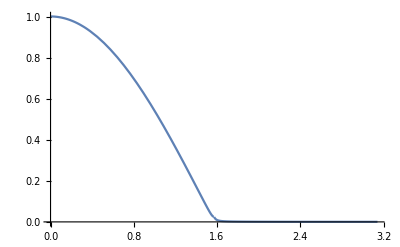

```mathematica
Plot[Last[xj[η]]+Δx[η]/rE,{η,0,Pi}]
```

```mathematica
V[100 mol/cm^3]
```

0.00003868

```mathematica
MatrixExp[-I 100  m*Htilde[33 Degree, 45 Degree, 10^-5 eV^2, 10^-3 eV^2, 100 mol/cm^3, 10 MeV]//Chop]//MatrixForm
```

((-0.0381594-0.00757235 ⅈ) ((0.+0. ⅈ)-(0.0381594-0.00757235 ⅈ) (ⅇ^(-(1.08887×10^-20 cm^3 MeV)/mol) Cos[(0.00001205 cm^3 MeV)/mol]-ⅈ ⅇ^(-(1.08887×10^-20 cm^3 MeV)/mol) Sin[(0.00001205 cm^3 MeV)/mol]))-(0.356752-0.710486 ⅈ) ((0.+0. ⅈ)-(0.356752+0.710486 ⅈ) (ⅇ^((5.41407×10^-20 cm^3 MeV)/mol) Cos[(0.000272205 cm^3 MeV)/mol]-ⅈ ⅇ^((5.41407×10^-20 cm^3 MeV)/mol) Sin[(0.000272205 cm^3 MeV)/mol]))-(0.0115188+0.60522 ⅈ) ((0.+0. ⅈ)-(0.0115188-0.60522 ⅈ) (1. Cos[(0.00266087 cm^3 MeV)/mol]-(0.+1. ⅈ) Sin[(0.00266087 cm^3 MeV)/mol])) | (-0.0381594-0.00757235 ⅈ) ((0.+0. ⅈ)+(0.979714-0.194415 ⅈ) (ⅇ^(-(1.08887×10^-20 cm^3 MeV)/mol) Cos[(0.00001205 cm^3 MeV)/mol]-ⅈ ⅇ^(-(1.08887×10^-20 cm^3 MeV)/mol) Sin[(0.00001205 cm^3 MeV)/mol]))-(0.356752-0.710486 ⅈ) ((0.+0. ⅈ)-(0.021811+0.0434375 ⅈ) (ⅇ^((5.41407×10^-20 cm^3 MeV)/mol) Cos[(0.000272205 cm^3 MeV)/mol]-ⅈ ⅇ^((5.41407×10^-20 cm^3 MeV)/mol) Sin[(0.000272205 cm^3 MeV)/mol]))-(0.0115188+0.60522 ⅈ) ((0.+0. ⅈ)-(6.74834×10^-6-0.000354569 ⅈ) (1. Cos[(0.00266087 cm^3 MeV)/mol]-(0.+1. ⅈ) Sin[(0.00266087 cm^3 MeV)/mol])) | (-0.0381594-0.00757235 ⅈ) ((0.+0. ⅈ)+(0.0285833-0.00567206 ⅈ) (ⅇ^(-(1.08887×10^-20 cm^3 MeV)/mol) Cos[(0.00001205 cm^3 MeV)/mol]-ⅈ ⅇ^(-(1.08887×10^-20 cm^3 MeV)/mol) Sin[(0.00001205 cm^3 MeV)/mol]))-(0.356752-0.710486 ⅈ) ((0.+0. ⅈ)+(0.271315+0.540335 ⅈ) (ⅇ^((5.41407×10^-20 cm^3 MeV)/mol) Cos[(0.000272205 cm^3 MeV)/mol]-ⅈ ⅇ^((5.41407×10^-20 cm^3 MeV)/mol) Sin[(0.000272205 cm^3 MeV)/mol]))-(0.0115188+0.60522 ⅈ) ((0.+0. ⅈ)-(0.0151466-0.795831 ⅈ) (1. Cos[(0.00266087 cm^3 MeV)/mol]-(0.+1. ⅈ) Sin[(0.00266087 cm^3 MeV)/mol]))
(0.979714+0.194415 ⅈ) ((0.+0. ⅈ)-(0.0381594-0.00757235 ⅈ) (ⅇ^(-(1.08887×10^-20 cm^3 MeV)/mol) Cos[(0.00001205 cm^3 MeV)/mol]-ⅈ ⅇ^(-(1.08887×10^-20 cm^3 MeV)/mol) Sin[(0.00001205 cm^3 MeV)/mol]))-(0.021811-0.0434375 ⅈ) ((0.+0. ⅈ)-(0.356752+0.710486 ⅈ) (ⅇ^((5.41407×10^-20 cm^3 MeV)/mol) Cos[(0.000272205 cm^3 MeV)/mol]-ⅈ ⅇ^((5.41407×10^-20 cm^3 MeV)/mol) Sin[(0.000272205 cm^3 MeV)/mol]))-(6.74834×10^-6+0.000354569 ⅈ) ((0.+0. ⅈ)-(0.0115188-0.60522 ⅈ) (1. Cos[(0.00266087 cm^3 MeV)/mol]-(0.+1. ⅈ) Sin[(0.00266087 cm^3 MeV)/mol])) | (0.979714+0.194415 ⅈ) ((0.+0. ⅈ)+(0.979714-0.194415 ⅈ) (ⅇ^(-(1.08887×10^-20 cm^3 MeV)/mol) Cos[(0.00001205 cm^3 MeV)/mol]-ⅈ ⅇ^(-(1.08887×10^-20 cm^3 MeV)/mol) Sin[(0.00001205 cm^3 MeV)/mol]))-(0.021811-0.0434375 ⅈ) ((0.+0. ⅈ)-(0.021811+0.0434375 ⅈ) (ⅇ^((5.41407×10^-20 cm^3 MeV)/mol) Cos[(0.000272205 cm^3 MeV)/mol]-ⅈ ⅇ^((5.41407×10^-20 cm^3 MeV)/mol) Sin[(0.000272205 cm^3 MeV)/mol]))-(6.74834×10^-6+0.000354569 ⅈ) ((0.+0. ⅈ)-(6.74834×10^-6-0.000354569 ⅈ) (1. Cos[(0.00266087 cm^3 MeV)/mol]-(0.+1. ⅈ) Sin[(0.00266087 cm^3 MeV)/mol])) | (0.979714+0.194415 ⅈ) ((0.+0. ⅈ)+(0.0285833-0.00567206 ⅈ) (ⅇ^(-(1.08887×10^-20 cm^3 MeV)/mol) Cos[(0.00001205 cm^3 MeV)/mol]-ⅈ ⅇ^(-(1.08887×10^-20 cm^3 MeV)/mol) Sin[(0.00001205 cm^3 MeV)/mol]))-(0.021811-0.0434375 ⅈ) ((0.+0. ⅈ)+(0.271315+0.540335 ⅈ) (ⅇ^((5.41407×10^-20 cm^3 MeV)/mol) Cos[(0.000272205 cm^3 MeV)/mol]-ⅈ ⅇ^((5.41407×10^-20 cm^3 MeV)/mol) Sin[(0.000272205 cm^3 MeV)/mol]))-(6.74834×10^-6+0.000354569 ⅈ) ((0.+0. ⅈ)-(0.0151466-0.795831 ⅈ) (1. Cos[(0.00266087 cm^3 MeV)/mol]-(0.+1. ⅈ) Sin[(0.00266087 cm^3 MeV)/mol]))
(0.0285833+0.00567206 ⅈ) ((0.+0. ⅈ)-(0.0381594-0.00757235 ⅈ) (ⅇ^(-(1.08887×10^-20 cm^3 MeV)/mol) Cos[(0.00001205 cm^3 MeV)/mol]-ⅈ ⅇ^(-(1.08887×10^-20 cm^3 MeV)/mol) Sin[(0.00001205 cm^3 MeV)/mol]))+(0.271315-0.540335 ⅈ) ((0.+0. ⅈ)-(0.356752+0.710486 ⅈ) (ⅇ^((5.41407×10^-20 cm^3 MeV)/mol) Cos[(0.000272205 cm^3 MeV)/mol]-ⅈ ⅇ^((5.41407×10^-20 cm^3 MeV)/mol) Sin[(0.000272205 cm^3 MeV)/mol]))-(0.0151466+0.795831 ⅈ) ((0.+0. ⅈ)-(0.0115188-0.60522 ⅈ) (1. Cos[(0.00266087 cm^3 MeV)/mol]-(0.+1. ⅈ) Sin[(0.00266087 cm^3 MeV)/mol])) | (0.0285833+0.00567206 ⅈ) ((0.+0. ⅈ)+(0.979714-0.194415 ⅈ) (ⅇ^(-(1.08887×10^-20 cm^3 MeV)/mol) Cos[(0.00001205 cm^3 MeV)/mol]-ⅈ ⅇ^(-(1.08887×10^-20 cm^3 MeV)/mol) Sin[(0.00001205 cm^3 MeV)/mol]))+(0.271315-0.540335 ⅈ) ((0.+0. ⅈ)-(0.021811+0.0434375 ⅈ) (ⅇ^((5.41407×10^-20 cm^3 MeV)/mol) Cos[(0.000272205 cm^3 MeV)/mol]-ⅈ ⅇ^((5.41407×10^-20 cm^3 MeV)/mol) Sin[(0.000272205 cm^3 MeV)/mol]))-(0.0151466+0.795831 ⅈ) ((0.+0. ⅈ)-(6.74834×10^-6-0.000354569 ⅈ) (1. Cos[(0.00266087 cm^3 MeV)/mol]-(0.+1. ⅈ) Sin[(0.00266087 cm^3 MeV)/mol])) | (0.0285833+0.00567206 ⅈ) ((0.+0. ⅈ)+(0.0285833-0.00567206 ⅈ) (ⅇ^(-(1.08887×10^-20 cm^3 MeV)/mol) Cos[(0.00001205 cm^3 MeV)/mol]-ⅈ ⅇ^(-(1.08887×10^-20 cm^3 MeV)/mol) Sin[(0.00001205 cm^3 MeV)/mol]))+(0.271315-0.540335 ⅈ) ((0.+0. ⅈ)+(0.271315+0.540335 ⅈ) (ⅇ^((5.41407×10^-20 cm^3 MeV)/mol) Cos[(0.000272205 cm^3 MeV)/mol]-ⅈ ⅇ^((5.41407×10^-20 cm^3 MeV)/mol) Sin[(0.000272205 cm^3 MeV)/mol]))-(0.0151466+0.795831 ⅈ) ((0.+0. ⅈ)-(0.0151466-0.795831 ⅈ) (1. Cos[(0.00266087 cm^3 MeV)/mol]-(0.+1. ⅈ) Sin[(0.00266087 cm^3 MeV)/mol])))

```mathematica
(* Check with 3 flavour *)
```

```mathematica
list=Table[{e,PSE3[ArcTan[√0.469],ArcSin[√0.01],7.9 10^-5 eV^2, 2.46 10^-3 eV^2, e MeV, 1.35, 200 10^3]},{e,0.1,20,0.05}];
list2=Table[{e,PSE3[ArcTan[√0.469],ArcSin[√0.01],7.9 10^-5 eV^2, 2.46 10^-3 eV^2, e MeV, 0.5, 200 10^3]},{e,0.1,20,0.05}];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {0.036125}. NIntegrate obtained 0.562579 and 1.37681×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {0.0371016}. NIntegrate obtained 0.346402 and 7.52388×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {0.036125}. NIntegrate obtained 0.561184 and 1.37682×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {0.036125}. NIntegrate obtained 0.562579 and 1.37681×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {0.0371016}. NIntegrate obtained 0.346402 and 7.52388×10^-7 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {0.036125}. NIntegrate obtained 0.561184 and 1.37682×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

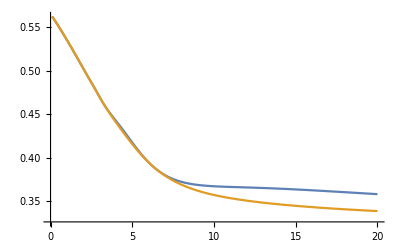

```mathematica
ListPlot[{list,list2},Joined->True]
```

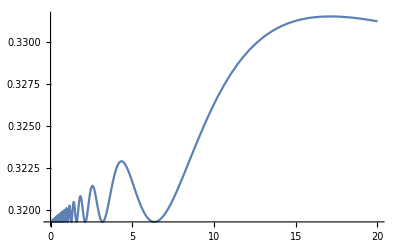

```mathematica
Plot[P2eSolar2[ArcTan[√0.469],7.9 10^-5 eV^2, e MeV, 0.5, 200 10^3],{e,0,20}]
```

```mathematica
NchordInt[Pi/2]/(Last[xj[Pi/2]]+Δx[Pi/2]/rE)
```

39.9124 NchordInt[π/2]

```mathematica
(Last[xj[Pi/2]]+Δx[Pi/2]/rE)
```

0.0250549

```mathematica
Plot[{Pe[33 Degree,7.5 10^-5 eV^2,e MeV, Pi/2],P2eSolar[33 Degree,7.5 10^-5 eV^2,e MeV, Pi/2]},{e,0,20}]
```

MatrixExp::eivn: Incorrect number 0 of eigenvectors for eigenvalue -1. √(-3.44299×10^8+9299.2 NchordInt[1.5708]-0.379549 NchordInt[1.5708]^2) with multiplicity 1.

Part::partw: Part 2 of MatrixExp[{{(0.-1.59275×10^6 ⅈ) (-0.00473842+3.868×10^-7 NchordInt[Times[«2»]]),0.-16951.1 ⅈ},{0.-16951.1 ⅈ,(0.-1.59275×10^6 ⅈ) (0.00473842-3.868×10^-7 NchordInt[Times[«2»]])}}] does not exist.

MatrixExp::eivn: Incorrect number 0 of eigenvectors for eigenvalue -1. √(-344.299+9.29919 NchordInt[1.5708]-0.379549 NchordInt[1.5708]^2) with multiplicity 1.

Part::partw: Part 2 of MatrixExp[{{(0.-1.59275×10^6 ⅈ) (-4.73842×10^-6+3.868×10^-7 NchordInt[Times[«2»]]),0.-16.9511 ⅈ},{0.-16.9511 ⅈ,(0.-1.59275×10^6 ⅈ) (4.73842×10^-6-3.868×10^-7 NchordInt[Times[«2»]])}}] does not exist.

MatrixExp::eivn: Incorrect number 0 of eigenvectors for eigenvalue -1. √(-86.1608+4.65192 NchordInt[1.5708]-0.379549 NchordInt[1.5708]^2) with multiplicity 1.

General::stop: Further output of MatrixExp::eivn will be suppressed during this calculation.

Part::partw: Part 2 of MatrixExp[{{(0.-1.59275×10^6 ⅈ) (-2.37039×10^-6+3.868×10^-7 NchordInt[Times[«2»]]),0.-8.47979 ⅈ},{0.-8.47979 ⅈ,(0.-1.59275×10^6 ⅈ) (2.37039×10^-6-3.868×10^-7 NchordInt[Times[«2»]])}}] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

-Graphics-

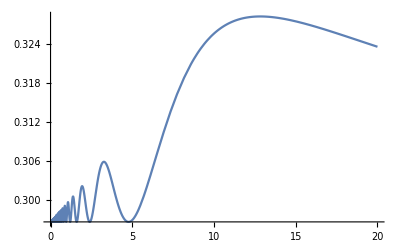

```mathematica
Plot[P2eSolar2[33 Degree,7.5 10^-5 eV^2, e MeV,1.67, 159 10^3],{e,0,20}]
```

```mathematica
Pe[33 Degree,7.5 10^-5 eV^2, 10 MeV,0]
```

MatrixExp::eivn: Incorrect number 0 of eigenvectors for eigenvalue -1. √(-916.138+15.169 NchordInt[0.]-0.379549 NchordInt[0.]^2) with multiplicity 1.

Part::partw: Part 2 of MatrixExp[{{(0.-1.59275×10^6 ⅈ) (-7.72941×10^-6+3.868×10^-7 NchordInt[0]),0.-27.651 ⅈ},{0.-27.651 ⅈ,(0.-1.59275×10^6 ⅈ) (7.72941×10^-6-3.868×10^-7 NchordInt[0])}}] does not exist.

{{Abs[(0.-867474. ⅈ) (-7.72941×10^-6+3.868×10^-7 NchordInt[0])+Cos[33 °] (MatrixExp[{{(0.-1.59275×10^6 ⅈ) (-7.72941×10^-6+3.868×10^-7 NchordInt[0]),0.-27.651 ⅈ},{0.-27.651 ⅈ,(0.-1.59275×10^6 ⅈ) (7.72941×10^-6-3.868×10^-7 NchordInt[0])}}].Transpose[MatrixExp[{{(0.-1.59275×10^6 ⅈ) (-7.72941×10^-6+3.868×10^-7 NchordInt[0]),0.-27.651 ⅈ},{0.-27.651 ⅈ,(0.-1.59275×10^6 ⅈ) (7.72941×10^-6-3.868×10^-7 NchordInt[0])}}]])⟦1,2⟧]^2,Abs[(0.-15.0598 ⅈ)+Cos[33 °] (MatrixExp[{{(0.-1.59275×10^6 ⅈ) (-7.72941×10^-6+3.868×10^-7 NchordInt[0]),0.-27.651 ⅈ},{0.-27.651 ⅈ,(0.-1.59275×10^6 ⅈ) (7.72941×10^-6-3.868×10^-7 NchordInt[0])}}].Transpose[MatrixExp[{{(0.-1.59275×10^6 ⅈ) (-7.72941×10^-6+3.868×10^-7 NchordInt[0]),0.-27.651 ⅈ},{0.-27.651 ⅈ,(0.-1.59275×10^6 ⅈ) (7.72941×10^-6-3.868×10^-7 NchordInt[0])}}]])⟦1,2⟧]^2},{Abs[(0.-15.0598 ⅈ)+Cos[33 °] (MatrixExp[{{(0.-1.59275×10^6 ⅈ) (-7.72941×10^-6+3.868×10^-7 NchordInt[0]),0.-27.651 ⅈ},{0.-27.651 ⅈ,(0.-1.59275×10^6 ⅈ) (7.72941×10^-6-3.868×10^-7 NchordInt[0])}}].Transpose[MatrixExp[{{(0.-1.59275×10^6 ⅈ) (-7.72941×10^-6+3.868×10^-7 NchordInt[0]),0.-27.651 ⅈ},{0.-27.651 ⅈ,(0.-1.59275×10^6 ⅈ) (7.72941×10^-6-3.868×10^-7 NchordInt[0])}}]])⟦1,2⟧]^2,Abs[(0.-867474. ⅈ) (7.72941×10^-6-3.868×10^-7 NchordInt[0])+Cos[33 °] (MatrixExp[{{(0.-1.59275×10^6 ⅈ) (-7.72941×10^-6+3.868×10^-7 NchordInt[0]),0.-27.651 ⅈ},{0.-27.651 ⅈ,(0.-1.59275×10^6 ⅈ) (7.72941×10^-6-3.868×10^-7 NchordInt[0])}}].Transpose[MatrixExp[{{(0.-1.59275×10^6 ⅈ) (-7.72941×10^-6+3.868×10^-7 NchordInt[0]),0.-27.651 ⅈ},{0.-27.651 ⅈ,(0.-1.59275×10^6 ⅈ) (7.72941×10^-6-3.868×10^-7 NchordInt[0])}}]])⟦1,2⟧]^2}}

```mathematica
NchordInt[Pi/2]
```

NchordInt[π/2]

```mathematica
Last[xj[Pi/2]]
```

0

```mathematica
N[Pi/2]
```

1.5708

```mathematica
Plot[NchordInt[η]/(Last[xj[η]]+Δx[η]/rE),{η,0,Pi},Exclusions->None]
```

-Graphics-

```mathematica
Plot[P2eSolar[33 Degree,7.9 10^-5 eV^2,20 MeV,η],{η,1.5 Pi/2,2.5 Pi/2}]
```

Last::normal: Nonatomic expression expected at position 1 in Last[Null].

General::stop: Further output of Last::normal will be suppressed during this calculation.

-Graphics-

```mathematica
Plot[{Pe[33 Degree,7.5 10^-5 eV^2, 10 MeV,η],P2eSolar[33 Degree,7.5 10^-5 eV^2, 10 MeV,η]},{η,0,Pi/2}]
```

-Graphics-

```mathematica
Plot[{Pe[33 Degree,7.5 10^-5 eV^2, e MeV,Pi/2.1],P2eSolar[33 Degree,7.5 10^-5 eV^2, e MeV,Pi/2.1]},{e,10,15}]
```

-Graphics-

```mathematica
Plot[2(P2eSolar[33 Degree,1.5 10^-5 eV^2, e MeV,0]-Pe[33 Degree,1.5 10^-5 eV^2, e MeV,0])/(P2eSolar[33 Degree,1.5 10^-5 eV^2, e MeV,0]+Pe[33 Degree,1.5 10^-5 eV^2, e MeV,0]),{e,0,16}]
```

MatrixExp::eivn: Incorrect number 0 of eigenvectors for eigenvalue -1. √(-3.43008×10^10+92817.5 NchordInt[0.]-0.379549 NchordInt[0.]^2) with multiplicity 1.

Part::partw: Part 2 of MatrixExp[{{(0.-1.59275×10^6 ⅈ) (-0.0472953+3.868×10^-7 NchordInt[0]),0.-169193. ⅈ},{0.-169193. ⅈ,(0.-1.59275×10^6 ⅈ) (0.0472953-3.868×10^-7 NchordInt[0])}}] does not exist.

MatrixExp::eivn: Incorrect number 0 of eigenvectors for eigenvalue -1. √(-3.43008×10^10+92817.5 NchordInt[0.]-0.379549 NchordInt[0.]^2) with multiplicity 1.

Part::partw: Part 2 of MatrixExp[{{(0.-1.59275×10^6 ⅈ) (-0.0472953+3.868×10^-7 NchordInt[0]),0.-169193. ⅈ},{0.-169193. ⅈ,(0.-1.59275×10^6 ⅈ) (0.0472953-3.868×10^-7 NchordInt[0])}}] does not exist.

MatrixExp::eivn: Incorrect number 0 of eigenvectors for eigenvalue -1. √(-34300.8+92.8174 NchordInt[0.]-0.379549 NchordInt[0.]^2) with multiplicity 1.

General::stop: Further output of MatrixExp::eivn will be suppressed during this calculation.

Part::partw: Part 2 of MatrixExp[{{(0.-1.59275×10^6 ⅈ) (-0.0000472953+3.868×10^-7 NchordInt[0]),0.-169.193 ⅈ},{0.-169.193 ⅈ,(0.-1.59275×10^6 ⅈ) (0.0000472953-3.868×10^-7 NchordInt[0])}}] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

-Graphics-

```mathematica
Timing[Nint[Pi/2.1]]
```

{0.000423,{0.124662,0.00682806}}

```mathematica
3^3
```

27

```mathematica
xj[0]
```

{0,0.192,0.546,0.895,0.937,1}

```mathematica
Last[xj[Pi/2.1]]
```

0.0747301

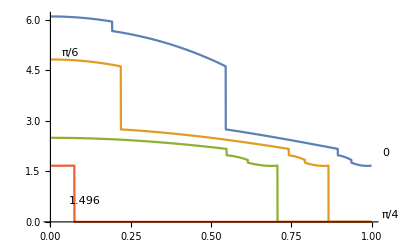

```mathematica
Plot[{Nchord[0,x],Nchord[Pi/6,x],Nchord[Pi/4,x],Nchord[Pi/2.1,x]},{x,0,1},Exclusions->None, PlotLabels->Placed[{0, Pi/6, Pi/4, Pi/2.1},{Automatic,Above}]]
```

```mathematica
Nint[η_] := Integrate[Nchord[η,x],{x,0,1}];
```

```mathematica
Nint[Pi/2.1]/0.074
```

1.68462

```mathematica
Clear[Nint]
```

```mathematica
n=4 10^3;
Δr = 1/n;
```

```mathematica
list = Table[Chop[MatrixExp[-I (rE*Δr)H[i Δr,33 Degree, 10^-5 eV^2, 10MeV]]],{i,n,-n,-1}];
```

```mathematica
Ugen[r0_,r1_,th_, δm2_, e_]:=MatrixExp[-I rE Integrate[H[r,th,δm2,e],{r,r0,r1}]]
```

```mathematica
U[-1,-1+10Δr,33 Degree, 10^-5 eV^2, 10MeV]
```

U[-1,-399/400,33 °,eV^2/100000,10 MeV]

```mathematica
U[33 Degree, 10^-5 eV^2, 10MeV]
```

U[33 °,eV^2/100000,10 MeV]

```mathematica
list[[-10;;-1]]
```

{{{0.999998+0.000820476 ⅈ,0.-0.00184282 ⅈ},{0.-0.00184282 ⅈ,0.999998-0.000820476 ⅈ}},{{0.999998+0.000820476 ⅈ,0.-0.00184282 ⅈ},{0.-0.00184282 ⅈ,0.999998-0.000820476 ⅈ}},{{0.999998+0.000820476 ⅈ,0.-0.00184282 ⅈ},{0.-0.00184282 ⅈ,0.999998-0.000820476 ⅈ}},{{0.999998+0.000820476 ⅈ,0.-0.00184282 ⅈ},{0.-0.00184282 ⅈ,0.999998-0.000820476 ⅈ}},{{0.999998+0.000820476 ⅈ,0.-0.00184282 ⅈ},{0.-0.00184282 ⅈ,0.999998-0.000820476 ⅈ}},{{0.999998+0.000820476 ⅈ,0.-0.00184282 ⅈ},{0.-0.00184282 ⅈ,0.999998-0.000820476 ⅈ}},{{0.999998+0.000820476 ⅈ,0.-0.00184282 ⅈ},{0.-0.00184282 ⅈ,0.999998-0.000820476 ⅈ}},{{0.999998+0.000820476 ⅈ,0.-0.00184282 ⅈ},{0.-0.00184282 ⅈ,0.999998-0.000820476 ⅈ}},{{0.999998+0.000820476 ⅈ,0.-0.00184282 ⅈ},{0.-0.00184282 ⅈ,0.999998-0.000820476 ⅈ}},{{0.999998+0.000820476 ⅈ,0.-0.00184282 ⅈ},{0.-0.00184282 ⅈ,0.999998-0.000820476 ⅈ}}}

```mathematica
Apply[Dot,list[[-10;;-1]]]
```

{{0.999797+0.00820421 ⅈ,-5.0822×10^-21-0.018427 ⅈ},{3.38813×10^-21-0.018427 ⅈ,0.999797-0.00820421 ⅈ}}

```mathematica
U[33 Degree, 10^-5 eV^2, 10MeV]
```

U[33 °,eV^2/100000,10 MeV]

```mathematica
H[0,33 Degree, 10^-5 eV^2, 10MeV]
```

{{6.64415×10^-7,1.15701×10^-6},{1.15701×10^-6,-6.64415×10^-7}}

```mathematica
Nint
```

Nint

```mathematica
Ugen[0,1,33 Degree, 10^-5 eV^2, 10MeV]
```

{{0.279646-0.218836 ⅈ,0.-0.934831 ⅈ},{0.-0.934831 ⅈ,0.279646+0.218836 ⅈ}}

```mathematica
U[33 Degree, 10^-5 eV^2, 10MeV]
```

U[33 °,eV^2/100000,10 MeV]

```mathematica
Plot[Pe[33 Degree,1.5 10^-5 eV^2, e MeV],{e,16,0.05},PlotRange->{Automatic,{0,1}}]
```

-Graphics-

```mathematica
ArcSin[√0.64]/2/Degree
```

26.5651

```mathematica
Nint
```

Nint

```mathematica
list1=Table[{e,PSE[ArcSin[√0.64]/2,1.5 10^-5 eV^2, e MeV]},{e,0.1,16,0.05}];
```

```mathematica
LMA = Interpolation[Import[NotebookDirectory[]<>"Data/9702343_LMA.csv"],InterpolationOrder->1];
```

Import::nffil: File /Users/michele/Coding/solar-nu-flux/Code/Data/9702343_LMA.csv not found during Import.

Interpolation::innd: First argument in $Failed does not contain a list of data and coordinates.

```mathematica
Show[ListPlot[list1,Joined->True],Plot[LMA[e],{e,0,16},PlotStyle->{Dashed,Green}]]
```

Interpolation::innd: First argument in $Failed does not contain a list of data and coordinates.

General::stop: Further output of Interpolation::innd will be suppressed during this calculation.

-Graphics-

```mathematica
Nebar[η_]:=Table[((αp[η][[i]]*(xj[η][[i+1]]-xj[η][[i]]) + βp[η][[i]] (xj[η][[i+1]]^3-xj[η][[i]]^3)/3 + γp[η][[i]] (xj[η][[i+1]]^5-xj[η][[i]]^5)/5)/(xj[η][[i+1]]-xj[η][[i]]))*(mol/cm^3),{i,Length[xj[η]]-1}];
```

```mathematica
δNe[η_,x_]:=Piecewise[Table[{(αp[η][[i]] + βp[η][[i]] x^2 + γp[η][[i]] x^4)*(mol/cm^3) - Nebar[η][[i]],xj[η][[i]]≤x<xj[η][[i+1]]},{i,Length[xj[η]]-1}]];
```

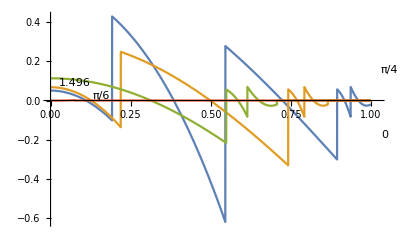

```mathematica
Plot[{δNe[0,x]/(mol/cm^3),δNe[Pi/6,x]/(mol/cm^3),δNe[Pi/4,x]/(mol/cm^3),δNe[Pi/2.1,x]/(mol/cm^3)},{x,0,1},Exclusions->None, PlotLabels->Placed[{0, Pi/6, Pi/4, Pi/2.1},{Automatic,Above}],PlotRange->All]
```

```mathematica
sin2thm[th_,δm2_,e_,Njbar_] := Sin[2th]/√((Cos[2th]-V[Njbar]/k[δm2,e])^2 + Sin[2th]^2);
cos2thm[th_,δm2_,e_,Njbar_] := √(1 - sin2thm[th,δm2,e,Njbar]^2);
km[th_,δm2_,e_,Njbar_] := k[δm2,e]*(Sin[2th]/sin2thm[th,δm2,e,Njbar]);

x[η_]:=Table[Mean[{xj[η][[i+1]],xj[η][[i]]}],{i,Length[xj[η]]-1}];
```

```mathematica
rE = 6.3781*10^6 m;
```

```mathematica
cj[th_,δm2_,e_,η_]:=Table[Cos[km[th,δm2,e,Nebar[η][[i]]]*(xj[η][[i+1]]-xj[η][[i]])rE/2],{i,Length[x[η]]}];
sj[th_,δm2_,e_,η_]:=Table[Sin[km[th,δm2,e,Nebar[η][[i]]]*(xj[η][[i+1]]-xj[η][[i]])rE/2],{i,Length[x[η]]}];
```

```mathematica
Cj0[kbar_,xbar_,x1_,x2_,r_]=Simplify[Integrate[Cos[kbar*r(x-xbar)],{x,x1,x2}]];
Cj2[kbar_,xbar_,x1_,x2_,r_]=Simplify[Integrate[x^2 Cos[kbar*r(x-xbar)],{x,x1,x2}]];
Cj4[kbar_,xbar_,x1_,x2_,r_]=Simplify[Integrate[x^4 Cos[kbar*r(x-xbar)],{x,x1,x2}]];

Sj0[kbar_,xbar_,x1_,x2_,r_]=Simplify[Integrate[Sin[kbar*r(x-xbar)],{x,x1,x2}]];
Sj2[kbar_,xbar_,x1_,x2_,r_]=Simplify[Integrate[x^2 Sin[kbar*r(x-xbar)],{x,x1,x2}]];
Sj4[kbar_,xbar_,x1_,x2_,r_]=Simplify[Integrate[x^4 Sin[kbar*r(x-xbar)],{x,x1,x2}]];
```

```mathematica
?Cj0
```

```mathematica
Cj[th_,δm2_,e_,η_]:=rE*Table[V[(αp[η][[i]]*(mol/cm^3)-Nebar[η][[i]])]*Cj0[km[th,δm2,e,Nebar[η][[i]]],x[η][[i]],xj[η][[i]],xj[η][[i+1]],rE]+
 V[βp[η][[i]]*(mol/cm^3)]*Cj2[km[th,δm2,e,Nebar[η][[i]]],x[η][[i]],xj[η][[i]],xj[η][[i+1]],rE]+
V[γp[η][[i]]*(mol/cm^3)]*Cj4[km[th,δm2,e,Nebar[η][[i]]],x[η][[i]],xj[η][[i]],xj[η][[i+1]],rE] ,{i,Length[xj[η]]-1}];
Sj[th_,δm2_,e_,η_]:=rE*Table[V[(αp[η][[i]]*(mol/cm^3)-Nebar[η][[i]])]*Sj0[km[th,δm2,e,Nebar[η][[i]]],x[η][[i]],xj[η][[i]],xj[η][[i+1]],rE]+
 V[βp[η][[i]]*(mol/cm^3)]*Sj2[km[th,δm2,e,Nebar[η][[i]]],x[η][[i]],xj[η][[i]],xj[η][[i+1]],rE]+
V[γp[η][[i]]*(mol/cm^3)]*Sj4[km[th,δm2,e,Nebar[η][[i]]],x[η][[i]],xj[η][[i]],xj[η][[i+1]],rE] ,{i,Length[xj[η]]-1}];
```

```mathematica
Uj[th_,δm2_,e_,η_]:= Chop[Module[{c=cj[th,δm2,e,η], s=sj[th,δm2,e,η],C=Cj[th,δm2,e,η],S=Sj[th,δm2,e,η],c2thm = cos2thm[th,δm2,e,Nebar[η]], s2thm = sin2thm[th,δm2,e,Nebar[η]]},
Table[{
{c[[i]] + I s[[i]]*c2thm[[i]], - I s[[i]]*s2thm[[i]]},
{- I s[[i]]*s2thm[[i]], c[[i]] - I s[[i]]*c2thm[[i]]}
}
 - (I/2)*s2thm[[i]]*{
{C[[i]]*s2thm[[i]], C[[i]]*c2thm[[i]] - I S[[i]]},
{C[[i]]*c2thm[[i]] + I S[[i]], -C[[i]]*s2thm[[i]]} 
} ,{i,Length[xj[η]]-1}]]];
```

```mathematica
Table[{e,Abs[UIF[ArcSin[√0.64]/2,1.5 10^-5 eV^2, e MeV,0]][[1,1]]},{e,0.1,16}]
```

{{0.1,0.463648},{1.1,0.463648},{2.1,0.463648},{3.1,0.463648},{4.1,0.463648},{5.1,0.463648},{6.1,0.463648},{7.1,0.463648},{8.1,0.463648},{9.1,0.463648},{10.1,0.463648},{11.1,0.463648},{12.1,0.463648},{13.1,0.463648},{14.1,0.463648},{15.1,0.463648}}

```mathematica
ListPlot[{%440,%442}]
```

-Graphics-

```mathematica
Table[{e,Abs[UIF[ArcSin[√0.64]/2,1.5 10^-5 eV^2, e MeV,0]][[1,1]]},{e,0.1,16}]
```

{{0.1,0.463648},{1.1,0.463648},{2.1,0.463648},{3.1,0.463648},{4.1,0.463648},{5.1,0.463648},{6.1,0.463648},{7.1,0.463648},{8.1,0.463648},{9.1,0.463648},{10.1,0.463648},{11.1,0.463648},{12.1,0.463648},{13.1,0.463648},{14.1,0.463648},{15.1,0.463648}}

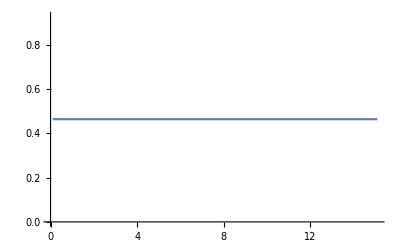

```mathematica
ListPlot[Table[{e,Abs[U0F[ArcSin[√0.64]/2,1.5 10^-5 eV^2, e MeV,0]][[1,1]]},{e,0.1,16}],Joined->True]
```

```mathematica
ListPlot[Table[{e,Abs[U0F[ArcSin[√0.64]/2,1.5 10^-5 eV^2, e MeV,0]][[1,1]]},{e,0.1,16}],Joined->True]
```

-Graphics-

```mathematica
U0F[th_,δm2_,e_,η_]:=Chop[ Module[{list = Table[Uj[th,δm2,e,η][[i]],{i,Length[xj[η]]-1}]}, Apply[Dot,list]]];
UIF[th_,δm2_,e_,η_]:=Chop[Module[{u = U0F[th,δm2,e,η]},u.uᵀ]];
```

```mathematica
Pe[th_,δm2_,e_,η_]:= Module[{Uee = UIF[th,δm2,e,η]}, Abs[Uee[[1,1]] Sin[th] + Uee[[1,2]] Cos[th]]^2]
```

```mathematica
PS[th_, δm2_,e_] := NIntegrate[Pveve[th,0,δm2,100 eV^2,e,density[r]]*B8radial[r]/B8int,{r,0,0.5}];
```

```mathematica
PSE[th_, δm2_,e_, η_] := Module[{ps = PS[th,δm2,e], pe = Pe[th,δm2,e, η]},
ps + (2ps-1)(Sin[th]^2-pe)/Cos[2th]]
```

```mathematica
U0F[ArcSin[√0.64]/2,1.5 10^-5 eV^2, 14 MeV,0] //MatrixForm
```

(0.601368+0.266004 ⅈ | -0.174271-0.740639 ⅈ
0.174271-0.740639 ⅈ | 0.601368-0.266004 ⅈ)

```mathematica
LMA = Interpolation[Import[NotebookDirectory[]<>"Data/9702343_LMA.csv"],InterpolationOrder->1];
```

Import::nffil: File /Users/michele/Coding/solar-nu-flux/Code/Data/9702343_LMA.csv not found during Import.

Interpolation::innd: First argument in $Failed does not contain a list of data and coordinates.

```mathematica
pseLarge = Table[{e,PSE[ArcSin[√0.64]/2,1.5 10^-5 eV^2, e MeV, 0]},{e,0.1,16,0.1}];
psLarge = Table[{e,PS[ArcSin[√0.64]/2,1.5 10^-5 eV^2, e MeV]},{e,0.1,16,0.1}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {0.036125}. NIntegrate obtained 0.660949 and 1.09725×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {0.0449141}. NIntegrate obtained 0.638675 and 1.34234×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {0.0449141}. NIntegrate obtained 0.613043 and 1.48939×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {0.036125}. NIntegrate obtained 0.660949 and 1.09725×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {0.0449141}. NIntegrate obtained 0.638675 and 1.34234×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {0.0449141}. NIntegrate obtained 0.613043 and 1.48939×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

```mathematica
Show[ListPlot[{list,pseLarge},Joined->True],Plot[LMA[e],{e,0.1,16},PlotStyle->{Green,Dashed}]]
```

ListPlot::lpn: {{},{{0.1,0.659788},{0.2,0.6351},{0.3,0.609011},{0.4,0.584232},{0.5,0.546852},«42»,{4.8,0.435932},{4.9,0.224856},{5.,0.338952},«110»}} is not a list of numbers or pairs of numbers.

Interpolation::innd: First argument in $Failed does not contain a list of data and coordinates.

General::stop: Further output of Interpolation::innd will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[ListPlot[{{{{0.999998+0.000820476 ⅈ,0.-0.00184282 ⅈ},{0.-0.00184282 ⅈ,0.999998-0.000820476 ⅈ}},«49»,«7951»},{{0.1,0.659788},{0.2,0.6351},«48»,«110»}},«6»→«4»],].

Show[ListPlot[{{{{0.999998+0.000820476 ⅈ,0.-0.00184282 ⅈ},{0.-0.00184282 ⅈ,0.999998-0.000820476 ⅈ}},7999,{{1,1},1}},1},1],-Graphics-]
 |  |  |  |

```mathematica
Timing[PSE[ArcSin[√0.64]/2,1.5 10^-5 eV^2, 10 MeV, 0]]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {0.036125}. NIntegrate obtained 0.201364 and 4.91638×10^-7 for the integral and error estimates.

{1.04741,0.880687}

```mathematica
Timing[pSE[ArcSin[√0.64]/2,1.5 10^-5 eV^2, 10 MeV]]
```

{0.000024,pSE[0.463648,0.000015 eV^2,10 MeV]}

```mathematica
(* Numerical integration seem to be faster! *)
```

```mathematica
Pe[ArcSin[√0.64]/2,1.5 10^-5 eV^2, 10 MeV,0]
```

0.882426

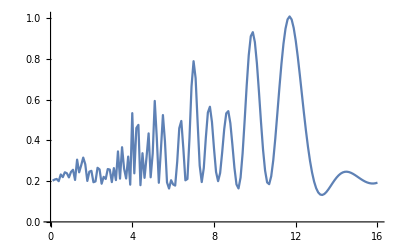

```mathematica
ListPlot[Table[{e,Pe[ArcSin[√0.64]/2,1.5 10^-5 eV^2, e MeV,0]},{e,0.1,16,0.1}],Joined->True]
```

Interpolation::innd: First argument in $Failed does not contain a list of data and coordinates.

General::stop: Further output of Interpolation::innd will be suppressed during this calculation.

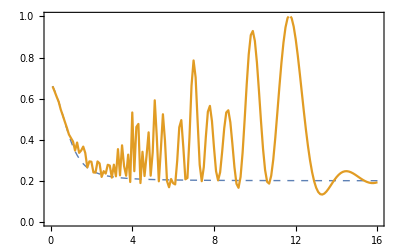

```mathematica
Show[ListPlot[{psLarge,pseLarge},Joined->True,PlotRange->{Automatic,{0,1}},PlotStyle->{{Thin,Dashed},Automatic}],Plot[LMA[e],{e,0,16}],Frame->True]
```

```mathematica
pseSmall = Table[{e,PSE[ArcSin[√(8.1 10^-3)]/2,5.2 10^-6 eV^2, e MeV, 0]},{e,0.1,16,0.1}];
psSmall = Table[{e,PS[ArcSin[√(8.1 10^-3)]/2,5.2 10^-6  eV^2, e MeV]},{e,0.1,16,0.1}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {0.036125}. NIntegrate obtained 0.99424 and 2.42757×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {0.036125}. NIntegrate obtained 0.988761 and 1.69346×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {0.0371016}. NIntegrate obtained 0.943223 and 7.9555×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {0.036125}. NIntegrate obtained 0.99424 and 2.42757×10^-6 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {0.036125}. NIntegrate obtained 0.988761 and 1.69346×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {0.0371016}. NIntegrate obtained 0.943223 and 7.9555×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

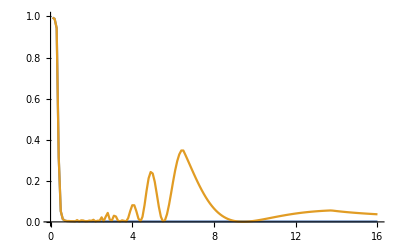

```mathematica
ListPlot[{psSmall,pseSmall},Joined->True,PlotRange->{Automatic,{0,1}}]
```

```mathematica
hbar = {
{√2 Gf Nbar - kk Cos[2th], kk Sin[2th]},
{kk Sin[2th], kk Cos[2th] - √2 Gf Nbar}
}/2;
δh = Gf DiagonalMatrix[{δN,-δN}]/√2;
```

```mathematica
MatrixExp[-I hbar r (xi-xi1)]//Simplify
```

{{(ⅇ^(-1/2 r (xi-xi1) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th])) (-ⅈ √2 (-1+ⅇ^(r (xi-xi1) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th]))) Gf Nbar+ⅈ (-1+ⅇ^(r (xi-xi1) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th]))) kk Cos[2 th]+(1+ⅇ^(r (xi-xi1) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th]))) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th])))/(2 √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th])),-(ⅈ ⅇ^(-1/2 r (xi-xi1) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th])) (-1+ⅇ^(r (xi-xi1) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th]))) kk Sin[2 th])/(2 √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th]))},{-(ⅈ ⅇ^(-1/2 r (xi-xi1) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th])) (-1+ⅇ^(r (xi-xi1) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th]))) kk Sin[2 th])/(2 √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th])),(ⅇ^(-1/2 r (xi-xi1) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th])) (ⅈ √2 (-1+ⅇ^(r (xi-xi1) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th]))) Gf Nbar-ⅈ (-1+ⅇ^(r (xi-xi1) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th]))) kk Cos[2 th]+(1+ⅇ^(r (xi-xi1) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th]))) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th])))/(2 √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th]))}}

```mathematica
MatrixForm[%]
```

((ⅇ^(-1/2 r (xi-xi1) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th])) (-ⅈ √2 (-1+ⅇ^(r (xi-xi1) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th]))) Gf Nbar+ⅈ (-1+ⅇ^(r (xi-xi1) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th]))) kk Cos[2 th]+(1+ⅇ^(r (xi-xi1) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th]))) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th])))/(2 √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th])) | -(ⅈ ⅇ^(-1/2 r (xi-xi1) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th])) (-1+ⅇ^(r (xi-xi1) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th]))) kk Sin[2 th])/(2 √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th]))
-(ⅈ ⅇ^(-1/2 r (xi-xi1) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th])) (-1+ⅇ^(r (xi-xi1) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th]))) kk Sin[2 th])/(2 √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th])) | (ⅇ^(-1/2 r (xi-xi1) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th])) (ⅈ √2 (-1+ⅇ^(r (xi-xi1) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th]))) Gf Nbar-ⅈ (-1+ⅇ^(r (xi-xi1) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th]))) kk Cos[2 th]+(1+ⅇ^(r (xi-xi1) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th]))) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th])))/(2 √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th])))

```mathematica
MatrixExp[-I hbar  r(xi-xx)].δh.MatrixExp[-I hbar r (xx-xi1)]//Simplify
```

{{(ⅇ^(-1/2 r (xi+xi1-2 xx) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th])) Gf δN (kk^2+ⅇ^(r (xi+xi1-2 xx) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th])) kk^2+ⅇ^(r (xi-xx) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th])) kk^2+ⅇ^(r (xi1-xx) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th])) kk^2+4 ⅇ^(r (xi-xx) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th])) Gf^2 Nbar^2+4 ⅇ^(r (xi1-xx) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th])) Gf^2 Nbar^2+2 ⅈ √2 ⅇ^(r (xi-xx) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th])) Gf Nbar √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th])-2 ⅈ √2 ⅇ^(r (xi1-xx) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th])) Gf Nbar √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th])-2 ⅈ kk Cos[2 th] (ⅇ^(r (xi-xx) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th])) (-2 ⅈ √2 Gf Nbar+√(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th]))-ⅇ^(r (xi1-xx) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th])) (2 ⅈ √2 Gf Nbar+√(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th])))-(1+ⅇ^(r (xi+xi1-2 xx) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th]))-ⅇ^(r (xi-xx) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th]))-ⅇ^(r (xi1-xx) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th]))) kk^2 Cos[4 th]))/(4 √2 (kk^2+2 Gf^2 Nbar^2-2 √2 Gf kk Nbar Cos[2 th])),-((ⅇ^(-1/2 r (xi+xi1-2 xx) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th])) Gf kk δN (√2 (1+ⅇ^(r (xi+xi1-2 xx) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th]))-ⅇ^(r (xi-xx) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th]))-ⅇ^(r (xi1-xx) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th]))) Gf Nbar-(1+ⅇ^(r (xi+xi1-2 xx) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th]))-ⅇ^(r (xi-xx) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th]))-ⅇ^(r (xi1-xx) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th]))) kk Cos[2 th]+ⅈ (-1+ⅇ^(r (xi+xi1-2 xx) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th]))) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th])) Sin[2 th])/(2 √2 (kk^2+2 Gf^2 Nbar^2-2 √2 Gf kk Nbar Cos[2 th])))},{-((ⅇ^(-1/2 r (xi+xi1-2 xx) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th])) Gf kk δN (√2 (1+ⅇ^(r (xi+xi1-2 xx) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th]))-ⅇ^(r (xi-xx) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th]))-ⅇ^(r (xi1-xx) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th]))) Gf Nbar-(1+ⅇ^(r (xi+xi1-2 xx) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th]))-ⅇ^(r (xi-xx) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th]))-ⅇ^(r (xi1-xx) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th]))) kk Cos[2 th]-ⅈ (-1+ⅇ^(r (xi+xi1-2 xx) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th]))) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th])) Sin[2 th])/(2 √2 (kk^2+2 Gf^2 Nbar^2-2 √2 Gf kk Nbar Cos[2 th]))),-((ⅇ^(-1/2 r (xi+xi1-2 xx) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th])) Gf δN (kk^2+ⅇ^(r (xi+xi1-2 xx) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th])) kk^2+ⅇ^(r (xi-xx) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th])) kk^2+ⅇ^(r (xi1-xx) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th])) kk^2+4 ⅇ^(r (xi-xx) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th])) Gf^2 Nbar^2+4 ⅇ^(r (xi1-xx) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th])) Gf^2 Nbar^2-2 ⅈ √2 ⅇ^(r (xi-xx) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th])) Gf Nbar √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th])+2 ⅈ √2 ⅇ^(r (xi1-xx) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th])) Gf Nbar √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th])+2 ⅈ kk Cos[2 th] (-ⅇ^(r (xi1-xx) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th])) (-2 ⅈ √2 Gf Nbar+√(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th]))+ⅇ^(r (xi-xx) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th])) (2 ⅈ √2 Gf Nbar+√(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th])))-(1+ⅇ^(r (xi+xi1-2 xx) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th]))-ⅇ^(r (xi-xx) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th]))-ⅇ^(r (xi1-xx) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th]))) kk^2 Cos[4 th]))/(4 √2 (kk^2+2 Gf^2 Nbar^2-2 √2 Gf kk Nbar Cos[2 th])))}}

```mathematica
MatrixForm[%]
```

((ⅇ^(-1/2 r (xi+xi1-2 xx) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th])) Gf δN (kk^2+ⅇ^(r (xi+xi1-2 xx) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th])) kk^2+ⅇ^(r (xi-xx) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th])) kk^2+ⅇ^(r (xi1-xx) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th])) kk^2+4 ⅇ^(r (xi-xx) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th])) Gf^2 Nbar^2+4 ⅇ^(r (xi1-xx) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th])) Gf^2 Nbar^2+2 ⅈ √2 ⅇ^(r (xi-xx) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th])) Gf Nbar √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th])-2 ⅈ √2 ⅇ^(r (xi1-xx) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th])) Gf Nbar √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th])-2 ⅈ kk Cos[2 th] (ⅇ^(r (xi-xx) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th])) (-2 ⅈ √2 Gf Nbar+√(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th]))-ⅇ^(r (xi1-xx) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th])) (2 ⅈ √2 Gf Nbar+√(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th])))-(1+ⅇ^(r (xi+xi1-2 xx) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th]))-ⅇ^(r (xi-xx) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th]))-ⅇ^(r (xi1-xx) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th]))) kk^2 Cos[4 th]))/(4 √2 (kk^2+2 Gf^2 Nbar^2-2 √2 Gf kk Nbar Cos[2 th])) | -(ⅇ^(-1/2 r (xi+xi1-2 xx) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th])) Gf kk δN (√2 (1+ⅇ^(r (xi+xi1-2 xx) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th]))-ⅇ^(r (xi-xx) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th]))-ⅇ^(r (xi1-xx) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th]))) Gf Nbar-(1+ⅇ^(r (xi+xi1-2 xx) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th]))-ⅇ^(r (xi-xx) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th]))-ⅇ^(r (xi1-xx) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th]))) kk Cos[2 th]+ⅈ (-1+ⅇ^(r (xi+xi1-2 xx) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th]))) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th])) Sin[2 th])/(2 √2 (kk^2+2 Gf^2 Nbar^2-2 √2 Gf kk Nbar Cos[2 th]))
-(ⅇ^(-1/2 r (xi+xi1-2 xx) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th])) Gf kk δN (√2 (1+ⅇ^(r (xi+xi1-2 xx) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th]))-ⅇ^(r (xi-xx) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th]))-ⅇ^(r (xi1-xx) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th]))) Gf Nbar-(1+ⅇ^(r (xi+xi1-2 xx) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th]))-ⅇ^(r (xi-xx) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th]))-ⅇ^(r (xi1-xx) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th]))) kk Cos[2 th]-ⅈ (-1+ⅇ^(r (xi+xi1-2 xx) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th]))) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th])) Sin[2 th])/(2 √2 (kk^2+2 Gf^2 Nbar^2-2 √2 Gf kk Nbar Cos[2 th])) | -(ⅇ^(-1/2 r (xi+xi1-2 xx) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th])) Gf δN (kk^2+ⅇ^(r (xi+xi1-2 xx) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th])) kk^2+ⅇ^(r (xi-xx) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th])) kk^2+ⅇ^(r (xi1-xx) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th])) kk^2+4 ⅇ^(r (xi-xx) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th])) Gf^2 Nbar^2+4 ⅇ^(r (xi1-xx) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th])) Gf^2 Nbar^2-2 ⅈ √2 ⅇ^(r (xi-xx) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th])) Gf Nbar √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th])+2 ⅈ √2 ⅇ^(r (xi1-xx) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th])) Gf Nbar √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th])+2 ⅈ kk Cos[2 th] (-ⅇ^(r (xi1-xx) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th])) (-2 ⅈ √2 Gf Nbar+√(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th]))+ⅇ^(r (xi-xx) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th])) (2 ⅈ √2 Gf Nbar+√(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th])))-(1+ⅇ^(r (xi+xi1-2 xx) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th]))-ⅇ^(r (xi-xx) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th]))-ⅇ^(r (xi1-xx) √(-kk^2-2 Gf^2 Nbar^2+2 √2 Gf kk Nbar Cos[2 th]))) kk^2 Cos[4 th]))/(4 √2 (kk^2+2 Gf^2 Nbar^2-2 √2 Gf kk Nbar Cos[2 th])))

```mathematica
rj
```

{0,0.192,0.546,0.895,0.937,1}

```mathematica
nbar = NIntegrate[Ne[r],{r,0,rj[[3]]}]/rj[[3]]*(mol/cm^3)
```

(5.52287 mol)/cm^3

```mathematica
Nebar[0]
```

{(6.04839 mol)/cm^3,(5.23784 mol)/cm^3,(2.46815 mol)/cm^3,(1.92156 mol)/cm^3,(1.68921 mol)/cm^3}

```mathematica
rE
```

6.3781×10^6

```mathematica
H[th_,δm2_,e_, N_] := {
{V[N*(mol/cm^3)]-k[δm2,e]Cos[2th], k[δm2,e]Sin[2th]},
{k[δm2,e] Sin[2th],k[δm2,e] Cos[2th]-V[N*(mol/cm^3)]}
}/2;
```

```mathematica
u[th_,δm2_,e_] := MatrixExp[- I NIntegrate[rE H[th,δm2,e,Ne[r]],{r,-1,1}]];
p[th_,δm2_,e_] := Module[{uu=u[th,δm2,e]},Abs[uu[[1,1]] Sin[th]+uu[[1,2]]Cos[th]]^2]
pSE[th_, δm2_,e_] := Module[{ps = PS[th,δm2,e], pe = p[th,δm2,e]},
ps + (2ps-1)(Sin[th]^2-pe)/Cos[2th]]
```

```mathematica
list = Table[{e,pSE[ArcSin[√0.64]/2,1.5 10^-5 eV^2,e MeV]},{e,1,16,0.1}];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {0.0419844}. NIntegrate obtained 0.391992 and 3.08945×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {0.0419844}. NIntegrate obtained 0.366448 and 3.02693×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {0.0419844}. NIntegrate obtained 0.344135 and 3.00868×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

Interpolation::innd: First argument in $Failed does not contain a list of data and coordinates.

General::stop: Further output of Interpolation::innd will be suppressed during this calculation.

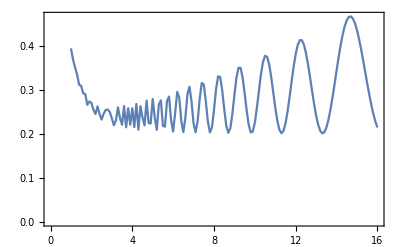

```mathematica
Show[ListPlot[list,Joined->True],Plot[LMA[e],{e,0,16},PlotStyle->Orange],Frame->True]
```

```mathematica
u[th_,δm2_,e_] :=Module[{uu=MatrixExp[- I H[th,δm2,e] rE rj[[3]]]},uu.uuᵀ];
```

```mathematica
p[th_,δm2_,e_] := Abs[u[th,δm2,e][[1,1]] Sin[th]+u[th,δm2,e][[1,2]]Cos[th]]^2
```

```mathematica
pse[th_, δm2_,e_] := Module[{ps = 0.2, pe = p[th,δm2,e]},
ps + (2ps-1)(Sin[th]^2-pe)/Cos[2th]]
```

```mathematica
U0F[th_,δm2_,e_,η_]:=Chop[ Module[{list = Table[Uj[th,δm2,e,η][[i]],{i,2}]}, Apply[Dot,list]]];
```

```mathematica
Pe[ArcSin[√0.64]/2,1.5 10^-5 eV^2, 14  MeV,0]
```

0.479963

```mathematica
p[ArcSin[√0.64]/2,1.5 10^-5 eV^2, 14  MeV]
```

Part::partw: Part 2 of MatrixExp[(0.-3.48244×10^6 ⅈ) H[0.463648,0.000015 eV^2,14 MeV]] does not exist.

Abs[(0.-1.5574×10^6 ⅈ) H[0.463648,0.000015 eV^2,14 MeV]+0.894427 (MatrixExp[(0.-3.48244×10^6 ⅈ) H[0.463648,0.000015 eV^2,14 MeV]].Transpose[MatrixExp[(0.-3.48244×10^6 ⅈ) H[0.463648,0.000015 eV^2,14 MeV]]])⟦1,2⟧]^2

```mathematica
list1 = Table[{e,Pe[ArcSin[√0.64]/2,1.5 10^-5 eV^2, e  MeV,0]},{e,1,16,0.1}];
list2 = Table[{e,p[ArcSin[√0.64]/2,1.5 10^-5 eV^2, e  MeV]},{e,1,16,0.1}];
```

Part::partw: Part 2 of MatrixExp[(0.-3.48244×10^6 ⅈ) H[0.463648,0.000015 eV^2,1. MeV]] does not exist.

Part::partw: Part 2 of MatrixExp[(0.-3.48244×10^6 ⅈ) H[0.463648,0.000015 eV^2,1.1 MeV]] does not exist.

Part::partw: Part 2 of MatrixExp[(0.-3.48244×10^6 ⅈ) H[0.463648,0.000015 eV^2,1.2 MeV]] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

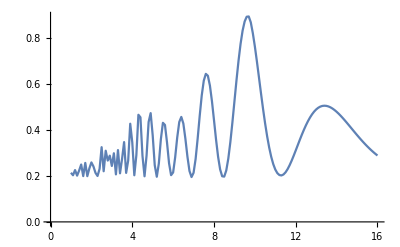

```mathematica
ListPlot[{list1,list2},Joined->True]
```

## Not used anymore : Magnus expansion

First order in Magnus expansion

```mathematica
Htilde0[th13_,th12_,Δms21_,Δms3l_,E_]:=Module[{r13 = R13[th13],r12=R12[th12]},
r13.r12.DiagonalMatrix[{0,k[Δms21,E], k[Δms3l,E]}].r12ᵀ.r13ᵀ];
```

Compute second order term in Magnus expansion

```mathematica
Clear[v,h]
h[x_]:=R13[Th13].R12[Th12].DiagonalMatrix[{k1,k2,k3}].R12[Th12]ᵀ.R13[Th13]ᵀ + DiagonalMatrix[{2v[x],-v[x],-v[x]}]/3;
comm[a_,b_]:=Simplify[a.b-b.a];
```

```mathematica
h2pert = FullSimplify[comm[h[x],h[y]]/(v[x]-v[y])];
```

```mathematica
MatrixForm[h2pert]
```

(0 | (-k1+k2) Cos[Th12] Cos[Th13] Sin[Th12] | -1/4 (k1+k2-2 k3+(k1-k2) Cos[2 Th12]) Sin[2 Th13]
(k1-k2) Cos[Th12] Cos[Th13] Sin[Th12] | 0 | 0
1/4 (k1+k2-2 k3+(k1-k2) Cos[2 Th12]) Sin[2 Th13] | 0 | 0)

```mathematica
Simplify[comm[h[x1],comm[h[x2],h[x3]]] + comm[h[x3],comm[h[x2],h[x1]]]]//MatrixForm
```

(1/2 Cos[Th13] (-(k1+k2-2 k3+(k1-k2) Cos[2 Th12]) (-k2+2 k3+k2 Cos[2 Th12]) Cos[Th13] Sin[Th13]^2+Cos[Th12]^2 (4 (k1-k2)^2 Cos[Th13] Sin[Th12]^2+k1 (k1+k2-2 k3+(k1-k2) Cos[2 Th12]) Sin[Th13] Sin[2 Th13])) (v[x1]-2 v[x2]+v[x3]) | 1/8 (k1-k2) Cos[Th13] Sin[2 Th12] (-(-2 k1-2 k2+4 k3+2 (k1-k2) Cos[2 Th12]+k1 Cos[2 (Th12-Th13)]-k2 Cos[2 (Th12-Th13)]+2 k1 Cos[2 Th13]+2 k2 Cos[2 Th13]-4 k3 Cos[2 Th13]+k1 Cos[2 (Th12+Th13)]-k2 Cos[2 (Th12+Th13)]+4 v[x1]) (v[x2]-v[x3])+(v[x1]-v[x2]) (-2 k1-2 k2+4 k3+2 (k1-k2) Cos[2 Th12]+k1 Cos[2 (Th12-Th13)]-k2 Cos[2 (Th12-Th13)]+2 k1 Cos[2 Th13]+2 k2 Cos[2 Th13]-4 k3 Cos[2 Th13]+k1 Cos[2 (Th12+Th13)]-k2 Cos[2 (Th12+Th13)]+4 v[x3])) | 1/24 Sin[2 Th13] ((v[x1]-v[x2]) (-3 (k1-k2)^2 Sin[2 Th12]^2-2 (k1+k2-2 k3+(k1-k2) Cos[2 Th12]) (3 k3 Cos[Th13]^2+3 (k1 Cos[Th12]^2+k2 Sin[Th12]^2) Sin[Th13]^2-v[x3])+6 (k1+k2-2 k3+(k1-k2) Cos[2 Th12]) (Cos[Th13]^2 (k1 Cos[Th12]^2+k2 Sin[Th12]^2)+k3 Sin[Th13]^2+(2 v[x3])/3))+(3 (k1-k2)^2 Sin[2 Th12]^2+2 (k1+k2-2 k3+(k1-k2) Cos[2 Th12]) (3 k3 Cos[Th13]^2+3 (k1 Cos[Th12]^2+k2 Sin[Th12]^2) Sin[Th13]^2-v[x1])-6 (k1+k2-2 k3+(k1-k2) Cos[2 Th12]) (Cos[Th13]^2 (k1 Cos[Th12]^2+k2 Sin[Th12]^2)+k3 Sin[Th13]^2+(2 v[x1])/3)) (v[x2]-v[x3]))
1/8 (k1-k2) Cos[Th13] Sin[2 Th12] (-(-2 k1-2 k2+4 k3+2 (k1-k2) Cos[2 Th12]+k1 Cos[2 (Th12-Th13)]-k2 Cos[2 (Th12-Th13)]+2 k1 Cos[2 Th13]+2 k2 Cos[2 Th13]-4 k3 Cos[2 Th13]+k1 Cos[2 (Th12+Th13)]-k2 Cos[2 (Th12+Th13)]+4 v[x1]) (v[x2]-v[x3])+(v[x1]-v[x2]) (-2 k1-2 k2+4 k3+2 (k1-k2) Cos[2 Th12]+k1 Cos[2 (Th12-Th13)]-k2 Cos[2 (Th12-Th13)]+2 k1 Cos[2 Th13]+2 k2 Cos[2 Th13]-4 k3 Cos[2 Th13]+k1 Cos[2 (Th12+Th13)]-k2 Cos[2 (Th12+Th13)]+4 v[x3])) | -1/2 (k1-k2)^2 Cos[Th13]^2 Sin[2 Th12]^2 (v[x1]-2 v[x2]+v[x3]) | -1/2 (k1-k2) (k1+k2-2 k3+(k1-k2) Cos[2 Th12]) Cos[Th13]^2 Sin[2 Th12] Sin[Th13] (v[x1]-2 v[x2]+v[x3])
1/4 ((v[x1]-v[x2]) (-(k1-k2)^2 Cos[Th13] Sin[2 Th12]^2 Sin[Th13]-1/3 (k1+k2-2 k3+(k1-k2) Cos[2 Th12]) Sin[2 Th13] (3 k3 Cos[Th13]^2+3 (k1 Cos[Th12]^2+k2 Sin[Th12]^2) Sin[Th13]^2-v[x3])+(k1+k2-2 k3+(k1-k2) Cos[2 Th12]) Sin[2 Th13] (Cos[Th13]^2 (k1 Cos[Th12]^2+k2 Sin[Th12]^2)+k3 Sin[Th13]^2+(2 v[x3])/3))+((k1-k2)^2 Cos[Th13] Sin[2 Th12]^2 Sin[Th13]+1/3 (k1+k2-2 k3+(k1-k2) Cos[2 Th12]) Sin[2 Th13] (3 k3 Cos[Th13]^2+3 (k1 Cos[Th12]^2+k2 Sin[Th12]^2) Sin[Th13]^2-v[x1])-(k1+k2-2 k3+(k1-k2) Cos[2 Th12]) Sin[2 Th13] (Cos[Th13]^2 (k1 Cos[Th12]^2+k2 Sin[Th12]^2)+k3 Sin[Th13]^2+(2 v[x1])/3)) (v[x2]-v[x3])) | -1/2 (k1-k2) (k1+k2-2 k3+(k1-k2) Cos[2 Th12]) Cos[Th13]^2 Sin[2 Th12] Sin[Th13] (v[x1]-2 v[x2]+v[x3]) | -1/8 (k1+k2-2 k3+(k1-k2) Cos[2 Th12])^2 Sin[2 Th13]^2 (v[x1]-2 v[x2]+v[x3]))

```mathematica
h2pert+h2pertᵀ//Simplify
```

{{0,0,0},{0,0,0},{0,0,0}}

```mathematica
h2pert[[1,2]]
```

(-k1+k2) Cos[Th12] Cos[Th13] Sin[Th12]

```mathematica
h2pert[[1,3]]
```

-1/4 (k1+k2-2 k3+(k1-k2) Cos[2 Th12]) Sin[2 Th13]

```mathematica
(* We use k2(Cos[2 th12]-1) = - 2 k2 Sin[th12]^2 *)

Htilde2[th13_,th12_,Δms21_,Δms3l_,E_]:=Module[{h12=k[Δms21,E] Cos[th12]Cos[th13]Sin[th12],h13=((-k[Δms21,E]Sin[th12]^2+ k[Δms3l,E])Sin[2th13])/2},
{{0,h12 ,h13},{-h12,0,0},{-h13,0,0}}]
```

Obtain simpler analytical for for the integral

```mathematica
Clear[a,b,c,x1,x2];
Vaverage = Simplify[Integrate[a + b x^2 + c x^4,{x,x1,x2}]/(x2-x1)];
v[x_]:=a + b x^2 + c x^4 - Vaverage;
FullSimplify[Integrate[v[x]-v[y],{x,x1,x2},{y,x1,x}]]
```

-1/30 (x1-x2)^3 (x1+x2) (5 b+2 c (2 x1^2+x1 x2+2 x2^2))

```mathematica
Integrate[v[x],{x,x1,x2}]//Simplify
```

0

```mathematica
%//.{btilde -> b/re^2, ctilde -> c/re^4, r1->x1 re, r2-> x2 re}//Simplify
```

-1/30 re^4 (x1-x2)^3 (x1+x2) (5 b+2 c re^2 (2 x1^2+x1 x2+2 x2^2))

Second order in Magnus expansion

```mathematica
densityMagnus2[η_]:=Module[{x=xj[η]},-1/30 Table[(x[[i]]-x[[i+1]])^3 (x[[i]]+x[[i+1]]) (5 βp[η][[i]]+2 γp[η][[i]] (2 x[[i]]^2+x[[i]]* x[[i+1]]+2 x[[i+1]]^2)),{i,Length[xj[η]]-1}]];
```

Matter - dependent evolutor at 2nd order in Magnus expansion

```mathematica
Utilde[th13_,th12_,Δms21_,Δms3l_,E_,η_] := Module[{x=xj[η],h0 = Htilde0[th13,th12,Δms21,Δms3l,E],h2 = Htilde2[th13,th12,Δms21,Δms3l,E],dens=densityMagnus2[η]},
Which[0≤η<Pi/2,Table[MatrixExp[-I rE*( h0 (x[[i+1]]-x[[i]]) +DiagonalMatrix[{ V[Nint[η][[i]]*mol/cm^3],0,0}])-(rE^2 V[dens[[i]]*mol/cm^3]*h2)/2],{i,Length[xj[η]]-1}],
Pi/2≤η≤Pi,MatrixExp[-I rE((Δx[η]/rE)*h0 +DiagonalMatrix[{ V[Nint[η]*mol/cm^3],0,0}])]]]
```

```mathematica
(* Now add full expression for the evolutor U *)
```

```mathematica
{th12, th13, th23, d}//N
```

{0.583638,0.149575,0.855211,3.40339}

```mathematica
Utilde[th13_,th12_,Δms21_,Δms3l_,E_,η_] := Module[{x=xj[η],h0 = Htilde0[th13,th12,Δms21,Δms3l,E],h2 = Htilde2[th13,th12,Δms21,Δms3l,E],dens=densityMagnus2[η]},
Which[0≤η<Pi/2,Table[MatrixExp[-I rE*( h0 (x[[i+1]]-x[[i]]) +DiagonalMatrix[{ V[Nint[η][[i]]*mol/cm^3],0,0}])-(rE^2 V[dens[[i]]*mol/cm^3]*h2)/2],{i,Length[x]-1}],
Pi/2≤η≤Pi,MatrixExp[-I rE((Δx[η]/rE)*h0 +DiagonalMatrix[{ V[Nint[η]*mol/cm^3],0,0}])]]]
```